```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
```

### Loading and Definitions

#### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

#### Load e σ Dicts

```mathematica
FeσDicte=ReadIt[NotebookDirectory[]<>"../capture/FeσDicte"];
SiO2σDicte=ReadIt[NotebookDirectory[]<>"../capture/SiO2σDicte"];
MgOσDicte=ReadIt[NotebookDirectory[]<>"../capture/MgOσDicte"];
```

```mathematica
ElectronicσDicts=Gather[Flatten@Join[FeσDicte,SiO2σDicte,MgOσDicte],#1["mχ"]==#2["mχ"]&];
```

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"../capture/OσDictNuc"];
```

```mathematica
NuclearσDicts=Gather[Flatten@Join[{FeσDictNuc},{SiσDictNuc},{MgσDictNuc},{OσDictNuc}],#1["mχ"]==#2["mχ"]&];
```

#### EL func Defn - from capture

```mathematica
Clear[GeteELFunction]
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]]
GeteELFunction[ElectronicσDicsts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GetNucELFunction]
GetNucELFunction[NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

#### Bethe Defn

```mathematica
nFe=13000/("M")/.FeTotalparams[[1]]
dEdlBethe[vχ_,ne_,m_,I_:286,corrections_:True]:=(*
vχ - [m s^-1],
ne - [m^-3], 
m - [Subscript[Log, 10] eV],
I - [eV] (default is for Iron)

Output: dE/dl - [eV m^-1]
*)(*("JpereV")^-1*)( (2 π ("e")^4)/((4π)^2("ϵ0")^2 10^6/2("JpereV")/("c")^2 vχ^2))nFe( Log@(1/I(2 ("m"vχ^2)/("JpereV"))) +If[corrections,- Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2 - 1/2 (Log[R]+(10^(6-m)/2(γ^2-1)/γ R)^2/.R->(1+10^(2(6-m))/4+γ 10^(6-m))/.γ->1/(√(1- vχ^2/("c")^2)))(*+(("c""α")/vχ)^2Zeta[3]*),0])/.Constants`SIConstRepl
```

1.40188×10^29

```mathematica
"m"/.SIConstRepl
("JpereV")/2 10^6/.SIConstRepl
```

9.11×10^-31

8.01×10^-14

#### Heavy mass limit Stopping power defn

```mathematica
Clear[InterpolateLossFnmχto∞]
InterpolateLossFnmχto∞[params_,m_:10,ϵ_:10^-6,regionindex_:1,materialname_:"material",zbounds_:{-5,7},ubound_:7]:=Module[{ωmin,vχ,prefactorofvχ,nzs,nus,integrandofuz,Interpointsz,Interpointsu,integrandTable,integrandf,uintegralofvχz,integrandofvχz,integrandofvχzTable,integrandofvχzf,Interpointsvχ,Interpointsvχandξ,InterdσTable,Interdσf,InterσTable,Interσf,InterdEdlTable,InterdEdlf,InterσofξTable,Interσofξf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

ωmin= "ωedgei"/.params; (*the cutoff used in the data fitting*)

vχ = {ϵ "vF", 2 10^-1 "c"}/.params;(*interpolate from the minimum velocity (up to an order 1 fudge factor (3) for numerical stability) to the boundary of the non-relativistic regime*)

If[vχ[[1]]>vχ[[2]],Print["minimum energy requires relativistic probes, we won't consider these"];Return["NA",Module]];

Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];

nzs = 2(zbounds[[2]]-zbounds[[1]]);
nus = 50;

prefactorofvχ = ((2 ("qF")^2 ("vF")^2 ("e")^2)/(π^2 #^2 "ϵ0")/.params)& (*SI units, notes use CGS*);


(*define and interpolate the integrand*)
integrandofuz[u_?NumberQ,z_?NumberQ] := If[20 >#,If[#>0.01,1/(1-E^(- #)),1/#-1/2],1]&[ 4 "D" u z/.params] u z Im[-1/ϵMNum[u,z,("νi")/("vF"2"qF"z)/.params,params]];

Interpointsz = Table[10^z,{z,zbounds[[1]],zbounds[[2]],0.5}];(*should chang 7->11*)
(*Interpointsz = Subdivide[10^zbounds[[1]],10^zbounds[[2]],nzs];*)
(*Interpointsu = 10^Subdivide[Log10[Min[vχ[[1]]/("vF"),10^-ubound]],Log10[vχ[[2]]/("vF")],50]/.params;*)
Interpointsu = 10^Subdivide[Log10[10^(-(1+ubound))vχ[[1]]/("vF")],Log10[vχ[[2]]/("vF")],nus]/.params;
integrandTable = Table[{{Interpointsu[[u]],Interpointsz[[z]]},Abs@integrandofuz[Interpointsu[[u]],Interpointsz[[z]]]},{u,Length[Interpointsu]},{z,Length[Interpointsz]}];
integrandf = Interpolation[Flatten[Log10[integrandTable],1],InterpolationOrder->1];

(*InterdσTable=Table[{Interpointsz[[i]],},{i,m+1},{j,n+1}];*)
(*Interdσf=Interpolation[Flatten[Log10[InterdσTable],1],InterpolationOrder->4];*)
(*Interdσf=Interpolation[Flatten[Log10[InterdσTable],1],InterpolationOrder->1];
Print["dσ interpolation done"];*)

(*interpolate the stopping power*)
(*uintegralofvχz[vχ_?NumberQ,z_?NumberQ] := Sum[NIntegrate[integrandofuz[u,z],{u,If[c==-ubound,0,1] 10^(c-1)(vχ/("vF")/.params),10^c(vχ/("vF")/.params)},MaxRecursion->8,AccuracyGoal->5,PrecisionGoal->5,Method->"LocalAdaptive"],{c,-ubound,0}];*)
(*uintegralofvχz[vχ_?NumberQ,z_?NumberQ] := Sum[NIntegrate[10^integrandf[Log10@u,Log10@z],{u,If[cu==-ubound,0,1] 10^(cu-1)(vχ/("vF")/.params),10^cu(vχ/("vF")/.params)},MaxRecursion->5,AccuracyGoal->4,PrecisionGoal->4,Method->"Trapezoidal"],{cu,-ubound,0}];*)
uintegralofvχz[vχ_?NumberQ,z_?NumberQ] := Sum[NIntegrate[10^integrandf[Log10@u,Log10@z],{u,10^(cu-1)(vχ/("vF")/.params),10^cu(vχ/("vF")/.params)},MaxRecursion->5,AccuracyGoal->4,PrecisionGoal->4,Method->"Trapezoidal"],{cu,-ubound,0}];

(*integrandofvχzTable=Table[{{Interpointsu[[v]],Interpointsz[[z]]},Abs@uintegralofvχz[Interpointsvχ[[v]],Interpointsz[[z]]]},{v,Length[Interpointsvχ]},{z,Length[Interpointsz]}];
integrandofvχzf = Interpolation[Flatten[Log10[integrandofvχzTable],1],InterpolationOrder->1];
*)

(*InterdEdlTable =Table[{Interpointsvχ[[v]],prefactorofvχ[Interpointsvχ[[v]]]Sum[NIntegrate[10^integrandofvχzf[Interpointsvχ[[v]],z],{z,If[cz==zbounds[[1]],0,1] 10^(cz-1),10^cz},Method->{"LocalAdaptive"},MaxRecursion->4,AccuracyGoal->3,PrecisionGoal->3],{cz,zbounds[[1]],zbounds[[2]],1}]},{v,m+1}];*)
InterdEdlTable =Table[{Interpointsvχ[[v]],prefactorofvχ[Interpointsvχ[[v]]]Sum[NIntegrate[uintegralofvχz[Interpointsvχ[[v]],z],{z,If[cz==zbounds[[1]],0,1] 10^(cz-1),10^cz},Method->{"Trapezoidal"},MaxRecursion->4,AccuracyGoal->3,PrecisionGoal->3],{cz,zbounds[[1]],zbounds[[2]],1}]},{v,m+1}];
InterdEdlf= Interpolation[Log10[InterdEdlTable],InterpolationOrder->1];
Print["dEdlf interpolation done"];


<|"Interpointsvχ"->Interpointsvχ,"integrand"->integrandf,"dEdlf"->InterdEdlf,"vχ"->Log10[vχ],"params"->params,"ωmin"->ωmin,"regionindex"->regionindex,"materialname"->materialname|>
]
```

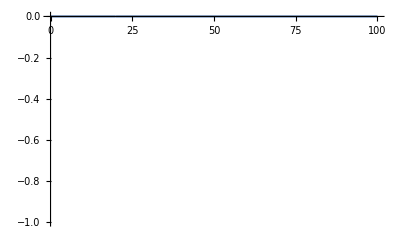

```mathematica
Plot[If[20 >#,If[#>0.01,1/(1-E^(- #)),1/#-1/2],1]&[x]-1/(1-E^(- x)),{x,0,100},PlotRange->All]
```

## Dielectric Analytics

### Numerical Stabilization analytics

#### z=1 branch cut

```mathematica
ϵRPA0[z]
```

1+(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

```mathematica
ϵMatbranchcut[u_,z_,uν_]:=1+1/2 ("χ")^2 (1-I u/uν (1+8/(-8+2 (-2+u+I uν) uν ArcTan[(-2+u)/uν]-4 (u+I uν) uν ArcTan[u/uν]+uν (2 (2+u+I uν) ArcTan[(2+u)/uν]+(2 I-I u+uν) Log[(u^2+uν^2)/((-2+u)^2+uν^2)]+I (2+u+I uν) Log[1+(4 (1+u))/(u^2+uν^2)]))))
```

```mathematica
Limit[ϵRPA0[z],z->1,Direction->"FromAbove"]
Limit[ϵRPA0[z],z->1,Direction->"FromBelow"]
```

1/2 (2+χ^2)

1/2 (2+χ^2)

```mathematica
Ζ[a,uν]
```

{a+a uν (-ArcTan[(1-a)/uν]-ArcTan[(1+a)/uν])+1/4 (1-a^2+uν^2) Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)],uν+1/2 (1-a^2+uν^2) (-ArcTan[(1-a)/uν]-ArcTan[(1+a)/uν])-1/2 a uν Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)]}

```mathematica
ϵRPACt[u_,z_,uν_]:={1,0} + "χ"^2/(4 z^3) ({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]))(*abs is for numerical stability , matrix prefactor is for parity of real and imaginary parts under u->-u*)
```

```mathematica
Assuming[u>0,Limit[ϵRPACt[u,z,uν],z->1]//FullSimplify]
```

{1+1/4 χ^2 (2+(-1+u) uν (ArcTan[(2-u)/uν]+ArcTan[u/uν])+(1+u) uν (ArcTan[u/uν]-ArcTan[(2+u)/uν])+1/4 ((-2+u) u-uν^2) Log[(u^2+uν^2)/((-2+u)^2+uν^2)]+1/4 (-u (2+u)+uν^2) Log[1+(4 (1+u))/(u^2+uν^2)]),1/8 χ^2 (((-2+u) u-uν^2) (ArcTan[(-2+u)/uν]-ArcTan[u/uν])+(-u (2+u)+uν^2) (ArcTan[u/uν]-ArcTan[(2+u)/uν])+(-1+u) uν Log[(u^2+uν^2)/((-2+u)^2+uν^2)]-(1+u) uν Log[1+(4 (1+u))/(u^2+uν^2)])}

```mathematica
ϵMatbranchcut[u,z,uν]
```

1+1/2 χ^2 (1-(ⅈ u (1+8/(-8+2 (-2+u+ⅈ uν) uν ArcTan[(-2+u)/uν]-4 (u+ⅈ uν) uν ArcTan[u/uν]+uν (2 (2+u+ⅈ uν) ArcTan[(2+u)/uν]+(2 ⅈ-ⅈ u+uν) Log[(u^2+uν^2)/((-2+u)^2+uν^2)]+ⅈ (2+u+ⅈ uν) Log[1+(4 (1+u))/(u^2+uν^2)]))))/uν)

```mathematica
Limit[1 + ((up +I uν) ({1,I} . ϵRPACt[up,z,uν]-1))/(up + I uν  ({1,I} . ϵRPACt[up,z,uν]-1)/(("χ")^2/2)),z->1]//Simplify;
Assuming[u>0,ϵMatbranchcut[u,z,uν]==%/.up->u//Simplify]
```

True

#### Large u and z limit of ϵM

```mathematica
Series[Ζ[a,uν],{a,∞,8}];
%//Normal;
(%/.a->(u+z))-(%/.a->(u-z))//Simplify (*far from z=u*)
```

{-1/(315 (u-z)^7 (u+z)^7)4 z (105 u^12-63 u^10 (-1+5 uν^2+10 z^2)+3 u^8 (15+175 uν^4-77 z^2+525 z^4+35 uν^2 (-6+11 z^2))-3 u^2 z^4 (-35+735 uν^6-24 z^2+7 z^4+210 z^6-35 uν^4 (63+8 z^2)+uν^2 (945+336 z^2-35 z^4))+7 u^4 z^2 (25-525 uν^6-18 z^2-18 z^4+225 z^6-105 uν^4 (-15+2 z^2)+9 uν^2 (-75+28 z^2+10 z^4))-7 u^6 (-5-315 uν^4+105 uν^6-42 z^4+300 z^6+15 uν^2 (9+14 z^4))+z^6 (5-105 uν^6+9 z^2+21 z^4+105 z^6+105 uν^4 (3+z^2)-3 uν^2 (45+42 z^2+35 z^4))),1/(315 (u-z)^8 (u+z)^8)8 u uν z (105 u^12-42 u^10 (-3+5 uν^2+15 z^2)+9 u^8 (15+35 uν^4-42 z^2+175 z^4+70 uν^2 (-1+z^2))+7 u^4 z^2 (140-420 uν^6-90 z^2+36 z^4+225 z^6-42 uν^4 (-42+5 z^2)-60 uν^2 (21-7 z^2+z^4))-4 u^6 (-35+105 uν^6-45 z^2-63 z^4+525 z^6-21 uν^4 (21+5 z^2)+105 uν^2 (3+2 z^2+z^4))+z^6 (140-420 uν^6+135 z^2+126 z^4+105 z^6+63 uν^4 (28+5 z^2)-210 uν^2 (6+3 z^2+z^4))-2 u^2 z^4 (-490+1470 uν^6-90 z^2+189 z^4+315 z^6-42 uν^4 (147+5 z^2)-105 uν^2 (-42-4 z^2+3 z^4)))}

```mathematica
-(ArcTan[(1-a)/uν] + ArcTan[(1+a)/uν]);
Series[%,{a,∞,2}](*large a limit of h1*)
```

-(2 uν)/a^2+O[1/a]^3

```mathematica
1/2 Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)];
Series[%,{a,∞,2}](*large a limit of h2*)
```

2/a+O[1/a]^3

```mathematica
Ζ[a,uν]
Series[%,{a,∞,2}]
%//Normal
(%/.a->(u+z))-(%/.a->(u-z))//Simplify (*far from z=u*)
```

{a+a uν (-ArcTan[(1-a)/uν]-ArcTan[(1+a)/uν])+1/4 (1-a^2+uν^2) Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)],uν+1/2 (1-a^2+uν^2) (-ArcTan[(1-a)/uν]-ArcTan[(1+a)/uν])-1/2 a uν Log[((1+a)^2+uν^2)/((1-a)^2+uν^2)]}

{2/(3 a)+O[1/a]^3,-(2 uν)/(3 a^2)+O[1/a]^3}

{2/(3 a),-(2 uν)/(3 a^2)}

{(4 z)/(3 (-u^2+z^2)),(8 u uν z)/(3 (u-z)^2 (u+z)^2)}

```mathematica
Assuming[z>1,Series[(ϵRPA0[z]-1)(4 z^3)/("χ")^2,{z,∞,6}]//Simplify]
Assuming[z>1,Series[ϵRPA0[z],{z,∞,6}]//Simplify]
```

4/(3 z)+4/(15 z^3)+4/(35 z^5)+O[1/z]^7

1+χ^2/(3 z^4)+χ^2/(15 z^6)+O[1/z]^7

#### Large z only limit of ϵM

```mathematica
Series[Ζ[(u+z),uν]-Ζ[(u-z),uν],{z,∞,8}]//Simplify;
%//Normal(*far from z=u*)
```

{1/z^7(4/63+(4 u^6)/3-(12 uν^2)/7+4 uν^4-(4 uν^6)/3+u^4 (4-20 uν^2)+4/7 u^2 (3-42 uν^2+35 uν^4))+(4/35+(4 u^4)/3-(8 uν^2)/5+(4 uν^4)/3+u^2 (8/5-8 uν^2))/z^5+(4 (1+5 u^2-5 uν^2))/(15 z^3)+4/(3 z),(8 u uν (9+21 u^4-42 uν^2+21 uν^4+u^2 (42-70 uν^2)))/(21 z^7)+(16 u uν (3+5 u^2-5 uν^2))/(15 z^5)+(8 u uν)/(3 z^3)}

```mathematica
{1/z^7(4/63+(4 u^6)/3-(12 uν^2)/7+4 uν^4-(4 uν^6)/3+u^4 (4-20 uν^2)+4/7 u^2 (3-42 uν^2+35 uν^4))+(4/35+(4 u^4)/3-(8 uν^2)/5+(4 uν^4)/3+u^2 (8/5-8 uν^2))/z^5+(4 (1+5 u^2-5 uν^2))/(15 z^3)+4/(3 z),(8 u uν (9+21 u^4-42 uν^2+21 uν^4+u^2 (42-70 uν^2)))/(21 z^7)+(16 u uν (3+5 u^2-5 uν^2))/(15 z^5)+(8 u uν)/(3 z^3)}/.uν->("νi")/(2 "qF" "vF"z)/.z->10^9/.u->10^-1/.FeTotalparams[[2]]
```

{1.33333×10^-9,3.25828×10^-38}

```mathematica
ϵRPAC[u,z,("νi")/(2 "qF" "vF"z)]/.z->10^10.5/.u->10^-2/.FeTotalparams[[2]]
Im[-1/%]
```

1.+8.6941×10^-78 ⅈ

8.6941×10^-78

```mathematica
ϵM[u,z,("νi")/(2 "qF" "vF"z)]/.z->10^10.5/.u->10^-2/.FeTotalparams[[2]]
Im[-1/%]
```

1.+4.34705×10^-53 ⅈ

4.34705×10^-53

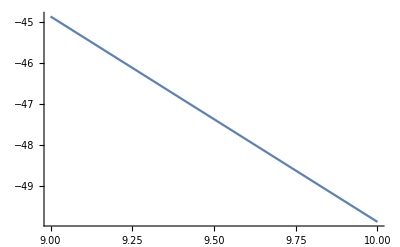

```mathematica
Plot[Log10@Im[-1/(ϵM[u,10^z,("νi")/(2 "qF" "vF"10^z)]/.u->10^-2/.FeTotalparams[[2]])],{z,9,10}]
```

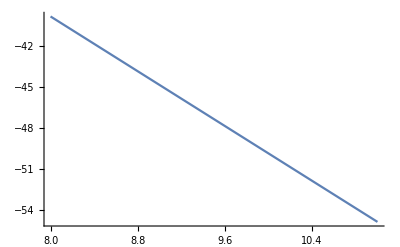

```mathematica
Plot[Log10@Im[-1/(ϵM[u,10^z,("νi")/(2 "qF" "vF"10^z)]/.u->10^-2/.FeTotalparams[[2]])],{z,8,11}]
```

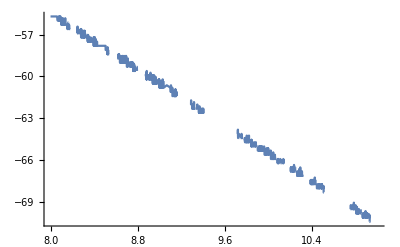

```mathematica
$MinPrecision=120;
Plot[Log10@Im[-1/(ϵM[u,10^z,("νi")/(2 "qF" "vF"10^z)]/.u->10^-2/.FeTotalparams[[2]])],{z,8,11},WorkingPrecision->120]
```

#### Small a limit of Ζ

```mathematica
Series[Ζ[a,uν],{a,∞,2}]
largea=%//Normal
Series[Ζ[a,uν],{a,0,10}];
smalla=%//Normal//FullSimplify
(largea/.a->(u+z))-(smalla/.a->(u-z))//FullSimplify;
(*Series[%,{uν,0,1}]//PowerExpand//Normal//Simplify(*close to z=u*)*)
```

{2/(3 a)+O[1/a]^3,-(2 uν)/(3 a^2)+O[1/a]^3}

{2/(3 a),-(2 uν)/(3 a^2)}

{2 a+(2 a (-105 a^2 (1+uν^2)^6+21 a^4 (1+uν^2)^4 (-1+5 uν^2)-3 a^6 (1+uν^2)^2 (3-42 uν^2+35 uν^4)+5 a^8 (-1+3 uν^2 (9+7 uν^2 (-3+uν^2)))))/(315 (1+uν^2)^8)-2 a uν ArcCot[uν],uν+(a^2 uν (-210 a^2 (1+uν^2)^6-315 (1+uν^2)^8+42 a^4 (1+uν^2)^4 (-3+5 uν^2)+14 a^8 (-5+45 uν^2-63 uν^4+15 uν^6)-30 a^6 (3-8 uν^2-18 uν^4+7 uν^8)))/(315 (1+uν^2)^9)+(-1+a^2-uν^2) ArcCot[uν]}

#### Plot Dielectric No Stabilization

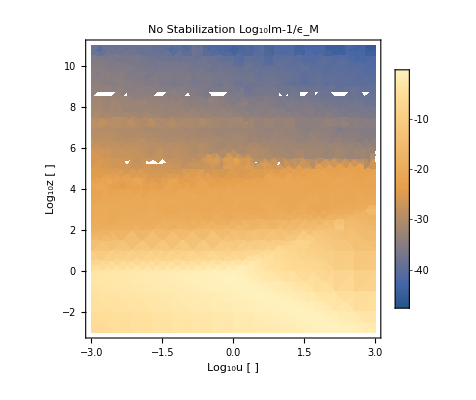

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"No Stabilization Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

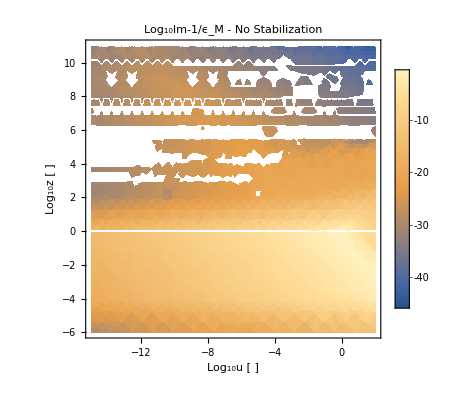

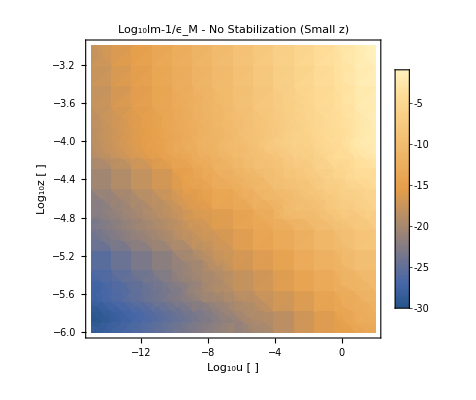

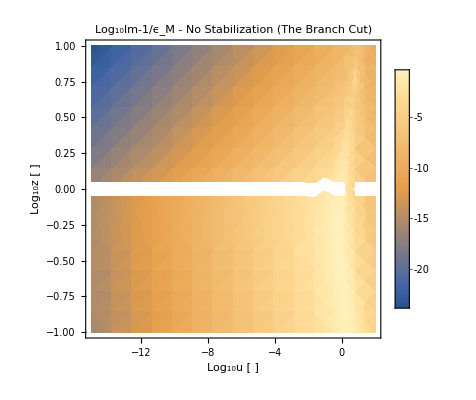

```mathematica
("χ")^2/(4 z^3) (2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
("χ"^2/(4 z^3) {1,I} .{{1,0},{0,Sign[u]}} . Abs@(Ζ[u+z,uν]-Ζ[u-z,uν]));
1+((u+I uν) %)/(u + I uν %/(%%))/.uν->("νi")/(2 "qF" "vF"z)/.z->10^zt/.u->10^ut/.FeTotalparams[[2]];
DensityPlot[Log10@Im[-1/%],{ut,-15,2},{zt,-6,11},PlotLegends->Automatic,PlotLabel->"Log_10Im-1/ϵ_M - No Stabilization",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
DensityPlot[Log10@Im[-1/(%%)],{ut,-15,2},{zt,-6,-3},PlotLegends->Automatic,PlotLabel->"Log_10Im-1/ϵ_M - No Stabilization (Small z)",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
DensityPlot[Log10@Im[-1/(%%%)],{ut,-15,2},{zt,-1,1},PlotLegends->Automatic,PlotLabel->"Log_10Im-1/ϵ_M - No Stabilization (The Branch Cut)",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

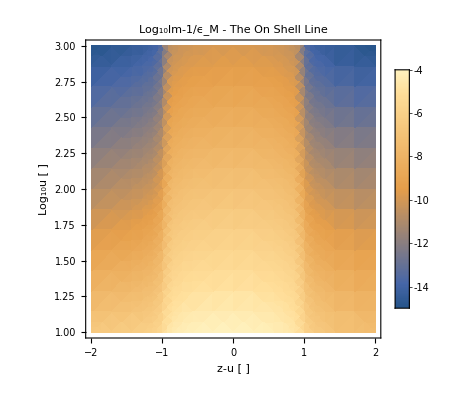

```mathematica
("χ")^2/(4 z^3) (2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
("χ"^2/(4 z^3) {1,I} .{{1,0},{0,Sign[u]}} .Abs@(Ζ[u+z,uν]-Ζ[u-z,uν]));
1+((u+I uν) %)/(u + I uν %/(%%))/.uν->("νi")/(2 "qF" "vF"z)/.z->u + zmu/.u->10^u/.FeTotalparams[[2]];
(*1+((u+I uν)( ϵRPACm1[u,z,uν]))/(u + I uν ( ϵRPACm1[u,z,uν])/(%%))/.uν->("νi")/(2 "qF" "vF"z)/.z->10^u + zmu/.u->10^u/.*)(*FeTotalparams[[2]];*)
DensityPlot[Log10@Im[-1/%],{zmu,-2,2},{u,1,3},PlotLegends->Automatic,PlotLabel->"Log_10Im-1/ϵ_M - The On Shell Line",FrameLabel->{"z-u [ ]","Log_10u [ ]"}]

(*DensityPlot[Log10@Im[-1/(ϵM[u,z,uν]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^ut + zmu/.u->10^ut/.FeTotalparams[[2]])],{zmu,-2,2},{ut,1,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"z-u [ ]","Log_10u [ ]"}]*)
```

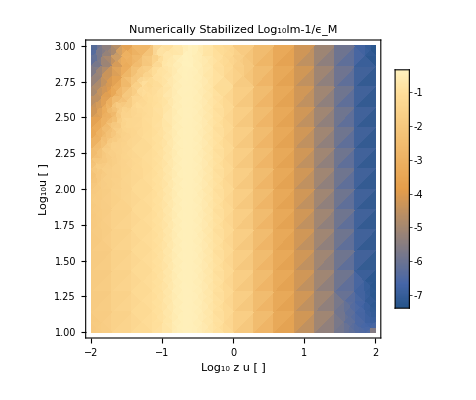

```mathematica
("χ")^2/(4 z^3) (2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
("χ"^2/(4 z^3) {1,I} .{{1,0},{0,Sign[u]}} .Abs@(Ζ[u+z,uν]-Ζ[u-z,uν]));
1+((u+I uν) %)/(u + I uν %/(%%))/.uν->("νi")/(2 "qF" "vF"z)/.z-> (10^c)/u/.u->10^u/.FeTotalparams[[2]];
DensityPlot[Log10@Im[-1/%/.FeTotalparams[[1]]],{c,-2,2},{u,1,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10 z u [ ]","Log_10u [ ]"},PlotRange->All]
```

```mathematica
("χ")^2/(4 z^3) (2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
("χ"^2/(4 z^3) {1,I} .{{1,0},{0,Sign[u]}} .Abs@(Ζ[u+z,uν]-Ζ[u-z,uν]));
1+((u+I uν) %)/(u + I uν %/(%%))/.uν->("νi")/(2 "qF" "vF"z)/.z-> (10^c)/u/.u->10^u/.FeTotalparams[[2]];
DensityPlot[Log10@Im[-1/%/.FeTotalparams[[1]]],{c,-2,2},{u,1,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10 z u [ ]","Log_10u [ ]"},PlotRange->All]
```

#### Plot Dielectric Post fix - ω q all oscillators

```mathematica
Log10@Sum[(HeavisideTheta[10^u 10^z 4"EF"-"ωedgei"]/.FeTotalparams[[o]])Im[(-"Ai")/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[o]]]/.FeTotalparams[[o]]],{o,Length[FeTotalparams]}]/.{u->7,z->1}
Sum[(HeavisideTheta[10^u 10^z 4("EF")/("ℏ")-"ωedgei"]/.FeTotalparams[[o]]),{o,Length[FeTotalparams]}]/.{u->9,z->-1}
```

Indeterminate

6

```mathematica
10^u 10^z 4"EF"-"ωedgei"/.FeTotalparams[[2]]
```

-6.5887×10^12+1.94267×10^-18 2^(2+u+z) 5^(u+z)

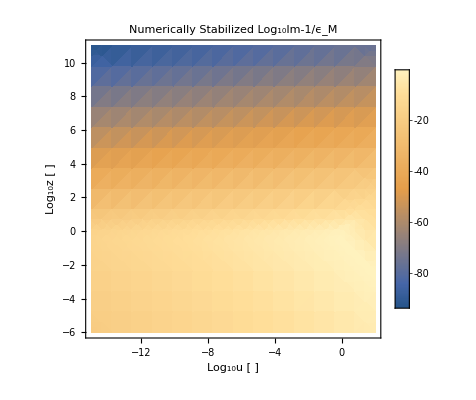

```mathematica
DensityPlot[Log10@Sum[(HeavisideTheta[10^u 10^z 4("EF")/("ℏ")-"ωedgei"]/.ReplaceParams[FeTotalparams[[o]],0,"ωedgei"])Im[(-"Ai")/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[o]]]/.FeTotalparams[[o]]],{o,Length[FeTotalparams]}],{u,-15,2},{z,-6,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

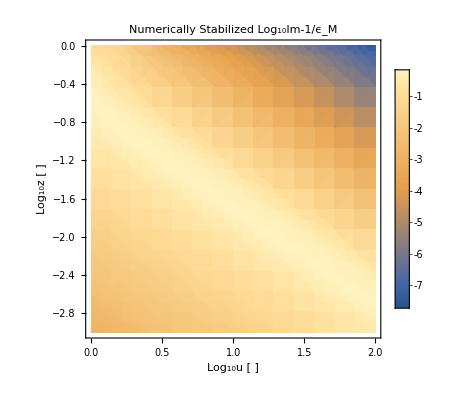

```mathematica
DensityPlot[Log10@Sum[(HeavisideTheta[10^u 10^z 4("EF")/("ℏ")-"ωedgei"]/.FeTotalparams[[o]])Im[(-"Ai")/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[o]]]/.FeTotalparams[[o]]],{o,Length[FeTotalparams]}],{u,0,2},{z,-3,0},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

```mathematica
"ωedgei"/.FeTotalparams
"qF"/.FeTotalparams
```

{6.04519×10^14,6.5887×10^12,3.02977×10^14,1.51848×10^14,1.09042×10^18,1.09893×10^19}

{1.45392×10^10,1.78329×10^10,2.34292×10^10,4.54874×10^10,2.30757×10^11,1.05805×10^12}

```mathematica
Solve[ω/(2"qF""vF")==1,ω]/.FeTotalparams[[2]]
```

{{ω→7.36556×10^16}}

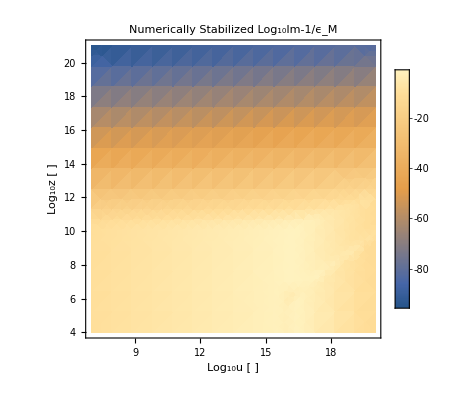

```mathematica
DensityPlot[Log10@Sum[(HeavisideTheta[ω-"ωedgei"]/.ReplaceParams[FeTotalparams[[o]],0,"ωedgei"])Im[(-"Ai")/ϵMωq[10^ω,10^k,"νi","qF","vF"]/.FeTotalparams[[o]]],{o,1,2}],{ω,7,20},{k,4,21},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

#### Plot Dielectric - Conduction Post fix

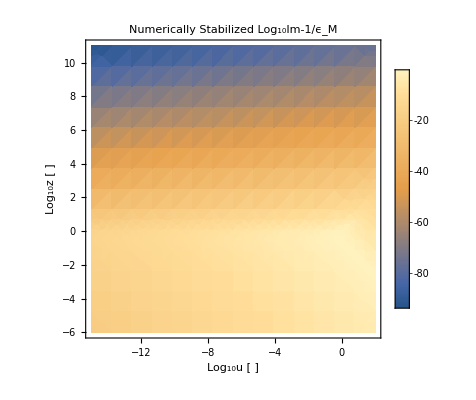

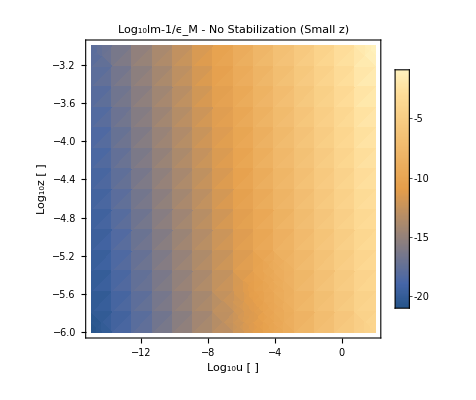

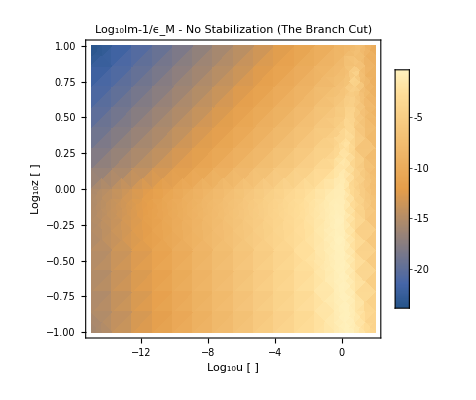

```mathematica
(*conduction*)
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-15,2},{z,-6,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
DensityPlot[Log10@Im[-1/ϵM[10^ut,10^zt,("νi")/(2 "qF" "vF"10^zt)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{ut,-15,2},{zt,-6,-3},PlotLegends->Automatic,PlotLabel->"Log_10Im-1/ϵ_M - No Stabilization (Small z)",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
DensityPlot[Log10@Im[-1/ϵM[10^ut,10^zt,("νi")/(2 "qF" "vF"10^zt)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{ut,-15,2},{zt,-1,1},PlotLegends->Automatic,PlotLabel->"Log_10Im-1/ϵ_M - No Stabilization (The Branch Cut)",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

#### Investigate weirdness near z = 10^6

100

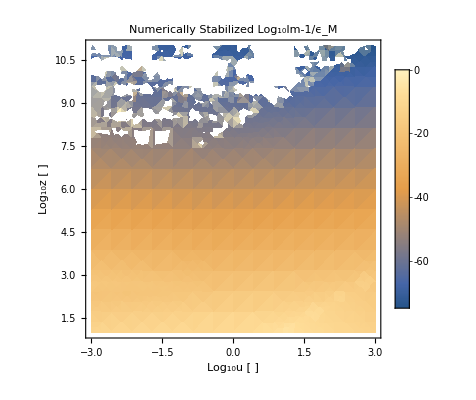

```mathematica
$MinPrecision = 100
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-3,3},{z,1,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

Is it our χRPAC?

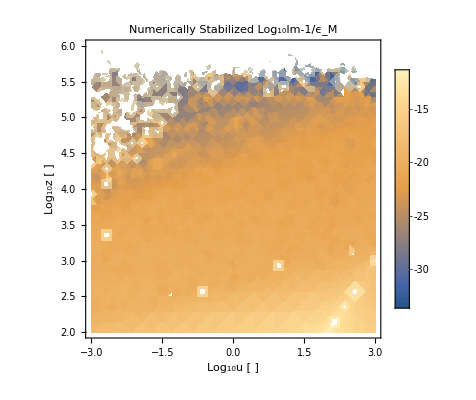

```mathematica
"Is it our χRPAC?"
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-3,3},{z,2,6},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->50]
```

The above plot did not use an expansion for ϵRPACm1. Even with higher working precision it’s fucked.

But if we do have increased working precision.

Is it our χRPAC?

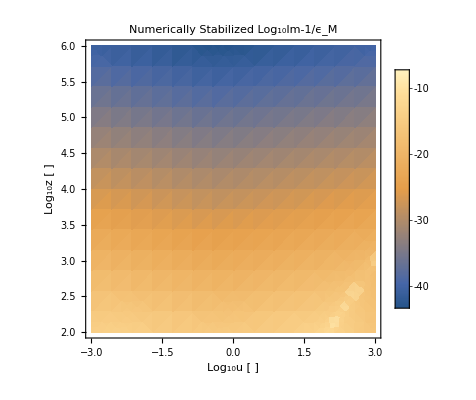

```mathematica
"Is it our χRPAC?"
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-3,3},{z,2,6},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->50]
```

So upshot in all plots and Nintegrates, we need to jack up the working precision, as well as do the expansions.

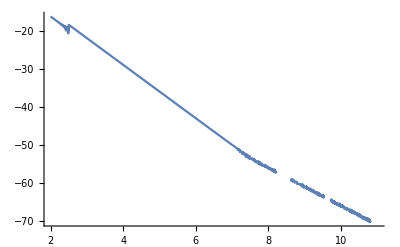

```mathematica
Plot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]]/.u->-1,{z,2,11},WorkingPrecision->100]
```

```mathematica
$MinPrecision
```

100

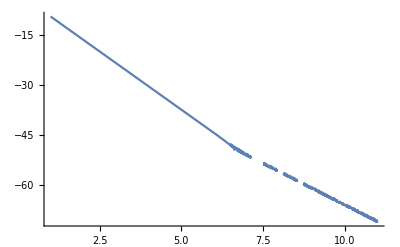

```mathematica
Plot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]]/.u->-1,{z,1,11},WorkingPrecision->140]
```

https : // mathematica . stackexchange . com/questions/61433/increase - precision - for - a - entire - notebook

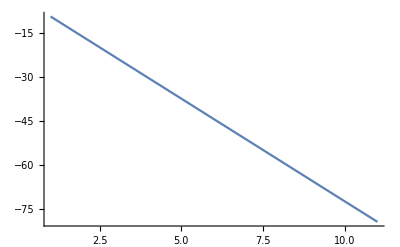

```mathematica
Plot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]]/.u->-1,{z,1,11},WorkingPrecision->140]
```

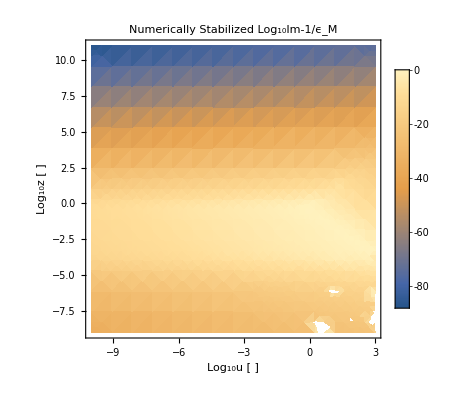

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-10,3},{z,-9,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

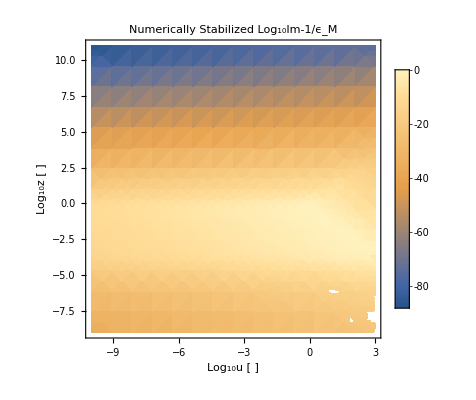

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-10,3},{z,-9,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

```mathematica
ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.u->-1/.z->10/.FeTotalparams[[2]]
Log10@Im[-1/%]
```

```mathematica
zt=10;
$MinPrecision=140;
N[ϵRPACm1[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.u->-2/.z->zt/.FeTotalparams[[2]],140];
N[ϵRPA0m1[10^z]/.z->zt/.FeTotalparams[[2]],140];
Num=N[(10^u + I uν)%%/.uν->("νi")/(2 "qF" "vF"10^z)/.u->-2/.z->zt/.FeTotalparams[[2]],140]
Denom=N[10^u + I uν ((%%%)/(%%))/.uν->("νi")/(2 "qF" "vF"10^z)/.u->-2/.z->zt/.
FeTotalparams[[2]],140]
N[-1/(1+(%%)/%),140];
N[Im[%],140]
```

1.12506×10^-43+1.37466×10^-52 ⅈ

0.01+1.22186×10^-11 ⅈ

-4.74778×10^-66

```mathematica
Re[Num] Im[Denom]
Im[Num]Re[Denom]
```

1.37466×10^-54

1.37466×10^-54

This is almost exactly cancelling the imaginary part of the numerator. can we simplify the ϵM loss function?

#### Solve difference issue in evaluation of ϵM

```mathematica
Series[Ζ[u+z,uν]-Ζ[u-z,uν],{u,0,4}]//Normal;
("χ"^2/(4 z^3))Series[%,{z,∞,4}]//Normal
```

{(χ^2 (1+5 u^2-5 uν^2))/(15 z^6)+χ^2/(3 z^4),(2 χ^2 u uν)/(3 z^6)}

```mathematica
"χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]));
Series[%,{z,∞,6}]//Normal
```

χ^2/(3 z^4)+(χ^2 (1+5 u^2-5 uν^2+10 ⅈ u uν Sign[u]))/(15 z^6)

```mathematica
Assuming[z>1,Series[("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]),{z,∞,6}]]//Normal
```

χ^2/(15 z^6)+χ^2/(3 z^4)

```mathematica
Clear[ci,cr,zr]
(u+I un) (cr + I ci)
Numri={Re[%],Im[%]}//ComplexExpand
u + I un (cr + I ci)/zr
Denomri={Re[%],-Im[%]}//ComplexExpand//Simplify
(Numri[[2]] Denomri[[1]] - Numri[[1]] Denomri[[2]])/(Denomri[[2]]^2 + Denomri[[1]]^2)//Simplify
```

(ⅈ ci+cr) (u+ⅈ un)

{cr u-ci un,ci u+cr un}

u+(ⅈ (ⅈ ci+cr) un)/zr

{u-(ci un)/zr,-(cr un)/zr}

(((ci u+cr un) (u-(ci un)/zr)+(cr un (cr u-ci un))/zr) zr^2)/(cr^2 un^2+(ci un-u zr)^2)

```mathematica
{cr,ci}={(("χ")^2 (1+5 u^2-5 uν^2))/(15 z^6)+("χ")^2/(3 z^4),(2 ("χ")^2 u uν)/(3 z^6)}(*cr, ci*)
zr=("χ")^2/(15 z^6)+("χ")^2/(3 z^4)(*zr*)
(((ci u+cr un) (u-(ci un)/zr)+(cr un (cr u-ci un))/zr) zr^2)/(cr^2 un^2+(ci un-u zr)^2)/.un->uν//FullSimplify
Series[%,{z,∞,6}]
```

{(χ^2 (1+5 u^2-5 uν^2))/(15 z^6)+χ^2/(3 z^4),(2 χ^2 u uν)/(3 z^6)}

χ^2/(15 z^6)+χ^2/(3 z^4)

(χ^2 u uν (1+5 z^2) (25 u^4+(-2+25 uν^2-10 z^2) (-1+5 uν^2-5 z^2)+25 u^2 (1-10 uν^2+5 z^2)))/(15 (u^2+uν^2) z^6 (25 uν^4+5 uν^2 (-2+5 u^2-10 z^2)+(1+5 z^2)^2))

(2 χ^2 u uν)/(3 (u^2+uν^2) z^4)+(χ^2 u uν (2+25 u^2-15 uν^2))/(15 (u^2+uν^2) z^6)+O[1/z]^7

```mathematica
Assuming["χ"∈ Reals,Im[(("χ")^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+("χ")^2/(3 z^4)]//ComplexExpand//Simplify]
```

(χ^2 u uν)/(3 z^6)

#### z inf limit of ϵM - and the resolution to cancellation issue there

```mathematica
Assuming["χ"∈ Reals,Im[-1/(1+(("χ")^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+("χ")^2/(3 z^4))]//ComplexExpand//Simplify]
%/.uν->("νi")/(2 "qF" "vF"z)/.u->10^-2/.z->10^11/.FeTotalparams[[2]]
```

(75 χ^2 u uν z^6)/(225 z^12+30 χ^2 z^6 (1+5 u^2+5 z^2)+χ^4 (25 u^4+(1+5 z^2)^2+5 u^2 (2+5 uν^2+10 z^2)))

1.37466×10^-81

Notice this is way fucking smaller than what we were getting above. We definitely need to use this limit.

```mathematica
LargezϵAssoc = Block[{order=8,ϵCm1,ϵ0m1,Denom,Num,ϵm1,Imϵ,Assoc},

ϵCm1="χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]));
ϵCm1=Assuming[{z>1,u>0},Series[ϵCm1,{z,∞,order}]//PowerExpand//Simplify]//Normal;

ϵ0m1=("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
ϵ0m1=Assuming[{z>1,u>0},Series[ϵ0m1,{z,∞,order}]//PowerExpand//Simplify]//Normal;

Num=Assuming[{z>1,u>0},Series[(u+I uν)ϵCm1,{z,∞,order}]//PowerExpand//Simplify]//Normal;
Denom=Assuming[{z>1,u>0},Series[u + I uν ϵCm1/ϵ0m1,{z,∞,order}]//PowerExpand//Simplify]//Normal;

(*ϵm1=Assuming[{z>1,u>0},Series[((u+I uν)ϵCm1)/(u + I uν ϵCm1/ϵ0m1),{z,∞,8}]//PowerExpand//Simplify]//Normal;*)
ϵm1=Assuming[{z>1,u>0},Series[Num/Denom,{z,∞,order}]//PowerExpand//Simplify]//Normal;
Imϵ = Assuming["χ"∈ Reals,Im[ϵm1]//ComplexExpand//Simplify];
(*Assuming["χ"∈ Reals,Im[-1/(1+%%)]//ComplexExpand//FullSimplify];*)

Assoc = <|"ϵCm1"->ϵCm1,"ϵ0m1"->ϵ0m1,"Denom"->Denom,"Num"->Num,"ϵm1"->ϵm1,"Imϵ"->Imϵ|>
(*Print[Assoc];*)
(*Assoc*)
]
```

<|ϵCm1→(χ^2 (3+35 u^4+140 ⅈ u^3 uν-42 uν^2+35 uν^4-28 ⅈ u uν (-3+5 uν^2)-42 u^2 (-1+5 uν^2)))/(105 z^8)+(χ^2 (1+5 u^2+10 ⅈ u uν-5 uν^2))/(15 z^6)+χ^2/(3 z^4),ϵ0m1→χ^2/(35 z^8)+χ^2/(15 z^6)+χ^2/(3 z^4),Denom→u+ⅈ uν+((u+ⅈ uν)^2 uν (-5 ⅈ-8 ⅈ u^2+16 u uν+8 ⅈ uν^2))/(175 z^8)+((u+ⅈ uν)^2 uν (-10 ⅈ-7 ⅈ u^2+14 u uν+7 ⅈ uν^2))/(35 z^6)+(ⅈ (u+ⅈ uν)^2 uν (1+u^2+2 ⅈ u uν-uν^2))/z^4+(ⅈ (u+ⅈ uν)^2 uν)/z^2,Num→1/(105 z^8)χ^2 (u+ⅈ uν) (3+35 u^4+140 ⅈ u^3 uν-42 uν^2+35 uν^4-28 ⅈ u uν (-3+5 uν^2)-42 u^2 (-1+5 uν^2))+(χ^2 (u+ⅈ uν) (1+5 u^2+10 ⅈ u uν-5 uν^2))/(15 z^6)+(χ^2 (u+ⅈ uν))/(3 z^4),ϵm1→(χ^2 (3+35 u^4+42 ⅈ u uν+70 ⅈ u^3 uν-7 u^2 (-6+5 uν^2)))/(105 z^8)+(χ^2 (1+5 u^2+5 ⅈ u uν))/(15 z^6)+χ^2/(3 z^4),Imϵ→(χ^2 u uν (6+10 u^2+5 z^2))/(15 z^8)|>

```mathematica
1+(("χ")^2 (3+35 u^4+42 I u uν+70 I u^3 uν-7 u^2 (-6+5 uν^2)))/(105 z^8)+(("χ")^2 (1+5 u^2+5 I u uν))/(15 z^6)//FullSimplify
Coefficient[%,z,-8]//FullSimplify
Coefficient[%%,z,-6]//FullSimplify
```

1+(χ^2 (3+7 z^2+7 u (u+ⅈ uν) (6+5 u (u+ⅈ uν)+5 z^2)))/(105 z^8)

1/105 χ^2 (3+7 u (6+5 u (u+ⅈ uν)) (u+ⅈ uν))

1/15 χ^2 (1+5 u (u+ⅈ uν))

So because the leading terms for ϵC-1 and ϵ0-1 are equal, the leading term in the expansion of large z is simply Im[ϵC]. 

This makes perfect sense, it boils down to: Lim_(k->∞)(ϵ(k,ω+Iν))/(ϵ(k,0))=1 + O(k^2)

But I think mathematica computes the numerator and denominator seperately and then cries. it’s of the form

```mathematica
((u+I uν) ϵCm1)/(u+ I uν + δ)
%//ComplexExpand
```

((u+ⅈ uν) ϵCm1)/(u+ⅈ uν+δ)

(u^2 ϵCm1)/(uν^2+(u+δ)^2)+(uν^2 ϵCm1)/(uν^2+(u+δ)^2)+(u δ ϵCm1)/(uν^2+(u+δ)^2)+(ⅈ uν δ ϵCm1)/(uν^2+(u+δ)^2)

```mathematica
Assuming["χ"∈ Reals,Re[LargezϵAssoc["Denom"]]//ComplexExpand//Simplify]Assuming["χ"∈ Reals,Im[LargezϵAssoc["Num"]]//ComplexExpand//Simplify]
-Assuming["χ"∈ Reals,Re[LargezϵAssoc["Num"]]//ComplexExpand//Simplify]Assuming["χ"∈ Reals,Im[LargezϵAssoc["Denom"]]//ComplexExpand//Simplify]
```

(χ^2 u uν)/(3 z^4)

-(χ^2 u uν)/(3 z^4)

```mathematica
Assuming["χ"∈ Reals,Re[LargezϵAssoc["Denom"]]Im[LargezϵAssoc["Num"]]//ComplexExpand//Simplify]
-Assuming["χ"∈ Reals,Re[LargezϵAssoc["Num"]]Im[LargezϵAssoc["Denom"]]//ComplexExpand//Simplify]
```

(χ^2 u uν)/(3 z^4)

-(χ^2 u uν)/(3 z^4)

This is what we were seeing above

```mathematica
((u+I uν) (n + δn))/(u+I uν +δd)==(n + δn)(1 - δd/(u+I uν) +c δd^2)
"Since n is real, getting here involves a cancellation. Mathematica computes the numerator and the denominator seperately. The error on ((u + I uν) n)/(u + I uν  + δd) is comparable to δn even though δd << δn"
```

((u+ⅈ uν) (n+δn))/(u+ⅈ uν+δd)==(1-δd/(u+ⅈ uν)+c δd^2) (n+δn)

Since n is real, getting here involves a cancellation. Mathematica computes the numerator and the denominator seperately. The error on ((u + I uν) n)/(u + I uν  + δd) is comparable to δn even though δd << δn

```mathematica
"For large z, ϵ_M-1 is"
((u+I uν) (n + δn))/(u+I uν +δd)
"with n real and δd << δn << n. At leading order this is"
HoldForm[((u+I uν) n)/(u+I uν)]
"I think what happened is that mathematica computes the numerator and denominator seperately, then since n is real"

HoldForm[Im@(((u+I uν) n)/(u+I uν))== (u uν - uν u)/(u^2+uν^2)n]
"This should be 0, giving way to the next to leading order term which is"
HoldForm[Im@(((u+I uν) δn)/(u+I uν))==(u^2+uν^2)/(u^2+uν^2)Im@δn == Im@δn]
"But, if δn is below machine precision times n/u^2, then the imperfect cancellation above will dominate and you will end up with very large noise "
```

For large z, ϵ_M-1 is

((u+ⅈ uν) (n+δn))/(u+ⅈ uν+δd)

with n real and δd << δn << n. At leading order this is

((u+ⅈ uν) n)/(u+ⅈ uν)

I think what happened is that mathematica computes the numerator and denominator seperately, then since n is real

Im[((u+ⅈ uν) n)/(u+ⅈ uν)]==((u uν-uν u) n)/(u^2+uν^2)

This should be 0, giving way to the next to leading order term which is

Im[((u+ⅈ uν) δn)/(u+ⅈ uν)]==((u^2+uν^2) Im[δn])/(u^2+uν^2)==Im[δn]

But, if δn is below machine precision times n/u^2, then the imperfect cancellation above will dominate and you will end up with very large noise

#### z 0 limit of ϵM

```mathematica
smallzϵAssoc = Block[{order=0,ϵCm1,ϵ0m1,Denom,Num,ϵm1,Imϵ,Assoc},

ϵCm1="χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]));
ϵCm1=Assuming[{z<1,u>0},Series[ϵCm1,{z,0,order}]//PowerExpand//Simplify]//Normal;

ϵ0m1=("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
ϵ0m1=Assuming[{z<1,u>0},Series[ϵ0m1,{z,0,order}]//PowerExpand//Simplify]//Normal;

Num=Assuming[{z<1,u>0},Series[(u+I uν)ϵCm1,{z,0,order}]//PowerExpand//Simplify]//Normal;
Denom=Assuming[{z<1,u>0},Series[u + I uν ϵCm1/ϵ0m1,{z,0,order}]//PowerExpand//Simplify]//Normal;

(*ϵm1=Assuming[{z>1,u>0},Series[((u+I uν)ϵCm1)/(u + I uν ϵCm1/ϵ0m1),{z,∞,8}]//PowerExpand//Simplify]//Normal;*)
ϵm1=Assuming[{z<1,u>0},Series[Num/Denom,{z,0,order}]//PowerExpand//Simplify]//Normal;
(*Imϵ = Assuming["χ"∈ Reals,Im[ϵm1]//ComplexExpand//Simplify];*)
(*Assuming["χ"∈ Reals,Im[-1/(1+%%)]//ComplexExpand//FullSimplify];*)

Assoc = <|"ϵCm1"->ϵCm1,"ϵ0m1"->ϵ0m1,"Denom"->Denom,"Num"->Num,"ϵm1"->ϵm1,"Imϵ"->Imϵ|>
(*Print[Assoc];*)
(*Assoc*)
]
```

<|ϵCm1→-χ^2/(3 (-1+u+ⅈ uν)^2 (1+u+ⅈ uν)^2)+1/(4 z^2)χ^2 (4+2 ⅈ (u+ⅈ uν) ArcTan[(1-u)/uν]+2 ⅈ (u+ⅈ uν) ArcTan[(1+u)/uν]+u Log[1-2 u+u^2+uν^2]+ⅈ uν Log[1-2 u+u^2+uν^2]-u Log[(1+u)^2+uν^2]-ⅈ uν Log[(1+u)^2+uν^2]),ϵ0m1→-χ^2/3+χ^2/z^2,Denom→-1/4 (u+ⅈ uν) (-4+2 uν ArcTan[(1-u)/uν]+2 uν ArcTan[(1+u)/uν]-ⅈ uν Log[1-2 u+u^2+uν^2]+ⅈ uν Log[(1+u)^2+uν^2]),Num→-(χ^2 (u+ⅈ uν))/(3 (-1+u+ⅈ uν)^2 (1+u+ⅈ uν)^2)+1/(4 z^2)χ^2 (u+ⅈ uν) (4+2 ⅈ (u+ⅈ uν) ArcTan[(1-u)/uν]+2 ⅈ (u+ⅈ uν) ArcTan[(1+u)/uν]+u Log[1-2 u+u^2+uν^2]+ⅈ uν Log[1-2 u+u^2+uν^2]-u Log[(1+u)^2+uν^2]-ⅈ uν Log[(1+u)^2+uν^2]),ϵm1→(4 χ^2)/(3 (-1+u+ⅈ uν)^2 (1+u+ⅈ uν)^2 (-4+2 uν ArcTan[(1-u)/uν]+2 uν ArcTan[(1+u)/uν]-ⅈ uν Log[1-2 u+u^2+uν^2]+ⅈ uν Log[(1+u)^2+uν^2]))+(χ^2 (-4+2 (-ⅈ u+uν) ArcTan[(1-u)/uν]+2 (-ⅈ u+uν) ArcTan[(1+u)/uν]-u Log[1-2 u+u^2+uν^2]-ⅈ uν Log[1-2 u+u^2+uν^2]+u Log[(1+u)^2+uν^2]+ⅈ uν Log[(1+u)^2+uν^2]))/(z^2 (-4+2 uν ArcTan[(1-u)/uν]+2 uν ArcTan[(1+u)/uν]-ⅈ uν Log[1-2 u+u^2+uν^2]+ⅈ uν Log[(1+u)^2+uν^2])),Imϵ→Imϵ|>

```mathematica
smallzϵAssoc/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->100/.FeTotalparams[[2]]//N
ϵM[u,z,uν]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->100/.FeTotalparams[[2]]//N
```

<|ϵCm1→7.53439+0.115468 ⅈ,ϵ0m1→3.37517×10^9,Denom→100.+0.0000272753 ⅈ,Num→-657.42+92071. ⅈ,ϵm1→-6.57395+920.71 ⅈ,Imϵ→Imϵ|>

-1.09714×10^6+1.63011×10^7 ⅈ

```mathematica
(("χ")^2 (-4+2 (-ⅈ u+uν) ArcTan[(1-u)/uν]+2 (-ⅈ u+uν) ArcTan[(1+u)/uν]-u Log[1-2 u+u^2+uν^2]-ⅈ uν Log[1-2 u+u^2+uν^2]+u Log[(1+u)^2+uν^2]+ⅈ uν Log[(1+u)^2+uν^2]))/(z^2 (-4+2 uν ArcTan[(1-u)/uν]+2 uν ArcTan[(1+u)/uν]-ⅈ uν Log[1-2 u+u^2+uν^2]+ⅈ uν Log[(1+u)^2+uν^2]));
Assuming[{z<1,u>0},Series[%,{uν,∞,2}]//PowerExpand//Simplify]//Normal
```

(χ^2 (1-3 u^2))/(9 u^2 uν^2 z^2)+(ⅈ χ^2)/(3 u uν z^2)

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-10,3},{z,-9,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

-Graphics-

This doesn’t work, I think the more correct thing to do is to take the uν -> ∞ limit. For small z, and u < 10^3, uν will be large.

```mathematica
("νi")/(2 "qF" "vF"z)/.FeTotalparams
("νi")/(2 "qF" "vF"z)/.SiO2Totalparams
("νi")/(2 "qF" "vF"z)/.MgOTotalparams
```

{0.357671/z,0.122186/z,0.158792/z,0.194235/z,0.0600659/z,0.0201307/z}

{0.173748/z,0.171535/z}

{0.0677977/z,0.0453316/z,0.0409488/z,0.367838/z}

```mathematica
("νi")/(2 "qF" "vF"z)/.FeTotalparams/.z->10^-5
("νi")/(2 "qF" "vF"z)/.SiO2Totalparams/.z->10^-5
("νi")/(2 "qF" "vF"z)/.MgOTotalparams/.z->10^-5
```

{35767.1,12218.6,15879.2,19423.5,6006.59,2013.07}

{17374.8,17153.5}

{6779.77,4533.16,4094.88,36783.8}

```mathematica
LargeuνϵAssoc = Block[{order=3,ϵCm1,ϵ0m1,Denom,Num,ϵm1,Imϵ,Assoc},

ϵCm1="χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]));
ϵCm1=Assuming[{z<1,u>0},Series[ϵCm1,{uν,∞,order}]//PowerExpand//Simplify]//Normal;

ϵ0m1=("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
ϵ0m1=Assuming[{z<1,u>0},Series[ϵ0m1,{uν,∞,order}]//PowerExpand//Simplify]//Normal;

Num=Assuming[{z<1,u>0},Series[(u+I uν)ϵCm1,{uν,∞,order}]//PowerExpand//Simplify]//Normal;
Denom=Assuming[{z<1,u>0},Series[u + I uν ϵCm1/ϵ0m1,{uν,∞,order}]//PowerExpand//Simplify]//Normal;

(*ϵm1=Assuming[{z>1,u>0},Series[((u+I uν)ϵCm1)/(u + I uν ϵCm1/ϵ0m1),{z,∞,8}]//PowerExpand//Simplify]//Normal;*)
ϵm1=Assuming[{z<1,u>0},Series[Num/Denom,{uν,∞,order}]//PowerExpand//Simplify]//Normal;
(*Imϵ = Assuming[{"χ",z}∈ Reals,Im[ϵm1]//ComplexExpand//Simplify];*)
(*Assuming["χ"∈ Reals,Im[-1/(1+%%)]//ComplexExpand//FullSimplify];*)

Assoc = <|"ϵCm1"->ϵCm1,"ϵ0m1"->ϵ0m1,"Denom"->Denom,"Num"->Num,"ϵm1"->ϵm1,"Imϵ"->Imϵ|>
(*Print[Assoc];*)
(*Assoc*)
]
```

<|ϵCm1→(2 ⅈ χ^2 u)/(3 uν^3 z^2)+χ^2/(3 uν^2 z^2),ϵ0m1→(χ^2 (2 z-(-1+z^2) Log[Abs[1+z]/(1-z)]))/(4 z^3),Denom→u-(8 u z)/(uν^2 (6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]]))+(4 ⅈ z)/(uν (6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]])),Num→(2 ⅈ χ^2 u^2)/(3 uν^3 z^2)-(χ^2 u)/(3 uν^2 z^2)+(ⅈ χ^2)/(3 uν z^2),ϵm1→(ⅈ χ^2)/(3 u uν z^2)+(4 ⅈ χ^2 (u^4/(2 z^2)+u^2/(z (2 z+(-1+z^2) Log[(1-z)/Abs[1+z]]))-4/((6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]])^2)))/(3 u^3 uν^3)+(χ^2 (-1+(4 z)/(u^2 (6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]]))))/(3 uν^2 z^2),Imϵ→Imϵ|>

```mathematica
LargeuνϵAssoc/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->100/.FeTotalparams[[2]]//N
ϵM[u,z,uν]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->100/.FeTotalparams[[2]]//N
```

<|ϵCm1→7.53588+0.123351 ⅈ,ϵ0m1→3.37517×10^9,Denom→100.+0.0000272809 ⅈ,Num→-753.588+92090. ⅈ,ϵm1→-7.53563+920.9 ⅈ,Imϵ→Imϵ|>

-1.09714×10^6+1.63011×10^7 ⅈ

```mathematica
(ⅈ ("χ")^2)/(3 u uν z^2)+(4 ⅈ ("χ")^2 (u^4/(2 z^2)+u^2/(z (2 z+(-1+z^2) Log[(1-z)/Abs[1+z]]))-4/((6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]])^2)))/(3 u^3 uν^3)+(("χ")^2 (-1+(4 z)/(u^2 (6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]]))))/(3 uν^2 z^2);
Assuming[{z<1,u>0},Series[%,{z,0,1}]//PowerExpand//Simplify]//Normal
```

(χ^2 (-2 ⅈ+9 ⅈ u^2+3 u uν))/(81 u^3 uν^3)+(χ^2 (-ⅈ+18 ⅈ u^4+3 u uν-9 u^3 uν+9 ⅈ u^2 (1+uν^2)))/(27 u^3 uν^3 z^2)

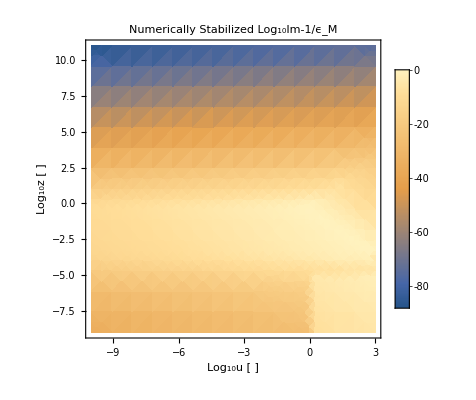

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-10,3},{z,-9,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

```mathematica
LargeuνϵAssoc/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->10/.FeTotalparams[[2]]//N
ϵM[u,z,uν]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->10/.FeTotalparams[[2]]//N
```

<|ϵCm1→7.53588+0.0123351 ⅈ,ϵ0m1→3.37517×10^9,Denom→10.+0.0000272809 ⅈ,Num→-75.3588+92077.8 ⅈ,ϵm1→-7.51076+9207.78 ⅈ,Imϵ→Imϵ|>

3.21755×10^8+9.92649×10^8 ⅈ

It looks like the issue is at leading orders, uν z appear together - which is O(1). So we should expand in large u instead.

Okay that didn’t work either, what about the large u limit?

```mathematica
LargeuϵAssoc = Block[{order=4,ϵCm1,ϵ0m1,Denom,Num,ϵm1,Imϵ,Assoc},

ϵCm1="χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]));
ϵCm1=Assuming[{z<1,u>0},Series[ϵCm1,{u,∞,order}]//PowerExpand//Simplify]//Normal;

ϵ0m1=("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
ϵ0m1=Assuming[{z<1,u>0},Series[ϵ0m1,{u,∞,order}]//PowerExpand//Simplify]//Normal;

Num=Assuming[{z<1,u>0},Series[(u+I uν)ϵCm1,{u,∞,order}]//PowerExpand//Simplify]//Normal;
Denom=Assuming[{z<1,u>0},Series[u + I uν ϵCm1/ϵ0m1,{u,∞,order}]//PowerExpand//Simplify]//Normal;

(*ϵm1=Assuming[{z>1,u>0},Series[((u+I uν)ϵCm1)/(u + I uν ϵCm1/ϵ0m1),{z,∞,8}]//PowerExpand//Simplify]//Normal;*)
ϵm1=Assuming[{z<1,u>0},Series[Num/Denom,{u,∞,order}]//PowerExpand//Simplify]//Normal;
(*Imϵ = Assuming[{"χ",z}∈ Reals,Im[ϵm1]//ComplexExpand//Simplify];*)
(*Assuming["χ"∈ Reals,Im[-1/(1+%%)]//ComplexExpand//FullSimplify];*)

Assoc = <|"ϵCm1"->ϵCm1,"ϵ0m1"->ϵ0m1,"Denom"->Denom,"Num"->Num,"ϵm1"->ϵm1,"Imϵ"->Imϵ|>
(*Print[Assoc];*)
(*Assoc*)
]
```

<|ϵCm1→-χ^2/(3 u^2 z^2)+(2 ⅈ χ^2 uν)/(3 u^3 z^2)-(χ^2 (3-15 uν^2+5 z^2))/(15 u^4 z^2),ϵ0m1→(χ^2 (2 z-(-1+z^2) Log[Abs[1+z]/(1-z)]))/(4 z^3),Denom→u-(4 ⅈ uν z (3-15 uν^2+5 z^2))/(15 u^4 (2 z+(-1+z^2) Log[(1-z)/Abs[1+z]]))-(4 ⅈ uν z)/(u^2 (6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]]))-(8 uν^2 z)/(u^3 (6 z+3 (-1+z^2) Log[(1-z)/Abs[1+z]])),Num→-χ^2/(3 u z^2)+(ⅈ χ^2 uν)/(3 u^2 z^2)+(ⅈ χ^2 uν (-3+15 uν^2-5 z^2))/(15 u^4 z^2)-(χ^2 (3-5 uν^2+5 z^2))/(15 u^3 z^2),ϵm1→-χ^2/(3 u^2 z^2)+(ⅈ χ^2 uν)/(3 u^3 z^2)-(χ^2 (3-5 uν^2+5 z^2))/(15 u^4 z^2),Imϵ→Imϵ|>

```mathematica
LargeuϵAssoc/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-6/.u->10/.FeTotalparams[[2]]//N
ϵM[u,z,uν]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-6/.u->10/.FeTotalparams[[2]]//N
```

<|ϵCm1→5.03891×10^17+2.74932×10^13 ⅈ,ϵ0m1→3.37517×10^11,Denom→-9.95288×10^6+1.82415×10^11 ⅈ,Num→1.67964×10^18+6.15682×10^22 ⅈ,ϵm1→1.67964×10^17+1.37466×10^13 ⅈ,Imϵ→Imϵ|>

3.37517×10^11+1.99619×10^8 ⅈ

Okay this still isn’t working. What about small z, but we include the factor of z in uν explicitly.

```mathematica
smallzϵAssoc = Block[{order=2,ϵCm1,ϵ0m1,Denom,Num,ϵm1,Imϵ,Assoc},

ϵCm1="χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uνp/z]-Ζ[u-z,uνp/z]));
ϵCm1=Assuming[{z<1,u>0},Series[ϵCm1,{z,0,order}]//PowerExpand//Simplify]//Normal;

ϵ0m1=("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
ϵ0m1=Assuming[{z<1,u>0},Series[ϵ0m1,{z,0,order}]//PowerExpand//Simplify]//Normal;

Num=Assuming[{z<1,u>0},Series[(u+I uνp/z)ϵCm1,{z,0,order}]//PowerExpand//Simplify]//Normal;
Denom=Assuming[{z<1,u>0},Series[u + I uνp/z ϵCm1/ϵ0m1,{z,0,order}]//PowerExpand//Simplify]//Normal;

(*ϵm1=Assuming[{z>1,u>0},Series[((u+I uν)ϵCm1)/(u + I uν ϵCm1/ϵ0m1),{z,∞,8}]//PowerExpand//Simplify]//Normal;*)
ϵm1=Assuming[{z<1,u>0},Series[Num/Denom,{z,0,order}]//PowerExpand//Simplify]//Normal;
(*Imϵ = Assuming["χ"∈ Reals,Im[ϵm1]//ComplexExpand//Simplify];*)
(*Assuming["χ"∈ Reals,Im[-1/(1+%%)]//ComplexExpand//FullSimplify];*)

Assoc = <|"ϵCm1"->ϵCm1,"ϵ0m1"->ϵ0m1,"Denom"->Denom,"Num"->Num,"ϵm1"->ϵm1,"Imϵ"->Imϵ|>
(*Print[Assoc];*)
(*Assoc*)
]
```

<|ϵCm1→χ^2/(3 uνp^2)+(2 ⅈ χ^2 u z)/(3 uνp^3)-(χ^2 (1+5 u^2) z^2)/(5 uνp^4),ϵ0m1→-χ^2/3+χ^2/z^2-(χ^2 z^2)/15,Denom→u+(ⅈ z)/(3 uνp)-(2 u z^2)/(3 uνp^2),Num→-(χ^2 u)/(3 uνp^2)+(ⅈ χ^2)/(3 uνp z)-(ⅈ χ^2 (3+5 u^2) z)/(15 uνp^3)-(χ^2 u (1+5 u^2) z^2)/(5 uνp^4),ϵm1→(χ^2 (1-3 u^2))/(9 u^2 uνp^2)+(ⅈ χ^2)/(3 u uνp z)-(ⅈ χ^2 (5-18 u^2+45 u^4) z)/(135 u^3 uνp^3)-(χ^2 (5-48 u^2+216 u^4+405 u^6) z^2)/(405 u^4 uνp^4),Imϵ→Imϵ|>

```mathematica
smallzϵAssoc/.uνp->uν z/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->100/.FeTotalparams[[2]]//N
ϵM[u,z,uν]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-5/.u->100/.FeTotalparams[[2]]//N
```

<|ϵCm1→7.53436+0.123351 ⅈ,ϵ0m1→3.37517×10^9,Denom→100.+0.0000272809 ⅈ,Num→-753.739+92071.5 ⅈ,ϵm1→-7.53714+920.715 ⅈ,Imϵ→Imϵ|>

-1.09714×10^6+1.63011×10^7 ⅈ

```mathematica
"χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]))
%/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-6/.u->10/.FeTotalparams[[2]]//N
(*("χ")^2/(3 uνp^2)+(2 ⅈ ("χ")^2 u z)/(3 uνp^3)-(("χ")^2 (1+5 u^2) z^2)/(5 uνp^4)*)("χ")^2/(3 uνp^2)+(2 ⅈ ("χ")^2 u z)/(3 uνp^3)-(("χ")^2 (1+5 u^2) z^2)/(5 uνp^4)/.uνp->uν z/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-6/.u->10/.FeTotalparams[[2]]//N(*small z*)
-("χ")^2/(3 u^2 z^2)+(2 ⅈ ("χ")^2 uν)/(3 u^3 z^2)-(("χ")^2 (3-15 uν^2+5 z^2))/(15 u^4 z^2)/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-6/.u->10/.FeTotalparams[[2]]//N(*large u*)
(2 ⅈ ("χ")^2 u)/(3 uν^3 z^2)+("χ")^2/(3 uν^2 z^2)/.uν->("νi")/(2 "qF" "vF"z)/.z->10^-6/.u->10/.FeTotalparams[[2]](*large uν*)
"So large uν = small z and none agree with the actual value"
```

1/(4 z^3)χ^2 (2 z-uν (u-z) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+uν (u+z) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/4 (1+uν^2-(u-z)^2) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/4 (1+uν^2-(u+z)^2) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)]+ⅈ (-1/2 (1+uν^2-(u-z)^2) (-ArcTan[(1+u-z)/uν]-ArcTan[(1-u+z)/uν])+1/2 (1+uν^2-(u+z)^2) (-ArcTan[(1-u-z)/uν]-ArcTan[(1+u+z)/uν])-1/2 uν (-u+z) Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 uν (-u-z) Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)]) Sign[u])

4.10281×10^10-1.89865×10^7 ⅈ

7.53588+0.00123351 ⅈ

5.03891×10^17+2.74932×10^13 ⅈ

7.53588+0.00123351 ⅈ

```mathematica
"So large uν = small z and none agree with the actual value"
"this value computed with ϵM is incorrect because it is unstable there."
```

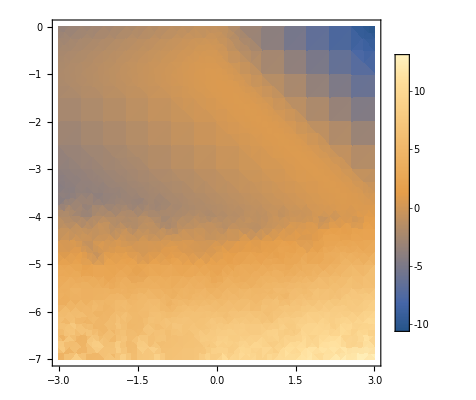

```mathematica
DensityPlot[Log10@Abs@Im@("χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]))/.uν->("νi")/(2 "qF" "vF"z)/.z->10^zt/.u->10^ut/.FeTotalparams[[2]]),{ut,-3,3},{zt,-7,0},PlotLegends->Automatic,WorkingPrecision->50]
```

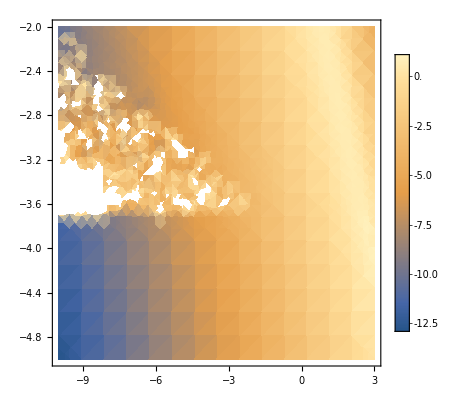

```mathematica
DensityPlot[Log10@Im@(If[z<10^-3.7&&("χ")^2/(3 z^2)>10 u^2,(2 ⅈ ("χ")^2 u)/(3 uν^3 z^2)+("χ")^2/(3 uν^2 z^2),"χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]))]/.uν->("νi")/(2 "qF" "vF"z)/.z->10^zt/.u->10^ut/.FeTotalparams[[2]]),{ut,-10,3},{zt,-5,-2},PlotLegends->Automatic,WorkingPrecision->50](*second condition is asymptotic plasmon line dispersion relation from Lindhard (10)*)
```

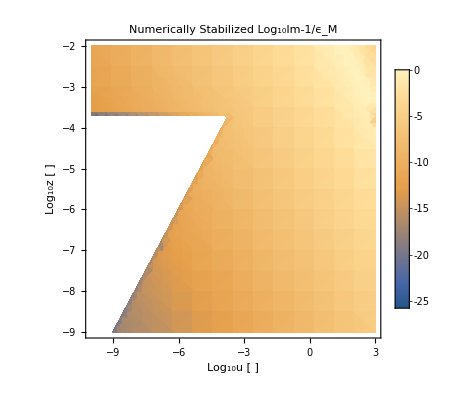

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-10,3},{z,-9,-2},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

```mathematica
Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]]/.u->-9/.z->-6
```

-2.98426×10^-21

```mathematica
ϵMsmallz[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.u->-9/.z->-6
Im[-1/%]/.FeTotalparams[[1]]
```

1+(8.68541×10^17-8.09441×10^20 ⅈ) χ^2

-2.98426×10^-21

```mathematica
Assuming[{"χ"∈ Reals},ComplexExpand[Im[ϵMsmallz[u,z,uν]]]//Simplify]
Solve[%==0,u][[4]]
(*Series[u/.Solve[%==0,u],{z,0,1}]//Normal*)
Series[u/.%,{uν,∞,4}]//Normal//PowerExpand//Simplify
Series[%/.uν->uνp/z,{z,0,1}]//Normal//Simplify
%/.uνp->uν z
%/.uν->("νi")/(2 "qF" "vF" z)/.FeTotalparams[[1]]/.z->10^(-4)
```

(χ^2 (-3+54 u^4-2 z^2+9 u^2 (3+3 uν^2+z^2)))/(81 u^3 uν^3 z^2)

{u→√(-1/4-uν^2/4-z^2/12+1/108 √(-216 (-3-2 z^2)+(27+27 uν^2+9 z^2)^2))}

-(√(1+(2 z^2)/3) (3-6 uν^2+z^2))/(18 uν^3)

z/(3 uνp)

1/(3 uν)

0.0000931956

So boundary where our expansion is valid is roughly  u >1/(3 uν)

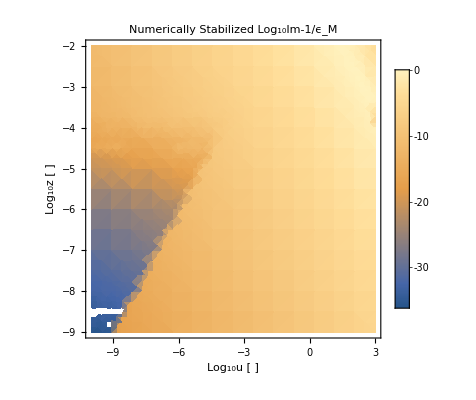

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-10,3},{z,-9,-2},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

We also need to use a small u limit below this line

#### Small u and z limit of ϵM

```mathematica
smalluϵAssoc = Block[{order=2,ϵCm1,ϵ0m1,Denom,Num,ϵm1,Imϵ,Assoc},

ϵCm1="χ"^2/(4 z^3) {1,I}.({{1,0},{0,Sign[u]}} . (Ζ[u+z,uν]-Ζ[u-z,uν]));
ϵCm1=Assuming[{z<1,u>0},Series[ϵCm1,{u,0,order}]//PowerExpand//Simplify]//Normal;

ϵ0m1=("χ")^2/(4 z^3)(2 z + (1 - z^2)Log[Abs[(1+z)/(1-z)]]);
ϵ0m1=Assuming[{z<1,u>0},Series[ϵ0m1,{u,0,order}]//PowerExpand//Simplify]//Normal;

Num=Assuming[{z<1,u>0},Series[(u+I uν)ϵCm1,{u,0,order}]//PowerExpand//Simplify]//Normal;
Denom=Assuming[{z<1,u>0},Series[u + I uν ϵCm1/ϵ0m1,{u,0,order}]//PowerExpand//Simplify]//Normal;

(*ϵm1=Assuming[{z>1,u>0},Series[((u+I uν)ϵCm1)/(u + I uν ϵCm1/ϵ0m1),{z,∞,8}]//PowerExpand//Simplify]//Normal;*)
ϵm1=Assuming[{z<1,u>0},Series[Num/Denom,{u,0,order}]//PowerExpand//Simplify]//Normal;
(*Imϵ = Assuming[{"χ",z}∈ Reals,Im[ϵm1]//ComplexExpand//Simplify];*)
(*Assuming["χ"∈ Reals,Im[-1/(1+%%)]//ComplexExpand//FullSimplify];*)

Assoc = <|"ϵCm1"->ϵCm1,"ϵ0m1"->ϵ0m1,"Denom"->Denom,"Num"->Num,"ϵm1"->ϵm1,"Imϵ"->Imϵ|>
(*Print[Assoc];*)
(*Assoc*)
]
```

<|ϵCm1→(ⅈ χ^2 u (2 z ArcTan[(1-z)/uν]+2 z ArcTan[(1+z)/uν]+uν (Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2])))/(4 z^3)+1/(8 z^3)χ^2 (4 z-4 uν z ArcTan[(1-z)/uν]-4 uν z ArcTan[(1+z)/uν]-Log[uν^2+(-1+z)^2]-uν^2 Log[uν^2+(-1+z)^2]+z^2 Log[uν^2+(-1+z)^2]+Log[uν^2+(1+z)^2]+uν^2 Log[uν^2+(1+z)^2]-z^2 Log[uν^2+(1+z)^2])+(χ^2 u^2 (4 z (-1+uν^2+z^2)+(uν^4+(-1+z^2)^2+2 uν^2 (1+z^2)) Log[uν^2+(-1+z)^2]-(uν^4+(-1+z^2)^2+2 uν^2 (1+z^2)) Log[uν^2+(1+z)^2]))/(8 (uν^2+(-1+z)^2) z^3 (uν^2+(1+z)^2)),ϵ0m1→(χ^2 (2 z-(-1+z^2) Log[Abs[1+z]/(1-z)]))/(4 z^3),Denom→(ⅈ u^2 uν (4 z (-1+uν^2+z^2)+(uν^4+(-1+z^2)^2+2 uν^2 (1+z^2)) Log[uν^2+(-1+z)^2]-(uν^4+(-1+z^2)^2+2 uν^2 (1+z^2)) Log[uν^2+(1+z)^2]))/(2 (uν^2+(-1+z)^2) (uν^2+(1+z)^2) (2 z+(-1+z^2) Log[(1-z)/Abs[1+z]]))-1/(4 z+2 (-1+z^2) Log[(1-z)/Abs[1+z]])ⅈ uν (-4 z+4 uν z ArcTan[(1-z)/uν]+4 uν z ArcTan[(1+z)/uν]+Log[uν^2+(-1+z)^2]+uν^2 Log[uν^2+(-1+z)^2]-z^2 Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2]-uν^2 Log[uν^2+(1+z)^2]+z^2 Log[uν^2+(1+z)^2])+u (1-(uν (2 z ArcTan[(1-z)/uν]+2 z ArcTan[(1+z)/uν]+uν (Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2])))/(2 z+(-1+z^2) Log[(1-z)/Abs[1+z]])),Num→1/(8 z^3)χ^2 u (4 z-8 uν z ArcTan[(1-z)/uν]-8 uν z ArcTan[(1+z)/uν]-Log[uν^2+(-1+z)^2]-3 uν^2 Log[uν^2+(-1+z)^2]+z^2 Log[uν^2+(-1+z)^2]+Log[uν^2+(1+z)^2]+3 uν^2 Log[uν^2+(1+z)^2]-z^2 Log[uν^2+(1+z)^2])-1/(8 z^3)ⅈ χ^2 uν (-4 z+4 uν z ArcTan[(1-z)/uν]+4 uν z ArcTan[(1+z)/uν]+Log[uν^2+(-1+z)^2]+uν^2 Log[uν^2+(-1+z)^2]-z^2 Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2]-uν^2 Log[uν^2+(1+z)^2]+z^2 Log[uν^2+(1+z)^2])+1/(8 z^3)ⅈ χ^2 u^2 (4 z ArcTan[(1-z)/uν]+4 z ArcTan[(1+z)/uν]+2 uν (Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2])+(uν (4 z (-1+uν^2+z^2)+(uν^4+(-1+z^2)^2+2 uν^2 (1+z^2)) Log[uν^2+(-1+z)^2]-(uν^4+(-1+z^2)^2+2 uν^2 (1+z^2)) Log[uν^2+(1+z)^2]))/((uν^2+(-1+z)^2) (uν^2+(1+z)^2))),ϵm1→(χ^2 (2 z+(-1+z^2) Log[(1-z)/Abs[1+z]]))/(4 z^3)-(ⅈ χ^2 u (4 uν z ArcTan[(1-z)/uν]+4 uν z ArcTan[(1+z)/uν]+Log[uν^2+(-1+z)^2]+uν^2 Log[uν^2+(-1+z)^2]-z^2 Log[uν^2+(-1+z)^2]-2 Log[1-z]+2 z^2 Log[1-z]-Log[uν^2+(1+z)^2]-uν^2 Log[uν^2+(1+z)^2]+z^2 Log[uν^2+(1+z)^2]+2 Log[Abs[1+z]]-2 z^2 Log[Abs[1+z]]) (2 z+(-1+z^2) Log[1-z]-(-1+z^2) Log[Abs[1+z]]))/(4 uν z^3 (-4 z+4 uν z ArcTan[(1-z)/uν]+4 uν z ArcTan[(1+z)/uν]+Log[uν^2+(-1+z)^2]+uν^2 Log[uν^2+(-1+z)^2]-z^2 Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2]-uν^2 Log[uν^2+(1+z)^2]+z^2 Log[uν^2+(1+z)^2]))+(χ^2 u^2 ((-1+uν^2+z^2) Log[uν^2+(-1+z)^2]-2 (-1+z^2) Log[1-z]+Log[uν^2+(1+z)^2]-uν^2 Log[uν^2+(1+z)^2]-z^2 Log[uν^2+(1+z)^2]-2 Log[Abs[1+z]]+2 z^2 Log[Abs[1+z]]) (2 z+(-1+z^2) Log[1-z]-(-1+z^2) Log[Abs[1+z]])^2)/(2 uν^2 z^3 (-4 z+4 uν z ArcTan[(1-z)/uν]+4 uν z ArcTan[(1+z)/uν]+Log[uν^2+(-1+z)^2]+uν^2 Log[uν^2+(-1+z)^2]-z^2 Log[uν^2+(-1+z)^2]-Log[uν^2+(1+z)^2]-uν^2 Log[uν^2+(1+z)^2]+z^2 Log[uν^2+(1+z)^2])^2),Imϵ→Imϵ|>

```mathematica
Assuming[0<z<1,Series[smalluϵAssoc["ϵm1"]/.uν->uνp/z,{z,0,2}]//Normal//Simplify]/.uνp->uν z//Simplify
Assuming["χ"∈ Reals,Im[-1/%]//ComplexExpand//Simplify]
%/.uν->("νi")/(2 "qF" "vF" z)/.FeTotalparams[[1]]/.z->10^(-5)/.u->10^(-8)
```

-1/(2625 uν^4 z^2)χ^2 (175 uν^4 (-15+5 z^2+z^4)+5 ⅈ u uν (108-140 uν^2 (3+8 z^2)+35 uν^4 (-45+30 z^2+z^4))+u^2 (-828-540 uν^2 (-1+36 z^2)-105 uν^4 (-45-330 z^2+409 z^4)+25 uν^6 (945-945 z^2+126 z^4+10 z^6)))

N::precsm: Requested precision 50 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

-((13125 u uν^5 z^2 (108-140 uν^2 (3+8 z^2)+35 uν^4 (-45+30 z^2+z^4)))/(χ^2 (30625 uν^8 (-15+5 z^2+z^4)^2+u^4 (828+540 uν^2 (-1+36 z^2)+105 uν^4 (-45-330 z^2+409 z^4)-25 uν^6 (945-945 z^2+126 z^4+10 z^6))^2+25 u^2 uν^2 (11664-504 uν^2 (-165+595 z^2+23 z^4)-280 uν^4 (990-18885 z^2+326 z^4+972 z^6)-490 uν^6 (-675+8775 z^2-18630 z^4+5305 z^6+1227 z^8)+175 uν^8 (-14175+18900 z^2-5670 z^4-510 z^6+359 z^8+20 z^10)))))

2.59196×10^-13

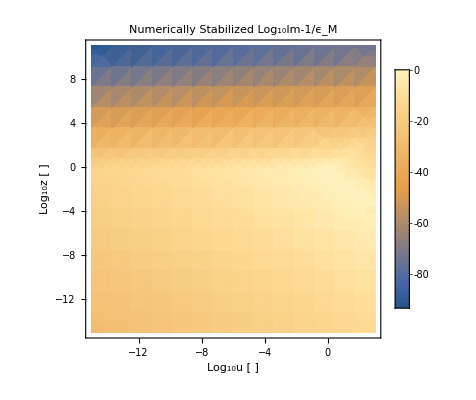

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-15,3},{z,-15,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

```mathematica
Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]]/.z->-5/.u->-9
```

2.59195×10^-14

```mathematica
((z<10^(-3.7)&&("χ")^2/(3 z^2)>10 up^2)&& up > 1/(3 uν)/.up->10^u/.z->10^z)/.uν->("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]/.z->-5/.u->-9
```

False

#### Plot of the on-shell line

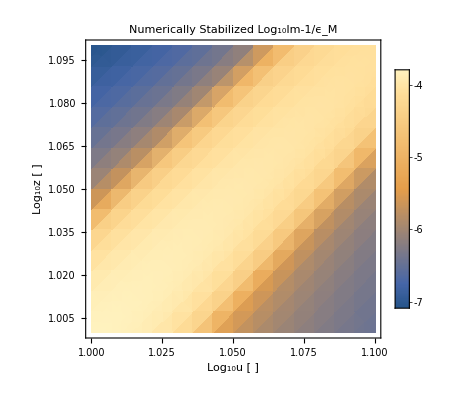

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,1,1.1},{z,1,1.1},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

```mathematica
10^1.041
```

10.9901

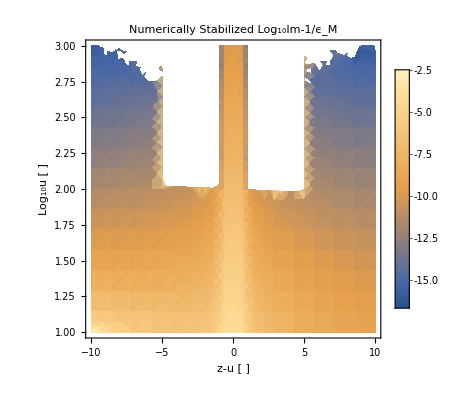

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^u + zmu,("νi")/(2 "qF" "vF"(10^u + zmu))/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{zmu,-10,10},{u,1,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"z-u [ ]","Log_10u [ ]"}]
```

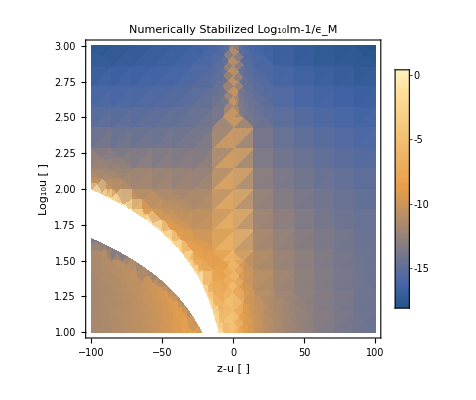

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^u + zmu,("νi")/(2 "qF" "vF"(10^u + zmu))/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{zmu,-100,100},{u,1,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"z-u [ ]","Log_10u [ ]"}]
```

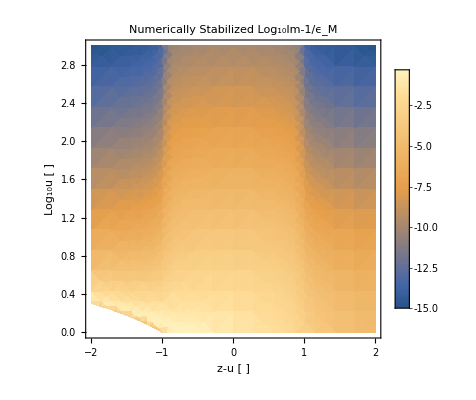

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^u + zmu,("νi")/(2 "qF" "vF"(10^u + zmu))/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{zmu,-2,2},{u,0,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"z-u [ ]","Log_10u [ ]"}]
```

So it works better without the near z=u expansion. Here’s the corrected version

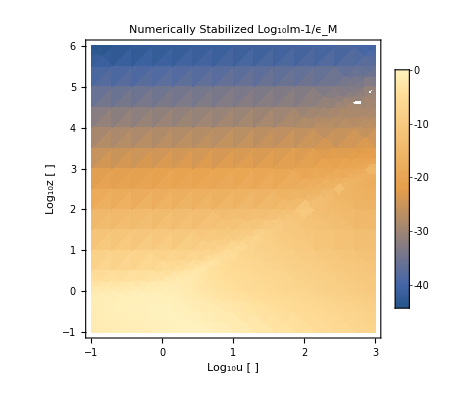

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-1,3},{z,-1,6},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

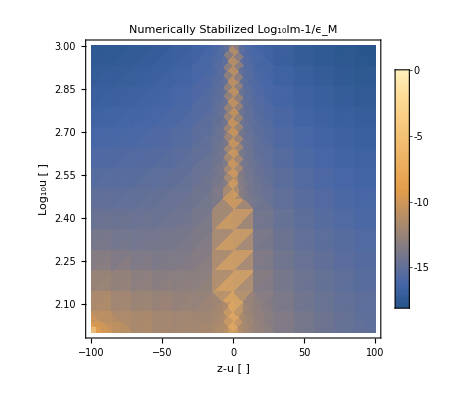

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^u + zmu,("νi")/(2 "qF" "vF"(10^u + zmu))/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{zmu,-100,100},{u,2,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"z-u [ ]","Log_10u [ ]"},PlotRange->All]
```

That white region, is z going negative, just due to our parametrization. 

Here is the plasmon line

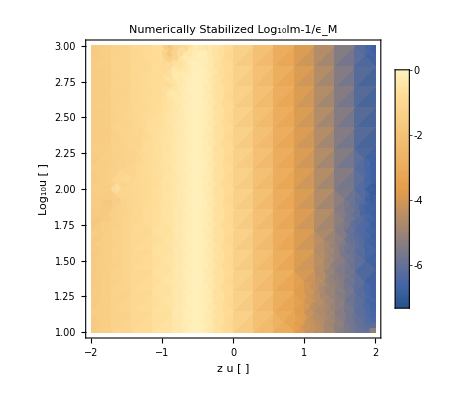

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u, 10^-u(10^c) ,("νi")/(2 "qF" "vF"(10^(-u+c) ))/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{c,-2,2},{u,1,3},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"z u [ ]","Log_10u [ ]"},PlotRange->All]
```

```mathematica
z= c/u
```

#### Maximum value of u and z

```mathematica
"u is given by ω/(k SubscriptBox[v, F]), and k ∈ (k_-,k_+) where ℏk_± = mχvχ ± √(2 mχ (FractionBox[mχ, 2] SuperscriptBox[vχ, 2]  -  ω ℏ)) 
We want to know the variation with mχ given a fixed maximum on vχ. 

First we must disentangle ω and k since the k range is dependent on ω. We can do that by noting ω ∈ (0,mχ/(2 ℏ)vχ^2). 
	k_- is monotinically increasing with ω from 0 to mχvχ
	k_+ is monotonically decreasing with ω from 2 mχvχ to mχvχ

First thing is that since k_- can vanish, we want to understand the behaviour there. So we look at the ω->0 limit of k_- and u(k_-). For k_-"
km=1/("ℏ")(mχ vχ- √(2 mχ (mχ/2 vχ^2 - ω "ℏ")))
Series[km,{ω,0,2}]//PowerExpand//Simplify//Normal
"Which gives for u(k_-)"
 ω/(k "vF")/.k->%%//Simplify
Series[%,{ω,0,2}]
"So in the limit of small ω we maximize u (approach the high mass limit upper bound on u). 
What about the other limit of large ω?"
```

u is given by ω/(k SubscriptBox[v, F]), and k ∈ (k_-,k_+) where ℏk_± = mχvχ ± √(2 mχ (FractionBox[mχ, 2] SuperscriptBox[vχ, 2]  -  ω ℏ)) 
We want to know the variation with mχ given a fixed maximum on vχ. 

First we must disentangle ω and k since the k range is dependent on ω. We can do that by noting ω ∈ (0,mχ/(2 ℏ)vχ^2). 
	k_- is monotinically increasing with ω from 0 to mχvχ
	k_+ is monotonically decreasing with ω from 2 mχvχ to mχvχ

First thing is that since k_- can vanish, we want to understand the behaviour there. So we look at the ω->0 limit of k_- and u(k_-). For k_-

(mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ℏ ω)))/ℏ

ω/vχ+(ℏ ω^2)/(2 mχ vχ^3)

Which gives for u(k_-)

(2 mχ vχ^3)/(2 vF mχ vχ^2+vF ℏ ω)

vχ/vF-(ℏ ω)/(2 (vF mχ vχ))+(ℏ^2 ω^2)/(4 vF mχ^2 vχ^3)+O[ω]^3

So in the limit of small ω we maximize u (approach the high mass limit upper bound on u). 
What about the other limit of large ω?

```mathematica
"The way to do this is to exteremize u on the interior of the parabola in the upper half plane ω ∈ (0,mχ/(2 ℏ)vχ^2), k ∈ (k_-,k_+). First look for extrema on the interior, then check the boundaries. On the interior. We've already checked the k->0 limit (implies the ω -> 0 limit) and it's finite and bounded by v/v_F. There is no extremum in the interior of the region. it also vanishes identically for ω=0, k≠0. So we need only check the boundaries (ω,k_±(ω)). We look to extremize the function"
 ω/(k "vF")/.k->{1/("ℏ")(mχ vχ- √(2 mχ (mχ/2 vχ^2 - ω "ℏ"))),1/("ℏ")(mχ vχ+ √(2 mχ (mχ/2 vχ^2 - ω "ℏ")))}
"Which has derivatives"
{D[%%[[1]],ω],D[%%[[2]],ω]}//Simplify
"This tells us that on the k_- line u is monotonically decreasing, and along the k_+ line u is monotinically increasing.

At ω = mχ/(2 ℏ) vχ^2 we also clearly have"

 ω/(k "vF")/.k->{1/("ℏ")(mχ vχ- √(2 mχ (mχ/2 vχ^2 - ω "ℏ"))),1/("ℏ")(mχ vχ+ √(2 mχ (mχ/2 vχ^2 - ω "ℏ")))}/.ω->mχ/(2 "ℏ") vχ^2 

"So we have explicitly shown that u ∈ (0,v/v_F)"
```

The way to do this is to exteremize u on the interior of the parabola in the upper half plane ω ∈ (0,mχ/(2 ℏ)vχ^2), k ∈ (k_-,k_+). First look for extrema on the interior, then check the boundaries. On the interior. We've already checked the k->0 limit (implies the ω -> 0 limit) and it's finite and bounded by v/v_F. There is no extremum in the interior of the region. it also vanishes identically for ω=0, k≠0. So we need only check the boundaries (ω,k_±(ω)). We look to extremize the function

{(ℏ ω)/(vF (mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ℏ ω)))),(ℏ ω)/(vF (mχ vχ+√2 √(mχ ((mχ vχ^2)/2-ℏ ω))))}

Which has derivatives

{-ℏ/(2 vF √(mχ (mχ vχ^2-2 ℏ ω))),ℏ/(2 vF √(mχ (mχ vχ^2-2 ℏ ω)))}

This tells us that on the k_- line u is monotonically decreasing, and along the k_+ line u is monotinically increasing.

At ω = mχ/(2 ℏ) vχ^2 we also clearly have

{vχ/(2 vF),vχ/(2 vF)}

So we have explicitly shown that u ∈ (0,v/v_F)

```mathematica
"Now what is the range of v/v_F for the materials we consider given that the upper bound on v is 0.2 c?"
(0.2"c")/("vF")/.FeTotalparams
(0.2"c")/("vF")/.SiO2Totalparams 
(0.2"c")/("vF")/.MgOTotalparams 
"So for all materials we consider, u ≤ v/v_F < 100"
```

Now what is the range of v/v_F for the materials we consider given that the upper bound on v is 0.2 c?

{35.6351,29.0534,22.1136,11.3901,2.24524,0.489676}

{22.5979,13.2656}

{31.4926,23.5832,22.0631,14.2643}

So for all materials we consider, u ≤ v/v_F < 100

```mathematica
D[ω/(1 - √(1 - 2(ω ℏ)/(mχ vχ^2))),ω]//Simplify
```

-(mχ vχ^2 √(1-(2 ω ℏ)/(mχ vχ^2)))/(2 mχ vχ^2-4 ω ℏ)

```mathematica
D[1/(mχ vχ)ω/(1 - √(1 - 2(ω ℏ)/(mχ vχ^2))),mχ]//Simplify
```

(vχ ω √(1-(2 ω ℏ)/(mχ vχ^2)))/(2 mχ (mχ vχ^2-2 ω ℏ))

#### maximum value of z

```mathematica
"The maximum value of z is simply given by z_+(ω=0) which is"
zmax=(2 mχ vχ)/(2 "qF" "ℏ")
"So for non-relativistic probe we have"
zmax /. vχ->0.2"c"/.mχ->10^6 mχMeV("JpereV")/("c")^2/.FeTotalparams
zmax /. vχ->0.2"c"/.mχ->10^6 mχMeV("JpereV")/("c")^2/.SiO2Totalparams
zmax /. vχ->0.2"c"/.mχ->10^6 mχMeV("JpereV")/("c")^2/.MgOTotalparams
"Which for the maximum mass of a PeV is order 10^11"
zmax /. vχ->0.2"c"/.mχ->10^6 mχMeV("JpereV")/("c")^2/.FeTotalparams/.mχMeV->10^9
zmax /. vχ->0.2"c"/.mχ->10^6 mχMeV("JpereV")/("c")^2/.SiO2Totalparams/.mχMeV->10^9
zmax /. vχ->0.2"c"/.mχ->10^6 mχMeV("JpereV")/("c")^2/.MgOTotalparams/.mχMeV->10^9
```

The maximum value of z is simply given by z_+(ω=0) which is

(mχ vχ)/(qF ℏ)

So for non-relativistic probe we have

{69.6273 mχMeV,56.7673 mχMeV,43.2078 mχMeV,22.255 mχMeV,4.38697 mχMeV,0.956777 mχMeV}

{44.1541 mχMeV,25.9196 mχMeV}

{61.5334 mχMeV,46.0791 mχMeV,43.109 mχMeV,27.8709 mχMeV}

Which for the maximum mass of a PeV is order 10^11

{6.96273×10^10,5.67673×10^10,4.32078×10^10,2.2255×10^10,4.38697×10^9,9.56777×10^8}

{4.41541×10^10,2.59196×10^10}

{6.15334×10^10,4.60791×10^10,4.3109×10^10,2.78709×10^10}

```mathematica
" What about with ω_min = ω_edge?"
1/(2 "qF""ℏ")(mχ vχ+√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.FeTotalparams[[2]]
Table[%,{m,6,15}]
"This is the same as above, since ωedgei ℏ << mχ vχmax^2/2"
```

What about with ω_min = ω_edge?

2.65764×10^23 (1.068×10^-28 10^m+1.8868×10^-18 √(10^m (-6.95108×10^-22+3.204×10^-21 10^m)))

{56.7672,567.673,5676.73,56767.3,567673.,5.67673×10^6,5.67673×10^7,5.67673×10^8,5.67673×10^9,5.67673×10^10}

This is the same as above, since ωedgei ℏ << mχ vχmax^2/2

```mathematica
"look for smallest range"
1/(2 "qF""ℏ")(mχ vχ+√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.m->6/.FeTotalparams
1/(2 "qF""ℏ")(mχ vχ+√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.m->6/.SiO2Totalparams
1/(2 "qF""ℏ")(mχ vχ+√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.m->6/.MgOTotalparams
```

look for smallest range

{69.6269,56.7672,43.2077,22.255,4.34723,0.860546}

{44.1491,25.9167}

{61.5274,46.0747,43.1048,27.8682}

```mathematica
"look for smallest range"
1/(2 "qF""ℏ")(mχ vχ-√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.m->6/.FeTotalparams
1/(2 "qF""ℏ")(mχ vχ-√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.m->6/.SiO2Totalparams
1/(2 "qF""ℏ")(mχ vχ-√(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.m->6/.MgOTotalparams
```

look for smallest range

{0.000346491,3.07891×10^-6,0.000107764,0.0000278188,0.0397385,0.0962313}

{0.00491269,0.00288388}

{0.00597701,0.00447587,0.00418737,0.00270723}

#### Minimum value of z and z_max/z_min

```mathematica
D[(mχ vχ- √(2 mχ (mχ/2 vχ^2 - "ωedgei" "ℏ"))),vχ]//PowerExpand
```

mχ-(mχ^(3/2) vχ)/(√2 √(-ωedgei ℏ+(mχ vχ^2)/2))

```mathematica
mχ(1-1/(√(1-("ωedgei" "ℏ")/((mχ vχ^2)/2))))
"since ωedgei ℏ < mχ vχ^2/2 when scattering is kinematicially allowed, ∂_v_χ  z_- < 0 so to find the minimum value we want to take vχ->vχ_max"
```

```mathematica
"Minimum value of z is given by z_-(ω_min):"
1/(2 "qF""ℏ")(mχ vχ- √(2 mχ (mχ/2 vχ^2 - ω"ℏ")))/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.FeTotalparams[[2]]
Table[%,{m,6,15}]
```

Minimum value of z is given by z_-(ω_min):

2.65764×10^23 (1.068×10^-28 10^m-1.8868×10^-18 √(10^m (-6.95108×10^-22+3.204×10^-21 10^m)))

{3.07891×10^-6,3.07891×10^-6,3.07891×10^-6,3.07891×10^-6,3.07889×10^-6,3.07843×10^-6,3.07925×10^-6,3.09235×10^-6,2.93511×10^-6,3.35442×10^-6}

```mathematica
"So the ratio of z_min/z_max is"
1/((mχ vχ)/("qF" "ℏ"))1/(2 "qF""ℏ")(mχ vχ- √(2 mχ (mχ/2 vχ^2 - ω"ℏ")))//Simplify//PowerExpand
(*Assuming[vχ>0,%^2==(1/2(1-√(1-(2"ℏ"ω)/(mχ vχ^2))))^2//PowerExpand//FullSimplify]*)
"which gives z_max/z_min:"
(1/2(1-√(1-(2"ℏ"ω)/(mχ vχ^2))))^-1
%/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.FeTotalparams
Table[Ceiling@Log10@%,{m,6,15}]
```

So the ratio of z_min/z_max is

1/2 (1-(√(mχ vχ^2-2 ℏ ω))/(√mχ vχ))

which gives z_max/z_min:

2/(1-√(1-(2 ℏ ω)/(mχ vχ^2)))

{2/(1-√(1-19.9054 10^-m)),2/(1-√(1-0.21695 10^-m)),2/(1-√(1-9.97631 10^-m)),2/(1-√(1-5. 10^-m)),2/(1-√(1-35905. 10^-m)),2/(1-√(1-361850. 10^-m))}

{{6,8,6,6,3,1},{7,9,7,7,4,3},{8,10,8,8,5,4},{9,11,9,9,6,5},{10,12,10,10,7,6},{11,13,11,11,8,7},{12,14,12,12,9,8},{13,15,13,13,10,9},{14,16,14,14,11,10},{15,17,15,15,12,11}}

```mathematica
"Or with the more precise zmax the ratio of z_min/z_max is"
(1/(2 "qF""ℏ")(mχ vχ+ √(2 mχ (mχ/2 vχ^2 - ω"ℏ"))))/(1/(2 "qF""ℏ")(mχ vχ- √(2 mχ (mχ/2 vχ^2 - ω"ℏ"))))//Simplify//PowerExpand
(*Assuming[vχ>0,%^2==(1/2(1-√(1-(2"ℏ"ω)/(mχ vχ^2))))^2//PowerExpand//FullSimplify]*)
"which gives z_max/z_min:"
(1+√(1-(2"ℏ"ω)/(mχ vχ^2)))/(1-√(1-(2"ℏ"ω)/(mχ vχ^2)))
%/.vχ->0.2 "c"/.ω->"ωedgei"/.mχ->10^m("JpereV")/("c")^2/.FeTotalparams
Table[Ceiling@Log10@%,{m,6,15}]
```

Or with the more precise zmax the ratio of z_min/z_max is

(mχ vχ+√mχ √(mχ vχ^2-2 ℏ ω))/(mχ vχ-√mχ √(mχ vχ^2-2 ℏ ω))

which gives z_max/z_min:

(1+√(1-(2 ℏ ω)/(mχ vχ^2)))/(1-√(1-(2 ℏ ω)/(mχ vχ^2)))

{(1+√(1-19.9054 10^-m))/(1-√(1-19.9054 10^-m)),(1+√(1-0.21695 10^-m))/(1-√(1-0.21695 10^-m)),(1+√(1-9.97631 10^-m))/(1-√(1-9.97631 10^-m)),(1+√(1-5. 10^-m))/(1-√(1-5. 10^-m)),(1+√(1-35905. 10^-m))/(1-√(1-35905. 10^-m)),(1+√(1-361850. 10^-m))/(1-√(1-361850. 10^-m))}

{{6,8,6,6,3,1},{7,9,7,7,4,3},{8,10,8,8,5,4},{9,11,9,9,6,5},{10,12,10,10,7,6},{11,13,11,11,8,7},{12,14,12,12,9,8},{13,15,13,13,10,9},{14,16,14,14,11,10},{15,17,15,15,12,11}}

#### Minimum value of u

```mathematica
"u_min is given by (ℏ ω)/(vF mχ vχ (1  +  SqrtBox[1  -  2 FractionBox[ ω ℏ,  mχ SuperscriptBox[vχ, 2]]])). What value of ω minimizes this function?"
D[ω/(1 + √(1 - 2(ω ℏ)/(mχ vχ^2))),ω]//Simplify
"This is strictly positive, so monotonically increasing with ω, which tells us that we want to minimize ω. So put in ωmin. What value of vχ?"
D[(ℏ ω)/(vF mχ vχ(1 + √(1 - 2(ω ℏ)/(mχ vχ^2)))),vχ]
"Strictly negative, so monotonically decreasing with vχ, we want to maximize vχ. So the minimum value of u is"

("ℏ" ω)/("vF" mχ vχ(1 + √(1 - 2(ω "ℏ")/(mχ vχ^2))))/.ω->"ωedgei"/.mχ -> 10^15 ("JpereV")/("c")^2/.vχ->"c"0.2/.FeTotalparams
("ℏ" ω)/("vF" mχ vχ(1 + √(1 - 2(ω "ℏ")/(mχ vχ^2))))/.ω->"ωedgei"/.mχ -> 10^15 ("JpereV")/("c")^2/.vχ->"c"0.2/.SiO2Totalparams
("ℏ" ω)/("vF" mχ vχ(1 + √(1 - 2(ω "ℏ")/(mχ vχ^2))))/.ω->"ωedgei"/.mχ -> 10^15 ("JpereV")/("c")^2/.vχ->"c"0.2/.MgOTotalparams
```

u_min is given by (ℏ ω)/(vF mχ vχ (1  +  SqrtBox[1  -  2 FractionBox[ ω ℏ,  mχ SuperscriptBox[vχ, 2]]])). What value of ω minimizes this function?

(1+(ω ℏ)/(mχ vχ^2 √(1-(2 ω ℏ)/(mχ vχ^2)))+√(1-(2 ω ℏ)/(mχ vχ^2)))/((1+√(1-(2 ω ℏ)/(mχ vχ^2)))^2)

This is strictly positive, so monotonically increasing with ω, which tells us that we want to minimize ω. So put in ωmin. What value of vχ?

-(2 ω^2 ℏ^2)/(mχ^2 vF vχ^4 √(1-(2 ω ℏ)/(mχ vχ^2)) (1+√(1-(2 ω ℏ)/(mχ vχ^2)))^2)-(ω ℏ)/(mχ vF vχ^2 (1+√(1-(2 ω ℏ)/(mχ vχ^2))))

Strictly negative, so monotonically decreasing with vχ, we want to maximize vχ. So the minimum value of u is

{1.77332×10^-13,1.57578×10^-15,5.51532×10^-14,1.42376×10^-14,2.01538×10^-11,4.42974×10^-11}

{2.51402×10^-12,1.4758×10^-12}

{3.05872×10^-12,2.29052×10^-12,2.14288×10^-12,1.38542×10^-12}

#### Where values of u does ωedge truncate? - zmin

{0.0123472/z,0.0000894528/z,0.00238305/z,0.000316857/z,0.0884142/z,0.0423827/z}

{0.111004/z,0.0382522/z}

{0.188214/z,0.105545/z,0.0923774/z,0.0386129/z}

{0.0123472/z,0.0000894528/z,0.00238305/z,0.000316857/z,0.0884142/z,0.0423827/z,0.111004/z,0.0382522/z,0.188214/z,0.105545/z,0.0923774/z,0.0386129/z}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{0.0000123472},{8.94528×10^-8},{2.38305×10^-6},{3.16857×10^-7},{0.0000884142},{0.0000423827},{0.000111004},{0.0000382522},{0.000188214},{0.000105545},{0.0000923774},{0.0000386129}}

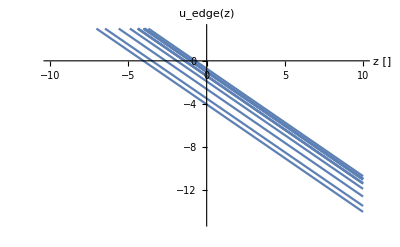

```mathematica
("ωedgei")/(2"qF""vF" z)/.FeTotalparams
("ωedgei")/(2"qF""vF" z)/.SiO2Totalparams
("ωedgei")/(2"qF""vF" z)/.MgOTotalparams
Join[%%%,%%,%]
Table[z/.Solve[10^3==%[[i]],z],{i,Length[%]}]
Plot[Log10@%%/.z->10^zt,{zt,-10,10},PlotRange->{-15,3},PlotLabel->"u_edge(z)",AxesLabel->{"z []"}]
```

```mathematica
"this sets a minimum value of z for each oscillator. "
```

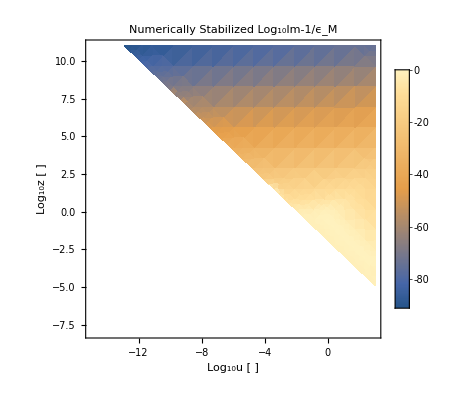

```mathematica
DensityPlot[Log10@(HeavisideTheta[10^u-(("ωedgei")/(2"qF""vF" 10^z)/.FeTotalparams[[1]])]Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]]),{u,-15,3},{z,-8,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

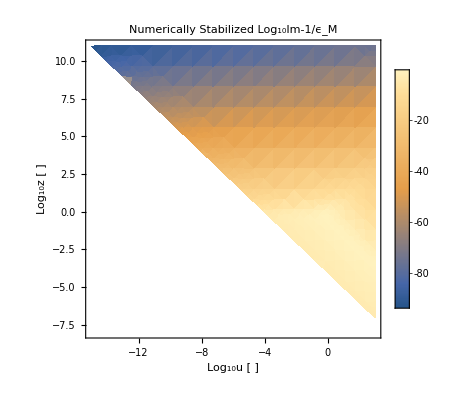

```mathematica
DensityPlot[Log10@(HeavisideTheta[10^u-(("ωedgei")/(2"qF""vF" 10^z)/.FeTotalparams[[2]])]Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]]),{u,-15,3},{z,-8,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

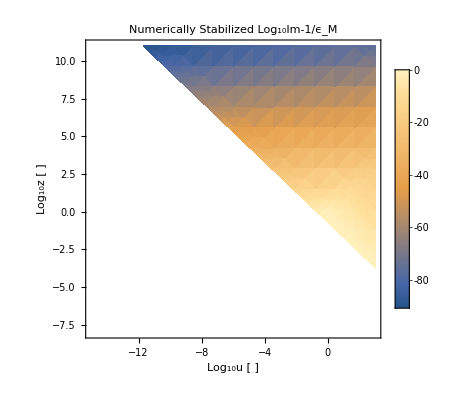

```mathematica
DensityPlot[Log10@(HeavisideTheta[10^u-(("ωedgei")/(2"qF""vF" 10^z)/.MgOTotalparams[[1]])]Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.MgOTotalparams[[1]]]/.MgOTotalparams[[1]]]),{u,-15,3},{z,-8,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"}]
```

### Electron Contribution to Evaporation Rate - momentum expansion

#### Analysis used in notes

Electronic evaporation is suppressed by the degeneracy of the fermi gas. But we want to find an estimate to show that it can be neglected. 

The contribution will only have support near the fermi momentum. We can then expand near the fermi momentum

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

How do we compute energy lost? Intuitively it is from a negative k. But does this make sense? Or is it negative k and negative ω? 

Is it sensible to compute the difference between the pure degenerate and slightly degenerate cases? The dielectric is odd in k and ω. So we should be able to integrate over the forbidden region, then using the fact that ϵ(-k,-ω) = ϵ(k,ω) we can compute as we did before and interpret as the rate for E_(p+k)<E_k (amounts to reinterpretting ω and using evenness in k)

Just use series in small ζ-1, and find the integration region that way.

```mathematica
FOccn = 1/(E^(β(Ek - μ))+1)
Series[FOccn,{Ek,μ,1}]
Assuming[Ek-μ>0,Series[FOccn,{β,∞,1}]]
```

1/(1+ⅇ^(β (Ek-μ)))

1/2-1/4 β (Ek-μ)+O[Ek-μ]^2

1/(1+ⅇ^((Ek-μ) β+O[1/β]^2))

```mathematica
FOccnDζ = 1/(1+ⅇ^(D (-1+ζ^2)))
```

1/(1+ⅇ^(D (-1+ζ^2)))

300

16

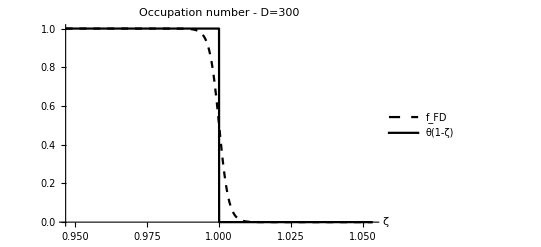

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","θ(1-ζ)"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],
Plot[(HeavisideTheta[1-ζ]),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotStyle->Black,PlotRange->All,AxesLabel->Automatic,Exclusions->None]}]
```

```mathematica
FOccnDζnearkF=Series[FOccnDζ,{ζ,1,1}]//Normal//FullSimplify
```

1/2 (1+D-D ζ)

```mathematica
FOccn /. μ-> EF + π^2/12 1/(D β)
%/.β->D/EF/.Ek->EF ζ^2//Simplify
Series[%,{ζ,1,1}]//Normal//FullSimplify
FOccnDζwμcor=Series[%,{D,∞,1}]//Normal //Simplify
"So we can neglect the change in the chemical potential here. "
```

1/(1+ⅇ^((-EF+Ek-π^2/(12 D β)) β))

1/(1+ⅇ^(-π^2/(12 D)+D (-1+ζ^2)))

(ⅇ^(π^2/(12 D)) (1+ⅇ^(π^2/(12 D))-2 D (-1+ζ)))/((1+ⅇ^(π^2/(12 D)))^2)

1/2+(π^2 (24+π^2 (-1+ζ)))/(1152 D)-1/2 D (-1+ζ)

So we can neglect the change in the chemical potential here.

```mathematica
ϵnd[u,z,uν]
```

1+1/(4 z^3)χ^2 (1/D-z) (ⅈ (ArcTan[(1+u-z)/uν]+ArcTan[(1-u+z)/uν])-ⅈ (ArcTan[(1-u-z)/uν]+ArcTan[(1+u+z)/uν])-1/2 Log[(uν^2+(1+u-z)^2)/(uν^2+(1-u+z)^2)]+1/2 Log[(uν^2+(1+u+z)^2)/(uν^2+(1-u-z)^2)])

```mathematica
ζm/."D"->100
```

99/100

```mathematica
Solve[FOccnDζnearkF==1,ζ]//Simplify
Solve[FOccnDζnearkF==0,ζ]//Simplify
```

{{ζ→(-1+D)/D}}

{{ζ→1+1/D}}

300

16

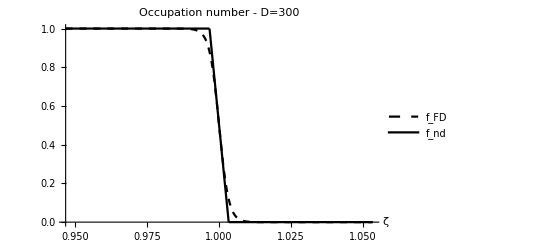

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1-rangerescale/Dtemp,1-1/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1+1/Dtemp,1+rangerescale/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Compute complex ω RPA dielectric in large D limit

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D);
# Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχRe1=Integrate[%,{ζ,0,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχIm1=Integrate[%,{ζ,0,1}]//FullSimplify
```

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

Log[1+(4 a)/((-1+a)^2+uν^2)]/D

(ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])/D

```mathematica
"Now compute the dielectric"
δϵRe1 = 1+χ^2/z^2 1/(4 z)(((δχRe1+I δχIm1)/.a->u+z)-((δχRe1+I δχIm1)/.a->u-z))//Simplify
```

Now compute the dielectric

1-1/(4 D z^3)ⅈ χ^2 (ArcTan[(-1+u-z)/uν]-ArcTan[(1+u-z)/uν]-ArcTan[(-1+u+z)/uν]+ArcTan[(1+u+z)/uν]-ⅈ Log[1+(4 (u-z))/(uν^2+(1-u+z)^2)]+ⅈ Log[1+(4 (u+z))/(uν^2+(-1+u+z)^2)])

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D);
#/2 Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,2}]//Normal//FullSimplify;
δχRe2=Integrate[%,{ζ,-1,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,2}]//Normal;
δχIm2=Integrate[%,{ζ,-1,1}]
```

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

(-(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)+(-1+3 D) Log[1+(4 a)/((-1+a)^2+uν^2)])/(6 D^2)

1/(6 D^2)((4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4)+(-2+6 D) ArcTan[(-1+a)/uν]+(2-6 D) ArcTan[(1+a)/uν])

```mathematica
"Now compute the dielectric"
δϵRe2 = 1+χ^2/z^2 1/(4 z)(((δχRe2+I δχIm2)/.a->u+z)-((δχRe2+I δχIm2)/.a->u-z))//FullSimplify
```

Now compute the dielectric

1+1/(24 D^2 z^3)χ^2 (2 (1/(-1+u+ⅈ uν-z)+1/(1+u+ⅈ uν-z)-1/(-1+u+ⅈ uν+z)-1/(1+u+ⅈ uν+z))+2 ⅈ (-1+3 D) ArcTan[(1+u-z)/uν]+2 ⅈ (-1+3 D) ArcTan[(1-u+z)/uν]+(-1+3 D) (2 ⅈ ArcTan[(-1+u+z)/uν]-2 ⅈ ArcTan[(1+u+z)/uν]-Log[1+(4 (u-z))/(uν^2+(1-u+z)^2)]+Log[1+(4 (u+z))/(uν^2+(-1+u+z)^2)]))

#### Decomposition of 2nd order corrections

```mathematica
(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4)//Apart
2 uν(1/(1+(a-uν)^2)+1/(1+(a+uν)^2))//Apart
 uν(1/(1+I(a-uν))+1/(1-I(a-uν))+1/(1+I(a+uν))+1/(1-I(a+uν)))//Simplify//Apart
```

(2 uν)/(1-2 a+a^2+uν^2)+(2 uν)/(1+2 a+a^2+uν^2)

(2 uν)/(1+a^2-2 a uν+uν^2)+(2 uν)/(1+a^2+2 a uν+uν^2)

(2 uν)/(1+a^2-2 a uν+uν^2)+(2 uν)/(1+a^2+2 a uν+uν^2)

```mathematica
(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)//Apart
2((a-1)/(1+(a-uν)^2)+(1+a)/(1+(a+uν)^2))//Apart
```

(2 (-1+a))/(1-2 a+a^2+uν^2)+(2 (1+a))/(1+2 a+a^2+uν^2)

(2 (-1+a))/(1+a^2-2 a uν+uν^2)+(2 (1+a))/(1+a^2+2 a uν+uν^2)

```mathematica
(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)/.uν->0//Apart
```

2/(-1+a)+2/(1+a)

#### Limits of 2nd order corrections in large and small a

Check that the expansion works for large and small a

```mathematica
Series[ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν],{a,0,2}]
Series[ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν],{a,∞,2}]
Series[(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4),{a,0,2}]
Series[(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4),{a,∞,2}]
"Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant."
```

-2 ArcTan[1/uν]+(2 uν a^2)/((1+uν^2)^2)+O[a]^3

-(2 uν)/a^2+O[1/a]^3

(4 uν)/(1+uν^2)-(4 (uν (-3+uν^2)) a^2)/((1+uν^2)^3)+O[a]^3

(4 uν)/a^2+O[1/a]^3

Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant.

```mathematica
Series[Log[1+(4 a)/((-1+a)^2+uν^2)],{a,0,2}]
Series[Log[1+(4 a)/((-1+a)^2+uν^2)],{a,∞,2}]
Series[(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2),{a,0,2}]
Series[(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2),{a,∞,2}]
"Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant."
```

(4 a)/(1+uν^2)+O[a]^3

4/a+O[1/a]^3

(4 (-1+uν^2) a)/((1+uν^2)^2)+O[a]^3

4/a+O[1/a]^3

Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant.

#### Real RPA limits of above

```mathematica
"The 1st order corrections are straightforward using expressions in the notes."
(Log[(1+a)/(1-a)]/.a->z)-(Log[(1+a)/(1-a)]/.a->-z)
%==2Log[(1+z)/(1-z)]//Simplify//PowerExpand
```

The 1st order corrections are straightforward using expressions in the notes.

-Log[(1-z)/(1+z)]+Log[(1+z)/(1-z)]

True

#### Scattering Phase space

The maximum momentum transfer in ζ we can have in an interaction is

```mathematica
Δζmax = (1+1/D)-(1-1/D)
```

2/D

We have defined fermi function to only have support over this range, since we have defined p = ζ k_F we have that the maximum momentum that can be transfered to the probe from the system for each oscillator is in eV

```mathematica
2/("D")"qF"("ℏ""c")/("JpereV")/.FeTotalparams
2/("D")"qF"("ℏ""c")/("JpereV")/.SiO2Totalparams
2/("D")"qF"("ℏ""c")/("JpereV")/.MgOTotalparams
```

{17.8171,14.5263,11.0565,5.69488,1.12259,0.244832}

{11.2987,6.63264}

{15.7459,11.7913,11.0313,7.13196}

So there is some possibility to evaporate light mass aDM with these kinematics. However, all rates will be suppressed by

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

```mathematica
1/("D")/.FeTotalparams
1/("D")/.SiO2Totalparams
1/("D")/.MgOTotalparams
```

{0.00310139,0.00206155,0.00119432,0.000316849,0.0000123119,5.85624×10^-7}

{0.00124721,0.000429789}

{0.00242225,0.00135833,0.00118887,0.000496936}

```mathematica
"Need to recompute the dielectric imposing this kinematic restriction"
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D);
# Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχRe1=Integrate[%,{ζ,0,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχIm1=Integrate[%,{ζ,0,1}]//FullSimplify
```

Need to recompute the dielectric imposing this kinematic restriction

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

Log[1+(4 a)/((-1+a)^2+uν^2)]/D

(ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])/D

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1+1/D}],{D,∞,2}]//Normal
```

∫_0^(1+1/D) 1/2 (1+D-D ζ) f[ζ]ⅆζ

```mathematica
Limit[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D->∞]
"Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand"
f[1]Integrate[D (1-ζ) ,{ζ,1-1/D,1+1/D}]
(*(%/.ζ->1-1/D)//Simplify
(%%/.ζ->1+1/D)//Simplify*)
"Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is"
HoldForm[1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D]]
1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D]//Simplify
```

lim_(D→∞) ∫_(1-1/D)^(1+1/D) 1/2 (1+D-D ζ) f[ζ]ⅆζ

Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand

0

Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is

(∂_D ∫_(1-1/D)^(1+1/D) FOccnDζnearkF f[ζ]ⅆζ)/D

(-f[(-1+D)/D]+D^2 ∫_((-1+D)/D)^(1+1/D) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^3

```mathematica
Limit[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D-2z}],D->∞]
"Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand"
f[1]Integrate[D (1-ζ) ,{ζ,1-1/D,1+1/D-2z}]
(*(%/.ζ->1-1/D)//Simplify
(%%/.ζ->1+1/D)//Simplify*)
"Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is"
HoldForm[1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D-2z}],D]]
"We can now seperate the integrals"
1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1+1/D-2z}],D]//Simplify
-1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1-1/D}],D]//Simplify
"Then perform shifts on the variable so that"
1/D D[Integrate[FOccnDζnearkF f[ζ]/.ζ->ζ-(1/D-2z),{ζ,-1/D+2z,1}],D]//Simplify
-1/D D[Integrate[FOccnDζnearkF f[ζ]/.ζ->ζ+1/D,{ζ,-1/D,1}],D]//Simplify
```

lim_(D→∞) ∫_(1-1/D)^(1+1/D-2 z) 1/2 (1+D-D ζ) f[ζ]ⅆζ

Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand

(2 z-2 D z^2) f[1]

Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is

(∂_D ∫_(1-1/D)^(1+1/D-2 z) FOccnDζnearkF f[ζ]ⅆζ)/D

We can now seperate the integrals

(-z f[1+1/D-2 z]+D ∫_0^(1+1/D-2 z) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^2

-(f[(-1+D)/D]+D^2 ∫_0^((-1+D)/D) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^3

Then perform shifts on the variable so that

((-3+D (-1+4 z)) f[-2/D+4 z])/(2 D^3)+1/D(∫_(-1/D+2 z)^1 1/2 (-((-1+2 z+ζ) f[-1/D+2 z+ζ])+((2-D (-1+2 z+ζ)) f'[-1/D+2 z+ζ])/D^2)ⅆζ)

(f[0]+D f[0]-2 D^2 ∫_(-1/D)^1 -((-1+ζ) (D f[1/D+ζ]-f'[1/D+ζ]))/(2 D)ⅆζ)/(2 D^3)

#### Investigate changing slope to conservatively overestimate phase space available

Consider conservatively rescaling the slope of the line to ensure that the phase space that the line doesn’t capture is fermi suppressed.

```mathematica
1/(1+ⅇ^(D (-1+ζ^2)))/.ζ->1+b/D//Simplify
%/.b->5/.D->10000000//Simplify//N
(*1/(1+E^(2 b))*)E^(-2 b)/.b->5//N
1/(1+ⅇ^(D (-1+ζ^2)))/.ζ->1-b/D//Simplify
1-%/.b->5/.D->10000000//Simplify//N
"So we see that in the limit of large D a rescaling of D -> D/b gives a fermi suppression at the boundaries of about E^(-2 b)"
"So our fermi suppression is about 10^-b"
(Log10@(E^(-2 b)))//Simplify//PowerExpand
N@(Log[10])
```

1/(1+ⅇ^((b (b+2 D))/D))

0.0000453978

0.0000453999

1/(1+ⅇ^((b (b-2 D))/D))

0.000045398

So we see that in the limit of large D a rescaling of D -> D/b gives a fermi suppression at the boundaries of about E^(-2 b)

So our fermi suppression is about 10^-b

-(2 b)/(Log[2]+Log[5])

2.30259

```mathematica
E^-16//N
```

1.12535×10^-7

300

8

2

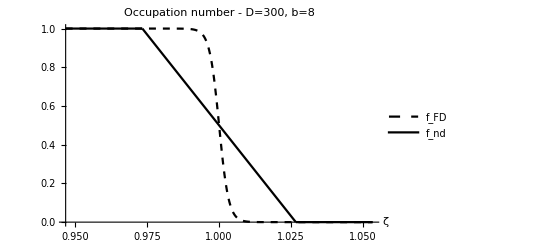

```mathematica
Clear[rangerescale]
Dtemp = 300
sloperescale=8
rangerescale = 2

Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-(rangerescale sloperescale)/Dtemp,1 + (rangerescale sloperescale)/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300, b=8",AxesLabel->Automatic],Plot[(FOccnDζnearkF/.D->D/sloperescale/.D->Dtemp),{ζ,1-sloperescale/Dtemp,1 + sloperescale/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1-(rangerescale sloperescale)/Dtemp,1-sloperescale/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1+sloperescale/Dtemp,1+(rangerescale sloperescale)/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Expand in small and large exponentials

1-x+O[x]^2

1/x+O[1/x]^2

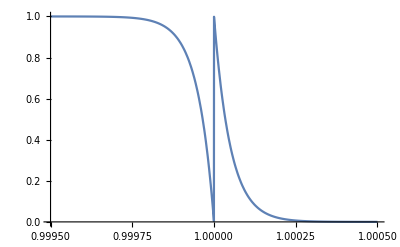

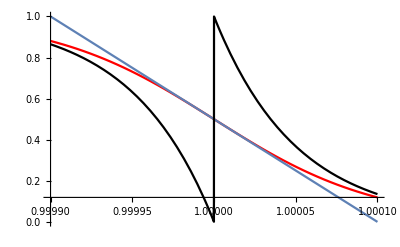

```mathematica
Series[1/(1+x),{x,0,1}]
Series[1/(1+x),{x,∞,1}]
Dtemp = 10000;
Plot[HeavisideTheta[1-ζ](1- x)+HeavisideTheta[ζ-1](x^-1)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-5/Dtemp,1 + 5/Dtemp}]
Show@{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Red],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All],Plot[HeavisideTheta[1-ζ](1- x)+HeavisideTheta[ζ-1](x^-1)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotStyle->Black]}
```

1-x+x^2+O[x]^3

1/x-(1/x)^2+O[1/x]^3

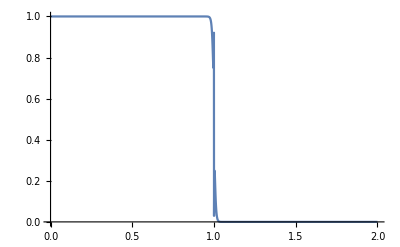

10000

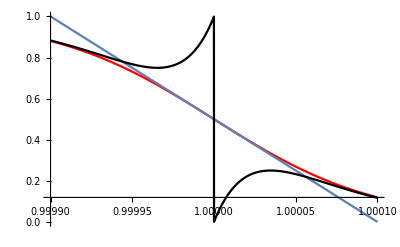

```mathematica
Series[1/(1+x),{x,0,2}]
Series[1/(1+x),{x,∞,2}]
Plot[HeavisideTheta[1-ζ](1- x+x^2)+HeavisideTheta[ζ-1](x^-1-x^-2)/.x->ⅇ^(D (-1+ζ^2))/.D->100,{ζ,0,2}]
Dtemp = 10000
Show@{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Red],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All],Plot[HeavisideTheta[1-ζ](1- x+x^2)+HeavisideTheta[ζ-1](x^-1-x^-2)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotStyle->Black]}
```

So our linear approximation is a better fit than expanding in large and small exponentials near the fermi sphere. 

It does givea much better approximation far from the fermi sphere. The question is whether we think the most important contribution to the evaporation rate will be far or close to the fermi sphere. I suppose we can check this by computing the contribution from this expansion. 

The other intriguing part of using this expansion, is that each subsequent term amounts to a change of the value of the degeneracy by an integer, so in principle they could be resummed. So we only need to compute:

```mathematica
Series[1/(1+x),{x,0,2}](*valid between 0 and 1*)
Series[1/(1+x),{x,∞,2}](*valid between 1 and ∞*)
```

1-x+x^2+O[x]^3

1/x-(1/x)^2+O[1/x]^3

```mathematica
Integrate[1/2 ζ E^(D(ζ^2-1))Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1}]
```

$Aborted

Try integrating by parts for imaginary part

```mathematica
1/2 ζ E^(D(ζ^2-1))Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)](*this is boundary term at 0 and ∞*)
Integrate[1/2 ζ E^(D(ζ^2-1)),ζ]
D[Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],ζ]//FullSimplify(*this is boundary term at 0 and ∞*)
Apart[%,ζ]
Integrate[%% %%%,ζ]
```

1/2 ⅇ^(D (-1+ζ^2)) ζ Log[(uν^2+(a+ζ)^2)/(uν^2+(a-ζ)^2)]

(ⅇ^(-D+D ζ^2))/(4 D)

(4 a (a^2+uν^2-ζ^2))/(a^4+2 a^2 (uν-ζ) (uν+ζ)+(uν^2+ζ^2)^2)

(2 (a-ζ))/(a^2+uν^2-2 a ζ+ζ^2)+(2 (a+ζ))/(a^2+uν^2+2 a ζ+ζ^2)

(a ∫(ⅇ^(-D+D ζ^2) (a^2+uν^2-ζ^2))/(a^4+2 a^2 (uν-ζ) (uν+ζ)+(uν^2+ζ^2)^2)ⅆζ)/D

Try integrating by parts for the real part

```mathematica
- ζ  E^(D(ζ^2-1))(ArcTan[(a+ζ)/uν]-ArcTan[(a-ζ)/uν])
 Integrate[ζ E^(D(ζ^2-1)),ζ]
D[(ArcTan[(a+ζ)/uν]-ArcTan[(a-ζ)/uν]),ζ]
Apart[%,ζ]
Integrate[%% %%%,ζ]
```

-ⅇ^(D (-1+ζ^2)) ζ (-ArcTan[(a-ζ)/uν]+ArcTan[(a+ζ)/uν])

(ⅇ^(-D+D ζ^2))/(2 D)

1/(uν (1+(a-ζ)^2/uν^2))+1/(uν (1+(a+ζ)^2/uν^2))

uν/(a^2+uν^2-2 a ζ+ζ^2)+uν/(a^2+uν^2+2 a ζ+ζ^2)

(∫ⅇ^(-D+D ζ^2) (1/(uν (1+(a-ζ)^2/uν^2))+1/(uν (1+(a+ζ)^2/uν^2)))ⅆζ)/(2 D)

We can differentiate under the integral sign to solve both these integrals.

```mathematica
Integrate[E^(D (ζ^2-1)),{ζ,0,1}]
```

(ⅇ^-D √π Erfi[√D])/(2 √D)

```mathematica
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν(ⅇ^-D √π Erfi[√D])/(2 √D),f[D],D]//Simplify
```

{{f[D]→-(ⅈ ⅇ^(-a D+ⅈ D uν) π)/(4 √(-1+a-ⅈ uν))+(ⅈ ⅇ^(-D (a+ⅈ uν)) π)/(4 √(-1+a+ⅈ uν))+ⅇ^(-D (a+ⅈ uν)) C[1]+ⅇ^(-a D+ⅈ D uν) C[2]-(ⅈ ⅇ^(-a D+ⅈ D uν) π OwenT[ⅈ √2 √D √(-1+a-ⅈ uν),1/(√(-1+a-ⅈ uν))])/(√(-1+a-ⅈ uν))+(ⅈ ⅇ^(-D (a+ⅈ uν)) π OwenT[ⅈ √2 √D √(-1+a+ⅈ uν),1/(√(-1+a+ⅈ uν))])/(√(-1+a+ⅈ uν))}}

```mathematica
Integrate[E^(-D (ζ^2-1)),{ζ,1,∞}]
```

ConditionalExpression[(ⅇ^D √π Erfc[√D])/(2 √D), Re[D]>0]

```mathematica
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν(ⅇ^-D √π Erfc[√D])/(2 √D),f[D],D]//FullSimplify
```

{{f[D]→1/4 ⅇ^(-D (a+ⅈ uν)) (-ⅈ π ((ⅇ^(2 ⅈ D uν) √(-1+a-ⅈ uν))/(√((ⅈ (-1+a)+uν)^2))+(√((ⅈ-ⅈ a+uν)^2))/(-1+a+ⅈ uν)^(3/2))+4 (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ π ((ⅇ^(2 ⅈ D uν) √(1-a+ⅈ uν) Erfi[√D √(-1+a-ⅈ uν)])/(√((ⅈ (-1+a)+uν)^2))+(√((ⅈ-ⅈ a+uν)^2) Erfi[√D √(-1+a+ⅈ uν)])/(1-a-ⅈ uν)^(3/2))-4 ⅈ π ((√(-(-1+a+ⅈ uν)^2) OwenT[√2 √D √(1-a-ⅈ uν),1/(√(1-a-ⅈ uν))])/(-1+a+ⅈ uν)^(3/2)+(ⅇ^(2 ⅈ D uν) √(-1+a-ⅈ uν) OwenT[√2 √D √(1-a+ⅈ uν),1/(√(1-a+ⅈ uν))])/(√((ⅈ (-1+a)+uν)^2))))}}

No way that we can sum this over D times an integer. But we can use this to get the non-degenerate limit

```mathematica
Integrate[E^(D (ζ^2-1)),{ζ,0,∞}]//Normal
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν%,f[D],D]//FullSimplify
```

(ⅇ^-D √π)/(2 √-D)

{{f[D]→1/(4 √-D)ⅇ^(-D (a+ⅈ uν)) (4 √-D (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ D √π (ExpIntegralE[1/2,-D (-1+a+ⅈ uν)]-ⅇ^(2 ⅈ D uν) ExpIntegralE[1/2,D-a D+ⅈ D uν]))}}

```mathematica
1/(4 √-D)ⅇ^(-D (a+ⅈ uν)) (4 √-D (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ D √π (ExpIntegralE[1/2,-D (-1+a+ⅈ uν)]-ⅇ^(2 ⅈ D uν) ExpIntegralE[1/2,D-a D+ⅈ D uν]))/.C[1]->0/.C[2]->0/.{a->2,uν->3,D->-100}//N
```

7.13967×10^41+7.25355×10^24 ⅈ

```mathematica
Integrate[E^(D (ζ^2))ζ,{ζ,0,∞}]
```

ConditionalExpression[-1/(2 D), Re[D]<0]

```mathematica
(ζ^2 E^(D (ζ^2-1)))/(u+z+ζ y + I uν)
Integrate[ζ^2 E^(-D (ζ^2-1)),{ζ,0,∞}]
```

(ⅇ^(D (-1+ζ^2)) ζ^2)/(u+ⅈ uν+z+y ζ)

ConditionalExpression[(ⅇ^D √π)/(4 D^(3/2)), Re[D]>0]

```mathematica
DSolve[(u+ⅈ uν+z) f[D]-y  f'[D]==(ⅇ^D √π)/(4 D^(3/2)),f[D],D]//FullSimplify
```

{{f[D]→1/2 ((ⅇ^D √π)/(√D y)+2 ⅇ^((D (u+ⅈ uν+z))/y) C[1]+(ⅇ^((D (u+ⅈ uν+z))/y) π √(u+ⅈ uν-y+z) Erf[(√D √(u+ⅈ uν-y+z))/(√y)])/y^(3/2))}}

```mathematica
Integrate[1/2 ((ⅇ^D √π)/(√D y)+2 ⅇ^((D (u+ⅈ uν+z))/y) C[1]+(ⅇ^((D (u+ⅈ uν+z))/y) π √(u+ⅈ uν-y+z) Erf[(√D √(u+ⅈ uν-y+z))/(√y)])/y^(3/2)),{y,-1,1}]
```

$Aborted

#### Use the form in notes for large and small exponentials

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + i uν),{ζ,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(-D (a+i uν)^2) (CoshIntegral[D (a+i uν)^2]+π Erfi[√D (a+i uν)]+Log[D]-2 Log[-1/(a+i uν)]-Log[D (a+i uν)^2]+SinhIntegral[D (a+i uν)^2]), ]

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + I uν),{ζ,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π Erfi[√D (a+ⅈ uν)]+Log[D]-2 Log[-1/(a+ⅈ uν)]-Log[D (a+ⅈ uν)^2]+SinhIntegral[D (a+ⅈ uν)^2]), (Im[a]+Re[uν]≠0||Im[uν]>Re[a])&&Re[D]>0]

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + I uν),{ζ,0,∞}];
%//FullSimplify//PowerExpand//Simplify//Normal
%/.uν->0//FullSimplify
```

1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π (-2 ⅈ+Erfi[√D (a+ⅈ uν)])+SinhIntegral[D (a+ⅈ uν)^2])

1/2 ⅇ^(-a^2 D) (CoshIntegral[a^2 D]+π (-2 ⅈ+Erfi[a √D])+SinhIntegral[a^2 D])

```mathematica
Integrate[(E^(- D ζ^2))/(a + ζ + I uν),{ζ,0,∞}];
%//FullSimplify//PowerExpand//Simplify//Normal
%/.uν->0//FullSimplify
```

-1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]-π Erfi[√D (a+ⅈ uν)]+SinhIntegral[D (a+ⅈ uν)^2])

-1/2 ⅇ^(-a^2 D) (CoshIntegral[a^2 D]-π Erfi[a √D]+SinhIntegral[a^2 D])

```mathematica
-1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]-π Erfi[√D (a+ⅈ uν)]+SinhIntegral[D (a+ⅈ uν)^2])-(1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π (-2 ⅈ+Erfi[√D (a+ⅈ uν)])+SinhIntegral[D (a+ⅈ uν)^2]))//Simplify
```

ⅇ^(-D (a+ⅈ uν)^2) (ⅈ π-CoshIntegral[D (a+ⅈ uν)^2]-SinhIntegral[D (a+ⅈ uν)^2])

```mathematica
FullSimplify[ExpIntegralEi[z]+1/2(Log[z]+Log[1/z])](*from the ExpIntegralEi properties and relations page on mathematica*)
1/2(Log[z]+Log[1/z])//PowerExpand
```

CoshIntegral[z]+SinhIntegral[z]

0

```mathematica
"So the integral is proportional to"
E^(-D(a+I uν)^2)ExpIntegralEi[D(a+I uν)^2]
"The factor of i π is due to the branch cut discontinuity"
```

So the integral is proportional to

ⅇ^(-D (a+ⅈ uν)^2) ExpIntegralEi[D (a+ⅈ uν)^2]

The factor of i π is due to the branch cut discontinuity

2.71828^(-100. ((0.+0.1 ⅈ)+a)^2) ExpIntegralEi[100. ((0.+0.1 ⅈ)+a)^2]

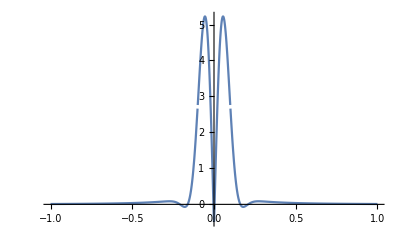

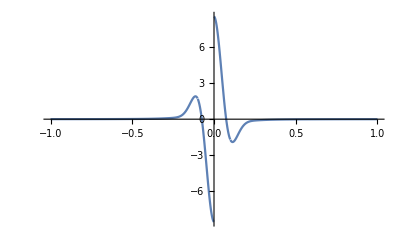

```mathematica
E^(-D(a+I uν)^2)ExpIntegralEi[D(a+I uν)^2]/.D->100/.uν->0.1//N
Plot[Re[%],{a,-1,1},PlotRange->All]
Plot[Im[%%],{a,-1,1},PlotRange->All]
```

```mathematica
"Can we derive this result analytically?"
(E^(- D ζ^2))/(a + uν I + ζ)/.ζ->ζ - (a + uν I )
-(E^(- D ζ^2))/(a + uν I - ζ)/.ζ->ζ + (a + uν I )
HoldForm[Integrate[(ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ,{ζ,a + uν I,∞}]]
```

Can we derive this result analytically?

(ⅇ^(-D (-a-ⅈ uν+ζ)^2))/ζ

(ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ

∫_(a+uν ⅈ)^∞ (ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ ⅆζ

```mathematica
Assuming[z∈Complexes,Integrate[(ⅇ^(-D (ζ)^2))/ζ,{ζ,z,∞}]]
```

ConditionalExpression[1/2 Gamma[0,D z^2], Re[z]>0&&Im[z]==0&&Re[D]>0]

#### More kinematics

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

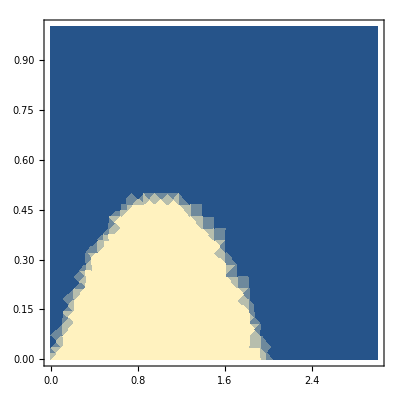

{{q→-(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ}}

HeavisideTheta[q+(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ] HeavisideTheta[q-(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

```mathematica
HeavisideTheta[ωm-ω]HeavisideTheta[ωp+ω]/.ωm->q v - (ℏ q^2)/(2 mχ) /.ωp->q v + (ℏ q^2)/(2 mχ) 
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,0,1}]
Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q]
HeavisideTheta[q-(q/.%[[1]])]HeavisideTheta[q-(q/.%[[2]])]
```

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

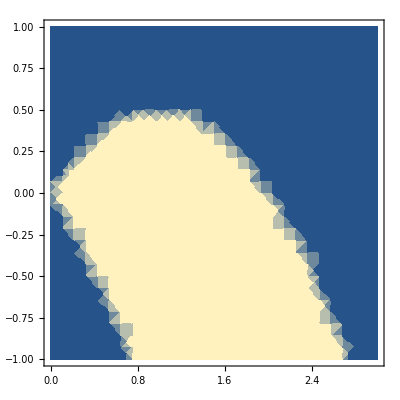

```mathematica
HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)]HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)](*HeavisideTheta[1/2 mχ v^2 +ω ℏ]*)
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,1}]
```

(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

HeavisideTheta[q-(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ] HeavisideTheta[-q+(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

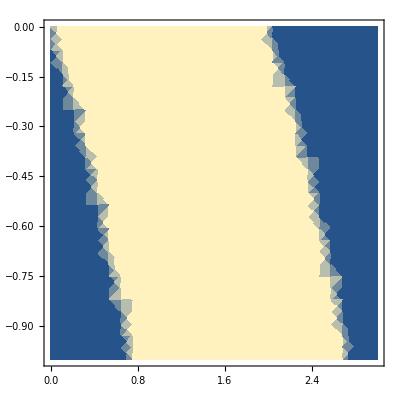

```mathematica
qp=q/.Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
mqm = q /.Solve[q v+ω+(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
HeavisideTheta[qp-q]HeavisideTheta[q-mqm]
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,0}]
```

```mathematica
mqm/.ω->-Abs[ω]
D[%,ω]
```

(-mχ v+√mχ √(mχ v^2+2 ℏ Abs[ω]))/ℏ

(√mχ Abs'[ω])/(√(mχ v^2+2 ℏ Abs[ω]))

```mathematica
Clear[Absωsol]
Solve[(mqm/(2 kF)/.ω->-Abs[ω])==1/D,Abs[ω]]
Absωsol=(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)
(*Solve[(mqm/(2 kF))==1/D,ω]*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Abs[ω]→(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)}}

(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)

```mathematica
Solve[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)==mχ/(2 ℏ)(vesc^2-v^2),v]//Simplify
```

{{v→-vesc-(2 kF ℏ)/(D mχ)},{v→vesc-(2 kF ℏ)/(D mχ)}}

```mathematica
D[-mχ/(2 ℏ)(vesc^2-v^2)+(2 (D kF mχ v-kF^2 ℏ))/(D^2 mχ),v]
Solve[%==0,v]
```

(2 kF)/D+(mχ v)/ℏ

{{v→-(2 kF ℏ)/(D mχ)}}

{ℏ→1,D→300,mχ→1,kF→10,vesc→1}

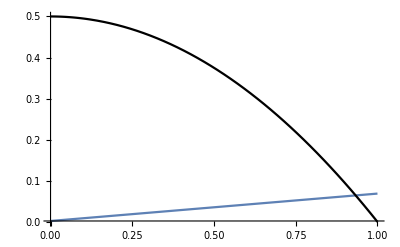

1/15

1

```mathematica
{ℏ->1,D->300,mχ->1,kF->10,vesc->1}
Show[{Plot[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)/.%,{v,0,1},PlotRange->All],
Plot[mχ/(2 ℏ)(vesc^2-v^2)/.%,{v,0,1},PlotStyle->Black]}]
(2kF ℏ)/(D mχ)/.%%
vesc /.%%%
```

```mathematica
"D"/.FeTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

```mathematica
("ℏ""qF""c")/("JpereV""D")/.SIConstRepl/.FeTotalparams
```

{8.90855,7.26316,5.52827,2.84744,0.561296,0.122416}

```mathematica
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[MgOTotalparams]}]},{m,6,15}]
"The lowest rescaling we can do where evaporation is still 0 is b=4"
Drescale = "D"->("D")/b/.b->4
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"The first rescaling where it is non-zero is b=5"
Drescale = "D"->("D")/b/.b->5
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
"This tells us that the energy threshold is less than ωedgei for most of the oscillators we consider. The conduction band of iron is the lowest, and only begins to contribute to the rate between b of 4-5 so about an additional suppression of 10^-4, and only for electron mass aDM "
Drescale = "D"->("D")/b/.b->8
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"So we need this much suppression to get contributions from higher masses"
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | 6.68936×10^6
76230.9
5.40093×10^6
5.25583×10^6
1.91904×10^11
8.86771×10^12
7 | 6.69176×10^6
78191.9
5.40243×10^6
5.2566×10^6
1.91904×10^11
8.86771×10^12
8 | 6.69201×10^6
78388.
5.40258×10^6
5.25668×10^6
1.91904×10^11
8.86771×10^12
9 | 6.69203×10^6
78407.6
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
10 | 6.69203×10^6
78409.6
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
11 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
12 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
13 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
14 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12
15 | 6.69203×10^6
78409.8
5.40259×10^6
5.25669×10^6
1.91904×10^11
8.86771×10^12

{{6,{2.36298×10^8,4.02543×10^8}},{7,{2.36299×10^8,4.02543×10^8}},{8,{2.36299×10^8,4.02544×10^8}},{9,{2.36299×10^8,4.02544×10^8}},{10,{2.36299×10^8,4.02544×10^8}},{11,{2.36299×10^8,4.02544×10^8}},{12,{2.36299×10^8,4.02544×10^8}},{13,{2.36299×10^8,4.02544×10^8}},{14,{2.36299×10^8,4.02544×10^8}},{15,{2.36299×10^8,4.02544×10^8}}}

{{6,{1.48025×10^8,1.97675×10^8,2.11295×10^8,3.26826×10^8}},{7,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{8,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{9,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{10,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{11,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{12,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{13,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{14,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}},{15,{1.48027×10^8,1.97677×10^8,2.11297×10^8,3.26827×10^8}}}

The lowest rescaling we can do where evaporation is still 0 is b=4

D→D/4

{{6,{1.65392×10^6,2486.66,1.33561×10^6,1.30235×10^6,4.7976×10^10,2.21693×10^12}},{7,{1.66354×10^6,10330.9,1.34158×10^6,1.30543×10^6,4.7976×10^10,2.21693×10^12}},{8,{1.6645×10^6,11115.3,1.34218×10^6,1.30574×10^6,4.7976×10^10,2.21693×10^12}},{9,{1.6646×10^6,11193.7,1.34224×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{10,{1.66461×10^6,11201.6,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{11,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{12,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{13,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{14,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}},{15,{1.66461×10^6,11202.4,1.34225×10^6,1.30577×10^6,4.7976×10^10,2.21693×10^12}}}

The first rescaling where it is non-zero is b=5

D→D/5

6 | 1.31608×10^6
-4172.78
1.06327×10^6
1.03811×10^6
3.83808×10^10
1.77354×10^12
7 | 1.32811×10^6
5632.49
1.07073×10^6
1.04195×10^6
3.83808×10^10
1.77354×10^12
8 | 1.32931×10^6
6613.01
1.07148×10^6
1.04233×10^6
3.83808×10^10
1.77354×10^12
9 | 1.32943×10^6
6711.06
1.07155×10^6
1.04237×10^6
3.83808×10^10
1.77354×10^12
10 | 1.32945×10^6
6720.87
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
11 | 1.32945×10^6
6721.85
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
12 | 1.32945×10^6
6721.95
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
13 | 1.32945×10^6
6721.96
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
14 | 1.32945×10^6
6721.96
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12
15 | 1.32945×10^6
6721.96
1.07156×10^6
1.04238×10^6
3.83808×10^10
1.77354×10^12

This tells us that the energy threshold is less than ωedgei for most of the oscillators we consider. The conduction band of iron is the lowest, and only begins to contribute to the rate between b of 4-5 so about an additional suppression of 10^-4, and only for electron mass aDM

D→D/8

{{6,{805323.,-17430.4,652256.,640452.,2.3988×10^10,1.10846×10^12}},{7,{824566.,-1741.93,664197.,646602.,2.3988×10^10,1.10846×10^12}},{8,{826490.,-173.091,665392.,647217.,2.3988×10^10,1.10846×10^12}},{9,{826683.,-16.2068,665511.,647279.,2.3988×10^10,1.10846×10^12}},{10,{826702.,-0.518387,665523.,647285.,2.3988×10^10,1.10846×10^12}},{11,{826704.,1.05045,665524.,647286.,2.3988×10^10,1.10846×10^12}},{12,{826704.,1.20734,665524.,647286.,2.3988×10^10,1.10846×10^12}},{13,{826704.,1.22303,665524.,647286.,2.3988×10^10,1.10846×10^12}},{14,{826704.,1.2246,665524.,647286.,2.3988×10^10,1.10846×10^12}},{15,{826704.,1.22475,665524.,647286.,2.3988×10^10,1.10846×10^12}}}

So we need this much suppression to get contributions from higher masses

```mathematica
"same as above, but for the raw kinematic constraint"
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]//TableForm
```

same as above, but for the raw kinematic constraint

D→D

6 | -5345.13
-4357.89
-3316.96
-1708.47
-336.778
-73.4496
7 | -534.513
-435.789
-331.696
-170.847
-33.6778
-7.34496
8 | -53.4513
-43.5789
-33.1696
-17.0847
-3.36778
-0.734496
9 | -5.34513
-4.35789
-3.31696
-1.70847
-0.336778
-0.0734496
10 | -0.534513
-0.435789
-0.331696
-0.170847
-0.0336778
-0.00734496
11 | -0.0534513
-0.0435789
-0.0331696
-0.0170847
-0.00336778
-0.000734496
12 | -0.00534513
-0.00435789
-0.00331696
-0.00170847
-0.000336778
-0.0000734496
13 | -0.000534513
-0.000435789
-0.000331696
-0.000170847
-0.0000336778
-7.34496×10^-6
14 | -0.0000534513
-0.0000435789
-0.0000331696
-0.0000170847
-3.36778×10^-6
-7.34496×10^-7
15 | -5.34513×10^-6
-4.35789×10^-6
-3.31696×10^-6
-1.70847×10^-6
-3.36778×10^-7
-7.34496×10^-8

6 | -3389.61
-1989.79
7 | -338.961
-198.979
8 | -33.8961
-19.8979
9 | -3.38961
-1.98979
10 | -0.338961
-0.198979
11 | -0.0338961
-0.0198979
12 | -0.00338961
-0.00198979
13 | -0.000338961
-0.000198979
14 | -0.0000338961
-0.0000198979
15 | -3.38961×10^-6
-1.98979×10^-6

6 | -4723.78
-3537.39
-3309.38
-2139.59
7 | -472.378
-353.739
-330.938
-213.959
8 | -47.2378
-35.3739
-33.0938
-21.3959
9 | -4.72378
-3.53739
-3.30938
-2.13959
10 | -0.472378
-0.353739
-0.330938
-0.213959
11 | -0.0472378
-0.0353739
-0.0330938
-0.0213959
12 | -0.00472378
-0.00353739
-0.00330938
-0.00213959
13 | -0.000472378
-0.000353739
-0.000330938
-0.000213959
14 | -0.0000472378
-0.0000353739
-0.0000330938
-0.0000213959
15 | -4.72378×10^-6
-3.53739×10^-6
-3.30938×10^-6
-2.13959×10^-6

```mathematica
"What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?"
mχ/2(("vesc")^2-vχ^2)=="EF"
Solve[%,vχ][[2]]
Table[{m,%/.FeTotalparams/.Constants`EarthRepl/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl//Simplify},{m,6,15}]
"imaginary part implies EF is more than enough to evaporate at any velocity"
```

What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?

1/2 mχ (vesc^2-vχ^2)==EF

{vχ→(√(-2 EF+vesc^2 mχ))/(√mχ)}

{{6,{{vχ→0.+1.20449×10^6 ⅈ},{vχ→0.+1.47738×10^6 ⅈ},{vχ→0.+1.94103×10^6 ⅈ},{vχ→0.+3.76854×10^6 ⅈ},{vχ→0.+1.91178×10^7 ⅈ},{vχ→0.+8.76579×10^7 ⅈ}}},{7,{{vχ→0.+380745. ⅈ},{vχ→0.+467067. ⅈ},{vχ→0.+613716. ⅈ},{vχ→0.+1.19167×10^6 ⅈ},{vχ→0.+6.04557×10^6 ⅈ},{vχ→0.+2.77199×10^7 ⅈ}}},{8,{{vχ→0.+119933. ⅈ},{vχ→0.+147317. ⅈ},{vχ→0.+193783. ⅈ},{vχ→0.+376689. ⅈ},{vχ→0.+1.91175×10^6 ⅈ},{vχ→0.+8.76579×10^6 ⅈ}}},{9,{{vχ→0.+36407.2 ⅈ},{vχ→0.+45357.8 ⅈ},{vχ→0.+60351.4 ⅈ},{vχ→0.+118645. ⅈ},{vχ→0.+604454. ⅈ},{vχ→0.+2.77196×10^6 ⅈ}}},{10,{{vχ→0.+4433.12 ⅈ},{vχ→0.+9635.21 ⅈ},{vχ→0.+15853.5 ⅈ},{vχ→0.+35982.8 ⅈ},{vχ→0.+190850. ⅈ},{vχ→0.+876508. ⅈ}}},{11,{{vχ→10532.4},{vχ→10179.},{vχ→9368.17},{vχ→0.+4071.86 ⅈ},{vχ→0.+59409.3 ⅈ},{vχ→0.+276972. ⅈ}}},{12,{{vχ→11135.},{vχ→11102.1},{vχ→11030.5},{vχ→10546.9},{vχ→0.+15493.5 ⅈ},{vχ→0.+86939.5 ⅈ}}},{13,{{vχ→11193.5},{vχ→11190.3},{vχ→11183.2},{vχ→11136.4},{vχ→9428.2},{vχ→0.+25356.5 ⅈ}}},{14,{{vχ→11199.4},{vχ→11199.},{vχ→11198.3},{vχ→11193.7},{vχ→11035.6},{vχ→6971.43}}},{15,{{vχ→11199.9},{vχ→11199.9},{vχ→11199.8},{vχ→11199.4},{vχ→11183.7},{vχ→10851.5}}}}

imaginary part implies EF is more than enough to evaporate at any velocity

### Mermin Limit to lindhard

#### Limits of Arctan to match onto the Heaviside

```mathematica
Assuming[0<a<1,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
Assuming[1<a,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
Assuming[a<0,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
```

π

0

Piecewise[{{π, a≥-1}, {0, True}}]

```mathematica
Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]
%/.a->1/2
%%/.a->2
%%%/.a->-2
```

(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)

π

0

0

```mathematica
Assuming[0<a<1,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
Assuming[1<a,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
Assuming[a<0,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
```

π

0

Piecewise[{{π, a≥-1}, {0, True}}]

```mathematica
Assuming[0<a<1,π HeavisideTheta[1-Abs[a]]//Simplify]
Assuming[1<a,π HeavisideTheta[1-Abs[a]]//Simplify]
Assuming[a<0,π HeavisideTheta[1-Abs[a]]//Simplify]
```

π

0

π HeavisideTheta[1+a]

This shows how we match the complex part of the Mermin dielectric onto the Lindhard dielectric. We have simply that

```mathematica
HoldForm@(-Limit[(ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ]),uτ->∞] ==-π HeavisideTheta[1-Abs[a]]) (*Subscript[h, 1]*)
```

-lim_(uτ→∞) (ArcTan[(1+a) uτ]+ArcTan[(1-a) uτ])==-π HeavisideTheta[1-Abs[a]]

#### Mermin to Lindhard Z limits

```mathematica
ReZ=a + 1/2(1-a^2)Log[(1+a)/(1-a)] ;(*Re Z*)
ReϵM=1+1/(4z)((ReZ/.a->u+z)-(ReZ/.a->u-z))
```

1+1/(4 z)(2 z-1/2 (1-(u-z)^2) Log[(1+u-z)/(1-u+z)]+1/2 (1-(u+z)^2) Log[(1+u+z)/(1-u-z)])

```mathematica
ImZ=- I 1/2(1-a^2)π HeavisideTheta[1 - a];(*Im Z*)
ImϵM=1/(4z)((ImZ/.a->u+z)-(ImZ/.a->u-z));
Print["If u+z<1: \n",Assuming[u-z<1&&u+z<1,ImϵM//Simplify]]
Print["If u-z<1<u+z: \n",Assuming[u-z<1<u+z,ImϵM//Simplify]]
Print["If 1<u-z: \n",Assuming[1<u-z&&1<u+z,ImϵM//Simplify]]
```

If u+z<1: 
(ⅈ π u)/2

If u-z<1<u+z: 
-(ⅈ π (-1+u^2-2 u z+z^2))/(8 z)

If 1<u-z: 
0

### Mermin Analytics

#### As in the notes

```mathematica
Integrate[ζ Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1},Assumptions->{{a,uν}∈ Reals,uν!=0}]
```

2 a (1+uν ArcTan[(-1+a)/uν]-uν ArcTan[(1+a)/uν])+(1-a^2+uν^2) ArcTanh[(2 a)/(1+a^2+uν^2)]

```mathematica
Integrate[ζ ArcTan[(a+ζ)/uν],{ζ,0,1},Assumptions->{{a,uν}∈ Reals}]
```

ConditionalExpression[1/2 (ArcTan[(1+a)/uν]+(-a^2+uν^2) ArcTan[uν/a]+(a-uν) (a+uν) ArcTan[uν/(1+a)]+uν (-1-a Log[a^2+uν^2]+a Log[(1+a)^2+uν^2])), a>0||a<-1]

```mathematica
-Integrate[(ζ-Abs[a]) ArcTan[ζ/uν],{ζ,Abs[a]-1,Abs[a]+1},Assumptions->{{a,uν}∈ Reals}]//Normal//Simplify//TrigToExp//FullSimplify;
Assuming[a∈Reals&&a>0,%//Simplify//PowerExpand//FullSimplify]
```

1/2 (2 uν+a^2 ArcTan[(1-a)/uν]+(1+uν^2) ArcTan[(-1+a)/uν]+(-1+a^2-uν^2) ArcTan[(1+a)/uν]-2 a uν ArcTanh[(2 a)/(1+a^2+uν^2)])

```mathematica
ArcTanh[(2 a)/(1+a^2+uν^2)]//TrigToExp//PowerExpand
```

-1/2 Log[1-(2 a)/(1+a^2+uν^2)]+1/2 Log[1+(2 a)/(1+a^2+uν^2)]

```mathematica
"check a higher moment too"
Integrate[ζ^2 Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1},Assumptions->{{a,uν}∈ Reals,uν!=0}]
```

check a higher moment too

1/3 (2 a+(6 a^2 uν-2 uν^3) ArcTan[(-1+a)/uν]+4 uν (-3 a^2+uν^2) ArcTan[a/uν]+6 a^2 uν ArcTan[(1+a)/uν]-2 uν^3 ArcTan[(1+a)/uν]-Log[(-1+a)^2+uν^2]+a^3 Log[(-1+a)^2+uν^2]-3 a uν^2 Log[(-1+a)^2+uν^2]-2 a^3 Log[a^2+uν^2]+6 a uν^2 Log[a^2+uν^2]+(1+a^3-3 a uν^2) Log[(1+a)^2+uν^2])

#### Use the Integration by parts method - non-Degenerate Case

```mathematica
(*"Non-degenerate case"
Integrate[E^(-D ζ^2)(1/(a + I uν - ζ)-1/(a + I uν + ζ)),{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify*)
```

Non-degenerate case

ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])

```mathematica
"non-degenerate case"
-Integrate[E^(-D ζ^2)(1/(a + I uν - ζ)+1/(a + I uν + ζ)),{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify
"This is a dawson function!"
```

non-degenerate case

-ⅇ^(-D (a+ⅈ uν)^2) (π Erfi[√D (a+ⅈ uν)]+Log[-a-ⅈ uν]-Log[a+ⅈ uν])

This is a dawson function!

```mathematica
+Log[-a-ⅈ uν]-Log[a+ⅈ uν]//ComplexExpand
(*ArcTan[1+a+I uν]//ComplexExpand*)
- I(Log[a^2] + 2 ArcTan[uν/a])//ComplexExpand
```

ⅈ (Arg[-a-ⅈ uν]-Arg[a+ⅈ uν])

ⅈ (Arg[1-(ⅈ uν)/a]-Arg[1+(ⅈ uν)/a]-Log[a^2])

```mathematica
ComplexExpand[ArcTan[x+I]+ArcTan[x+I]]
```

-Arg[2-ⅈ x]+Arg[ⅈ x]+ⅈ (-1/2 Log[x^2]+1/2 Log[4+x^2])

```mathematica
"non-Degenerate case integral bulk"
"Real part"
ReBulk=Integrate[Integrate[ζ E^(-D ζ^2),ζ] Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=Integrate[Integrate[ζ E^(-D ζ^2),ζ] Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
```

non-Degenerate case integral bulk

Real part

-1/Da Integrate[(ⅇ^(-D ζ^2) (a^2+uν^2-ζ^2))/((a^2+uν^2-2 a ζ+ζ^2) (a^2+uν^2+2 a ζ+ζ^2)),ζ,Assumptions→(a|uν)∈ℝ&&uν>0]

Imaginary part

-1/(2 D)uν Integrate[ⅇ^(-D ζ^2) (-1/(uν^2+(a-ζ)^2)-1/(uν^2+(a+ζ)^2)),ζ,Assumptions→(a|uν)∈ℝ&&uν>0]

```mathematica
"non-degenerate case boundary term"
Integrate[ζ E^(-D ζ^2),ζ]Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Limit[%,ζ->0]
Limit[%,ζ->∞]
"So in the non-degenerate case, there is no boundary term"
```

non-degenerate case boundary term

-(ⅇ^(-D ζ^2) ArcTanh[ζ/(a+ⅈ uν)])/D

0

0

So in the non-degenerate case, there is no boundary term

```mathematica
Integrate[ζ E^(-D ζ^2),ζ]
```

-(ⅇ^(-D ζ^2))/(2 D)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound =Integrate[ζ E^(-D ζ^2),ζ] Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =Integrate[ζ E^(-D ζ^2),ζ] Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

degenerate case boundary term

Real part

-(ⅇ^(-D ζ^2) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)])/(4 D)

Imaginary part

-(ⅇ^(-D ζ^2) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν]))/(2 D)

```mathematica
"Real part"
Limit[ReBound,ζ->∞,Assumptions->{{a,uν}∈Reals,{D,uν}>0}]
ReBound/.ζ->0
"Imaginary part"
Assuming[{a,uν}∈Reals&&D>0,Limit[ImBound,ζ->∞]]
ImBound/.ζ->0
```

Real part

ConditionalExpression[0, D>0]

0

Imaginary part

0

0

#### Integration by parts method - Degenerate case (and it’s moments)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound = ζ^2/2 Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(%/.ζ->1)-(%/.ζ->0)
"Imaginary part"
ImBound =ζ^2/2 Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(%/.ζ->1)-(%/.ζ->0)
```

degenerate case boundary term

Real part

1/4 ζ^2 Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

1/4 Log[1+(4 a)/((-1+a)^2+uν^2)]

Imaginary part

1/2 ζ^2 (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

1/2 (ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])

```mathematica
"Degenerate case integral bulk"
"Real part"
ReBulk=Integrate[Integrate[ζ ,ζ]Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(%/.ζ->1)-(%/.ζ->0)//FullSimplify
"Imaginary part"
ImBulk=Integrate[Integrate[ζ ,ζ]Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(%/.ζ->1)-(%/.ζ->0)//FullSimplify
```

Degenerate case integral bulk

Real part

-a ζ+a uν ArcTan[(-a+ζ)/uν]+a uν ArcTan[(a+ζ)/uν]+1/4 (-a^2+uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+1/4 (a^2-uν^2) Log[a^2+uν^2+2 a ζ+ζ^2]

-a+a uν ArcTan[(1-a)/uν]+a uν ArcTan[(1+a)/uν]-1/4 (a-uν) (a+uν) (Log[(-1+a)^2+uν^2]-Log[(1+a)^2+uν^2])

Imaginary part

1/2 uν (-2 ζ+(-a^2/uν+uν) ArcTan[(-a+ζ)/uν]+(-a^2/uν+uν) ArcTan[(a+ζ)/uν]-a Log[a^2+uν^2-2 a ζ+ζ^2]+a Log[a^2+uν^2+2 a ζ+ζ^2])

1/2 ((a-uν) (a+uν) ArcTan[(-1+a)/uν]+(-a^2+uν^2) ArcTan[(1+a)/uν]+uν (-2-a Log[(-1+a)^2+uν^2]+a Log[(1+a)^2+uν^2]))

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

a uν ArcTan[(-a+ζ)/uν]+a uν ArcTan[(a+ζ)/uν]+1/4 ζ (-4 a+ζ Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)])-1/4 (a-uν) (a+uν) (Log[uν^2+(a-ζ)^2]-Log[uν^2+(a+ζ)^2])

1/2 ((a^2+ζ^2) ArcTan[(a-ζ)/uν]+uν (-2 ζ+uν ArcTan[(-a+ζ)/uν])-(a^2-uν^2+ζ^2) ArcTan[(a+ζ)/uν]+a uν (-Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

#### Perturbing away from degenerate case

```mathematica
ftilde =Integrate[ζ FOccnDζnearkF,ζ]
```

1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound =ftilde Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =ftilde Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

degenerate case boundary term

Real part

1/4 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

Imaginary part

1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

```mathematica
"Degenerate case integral bulk"
"Real part"
ReBulk=-Integrate[ftilde Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=-Integrate[ftilde Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
```

Degenerate case integral bulk

Real part

1/24 (12 a (1+D) ζ-4 a D ζ^2-4 uν (-3 a^2 D+3 a (1+D)+D uν^2) ArcTan[(-a+ζ)/uν]-4 uν (3 a^2 D+3 a (1+D)-D uν^2) ArcTan[(a+ζ)/uν]+(-2 a^3 D+3 a^2 (1+D)+6 a D uν^2-3 (1+D) uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+(-2 a^3 D-3 a^2 (1+D)+6 a D uν^2+3 (1+D) uν^2) Log[a^2+uν^2+2 a ζ+ζ^2])

Imaginary part

-1/12 uν (-6 (1+D) ζ+2 D ζ^2+((2 a^3 D-3 a^2 (1+D)-6 a D uν^2+3 (1+D) uν^2) ArcTan[(-a+ζ)/uν])/uν+1/uν(-2 a^3 D-3 a^2 (1+D)+6 a D uν^2+3 (1+D) uν^2) ArcTan[(a+ζ)/uν]+(3 a^2 D-3 a (1+D)-D uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+(3 a^2 D+3 a (1+D)-D uν^2) Log[a^2+uν^2+2 a ζ+ζ^2])

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

1/24 (12 a (1+D) ζ-4 a D ζ^2+4 uν (-3 a^2 D+3 a (1+D)+D uν^2) ArcTan[(a-ζ)/uν]-4 uν (3 a (1+D+a D)-D uν^2) ArcTan[(a+ζ)/uν]+(-2 a^3 D+3 a^2 (1+D)+6 a D uν^2-3 (1+D) uν^2) Log[uν^2+(a-ζ)^2]+(3+D (3-2 ζ)) ζ^2 Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]+(-a^2 (3+(3+2 a) D)+3 (1+D+2 a D) uν^2) Log[uν^2+(a+ζ)^2])

1/12 ((2 a^3 D-3 a^2 (1+D)-6 a D uν^2+3 (1+D) uν^2+ζ^2 (3+3 D-2 D ζ)) ArcTan[(a-ζ)/uν]+(2 a^3 D+3 a^2 (1+D)-6 a D uν^2-3 (1+D) uν^2+ζ^2 (-3-3 D+2 D ζ)) ArcTan[(a+ζ)/uν]+uν (2 ζ (3+3 D-D ζ)+(-3 a^2 D+3 a (1+D)+D uν^2) Log[uν^2+(a-ζ)^2]+(-3 a (1+D+a D)+D uν^2) Log[uν^2+(a+ζ)^2]))

```mathematica
ReTotalWbounds=(ReTotal/.ζ->1+1/D- 2 zt/D )-(ReTotal/.ζ->1-1/D )//Simplify;
ImTotalWbounds=(ImTotal/.ζ->1+1/D- 2 zt/D )-(ImTotal/.ζ->1-1/D )//Simplify;
```

```mathematica
Limit[ReTotalWbounds ,D->∞]
Limit[ImTotalWbounds ,D->∞]
```

0

0

```mathematica
Limit[ReTotalWbounds D,D->∞]
Limit[ImTotalWbounds D,D->∞]
```

-1/2 (-1+zt^2) Log[1+(4 a)/((-1+a)^2+uν^2)]

-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])

```mathematica
2 ArcTan[(#-1)/I]+Arg[2-#]&;
Assuming[{zt,z,uν}∈Reals,-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])//ComplexExpand//Simplify]
(-1+zt^2)(-ArcTan[(-1+a)/uν]+ArcTan[(1+a)/uν])
%//ComplexExpand//Simplify
```

1/2 (-1+zt^2) (Arg[1-(ⅈ (-1+a))/uν]-Arg[1+(ⅈ (-1+a))/uν]-Arg[1-(ⅈ (1+a))/uν]+Arg[1+(ⅈ (1+a))/uν])

(-1+zt^2) (-ArcTan[(-1+a)/uν]+ArcTan[(1+a)/uν])

1/2 (-1+zt^2) (Arg[1-(ⅈ (-1+a))/uν]-Arg[1+(ⅈ (-1+a))/uν]-Arg[1-(ⅈ (1+a))/uν]+Arg[1+(ⅈ (1+a))/uν])

```mathematica
ComplexExpand@ArcTan[x]
```

-1/2 Arg[1-ⅈ x]+1/2 Arg[1+ⅈ x]

```mathematica
2 ArcTan[(#-1)/I]+Arg[2-#]&
```

2 ArcTan[(#1-1)/ⅈ]+Arg[2-#1]&

#### ϵnd -> ϵnd_RPA(k,0)

```mathematica
Reh= 1/2 Log[(1+a)/(1-a)] ;(*Re h*)
Reϵnd=1+("χ")^2/(4 z^3)(1/("D")-z)((Reh/.a->u+z)-(Reh/.a->u-z))
%/.u->0//Simplify//PowerExpand
```

1+(χ^2 (1/D-z) (-1/2 Log[(1+u-z)/(1-u+z)]+1/2 Log[(1+u+z)/(1-u-z)]))/(4 z^3)

1+(χ^2 (-1+D z) (2 Log[1-z]-2 Log[1+z]))/(8 D z^3)

```mathematica
Imh=- I π HeavisideTheta[1 - Abs[a]];(*Im h*)
Imϵnd=("χ")^2/(4 z^3)(1/("D")-z)((Imh/.a->u+z)-(Imh/.a->u-z))/.u->0
Print["If z<1: \n",Assuming[-z<1&&z<1,Imϵnd//Simplify]]
Print["If -z<1<+z: \n",Assuming[-z<1<+z,Imϵnd//Simplify]]
(*Print["If 1<-z: \n",Assuming[1<-z&&1<+z,Imϵnd//Simplify]]*)
```

0

If z<1: 
0

If -z<1<+z: 
0

```mathematica
ϵnd0[z]
```

1+(χ^2 (1/D-z) Log[Abs[(1+z)/(1-z)]])/(2 z^3)

```mathematica
ϵRPA0[z]
```

1+(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

#### complex expression for h

```mathematica
Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
```

2 ArcTanh[ζ/(a+ⅈ uν)]

```mathematica
2 ArcTanh[ζ/(a+ⅈ uν)]//ComplexExpand//Simplify
```

1/2 (-2 ⅈ Arg[1-ζ/(a+ⅈ uν)]+2 ⅈ Arg[1+ζ/(a+ⅈ uν)]-Log[(a^2+uν^2-2 a ζ+ζ^2)/(a^2+uν^2)]+Log[(a^2+uν^2+2 a ζ+ζ^2)/(a^2+uν^2)])

#### compare ϵM to ϵMnd

```mathematica
Im[-1/ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Im[-1/ϵMnd[0.5,0.001,1]]/.{"χ"->1,"D"->300}
```

1.79699×10^-6

0.000214148

```mathematica
ϵM[0.5,0.001,1]/.{"χ"->1,"D"->300}
ϵMnd[0.5,0.001,1]/.{"χ"->1,"D"->300}
```

106461.+535312. ⅈ

2154.85+1435.9 ⅈ

```mathematica
ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
ϵMnd[0.5,0.001,1]Conjugate[ϵMnd[0.5,0.001,1]]/.{"χ"->1,"D"->300}
```

2.97893×10^11+0. ⅈ

6.70516×10^6+0. ⅈ

```mathematica
Im[-1/ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Im[ϵMnd[0.5,0.001,1]/(ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]])]/.{"χ"->1,"D"->300}
```

1.79699×10^-6

4.82017×10^-9

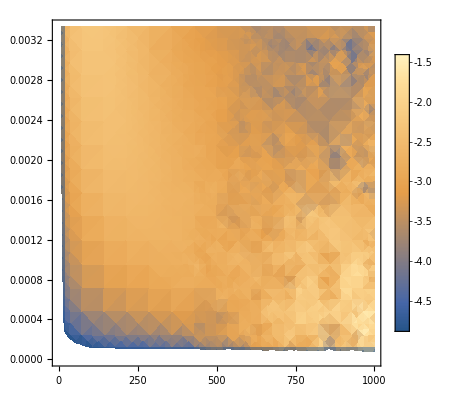

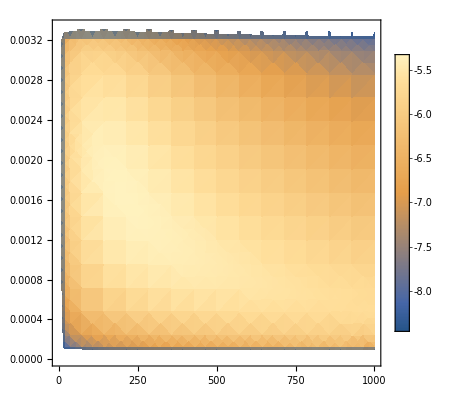

```mathematica
DensityPlot[Log10@Im[-1/ϵM[u,z,1]]/.{"χ"->1,"D"->300},{u,0,1000},{z,0,1/300},PlotLegends->Automatic]
DensityPlot[Log10@Im[ϵMnd[u,z,1]/(ϵM[u,z,1]Conjugate[ϵM[u,z,1]])]/.{"χ"->1,"D"->300},{u,0,1000},{z,0,1/300},PlotLegends->Automatic]
```

```mathematica
ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Abs[ϵM[0.5,0.001,1]]^2/.{"χ"->1,"D"->300}
```

2.97893×10^11+0. ⅈ

2.97893×10^11

### Cross-section and evaporation analytics for ϵnd

#### Integration bounds for dσ_nd dE_R

The integration bounds are given by the intersection of (0,1/D) and (z_-,z_+)

```mathematica
"if z_->1/D then the integral is 0 (region is empty)"
"if z_-<1/D<z_+ then the bounds are (z_-,1/D)"
"if z_+<1/D then the bounds are (z_-,z_+)"
"we want to summarize this with a single expression. We have a global factor of "
If[SubMinus[z]>=1/D,0,If[SubPlus[z]>1/D,"bounds are (z_-,1/D)", "bounds are (z_-,z_+)"]]
```

if z_->1/D then the integral is 0 (region is empty)

if z_-<1/D<z_+ then the bounds are (z_-,1/D)

if z_+<1/D then the bounds are (z_-,z_+)

we want to summarize this with a single expression. We have a global factor of

If[z_-≥1/D,0,If[z_+>1/D,bounds are (z_-,1/D),bounds are (z_-,z_+)]]

#### Evaporation distribution and bounds

```mathematica
"figure out the modification of the integrand needed to go from f_MB -> f_nd for the target"
fMBnorm = Assuming[βE mT/2 vT^2>0,Integrate[vT^2 E^(-βE mT/2 vT^2),{vT,0,∞}]]
FOccnDζnearkF/.ζ->(m vT)/(ℏ kF)
fndnorm =  Assuming[,Integrate[vT^2%,{vT,(m/(ℏ kF))^-1(1-1/D),(m/(ℏ kF))^-1(1+1/D)}]]//Simplify
```

figure out the modification of the integrand needed to go from f_MB -> f_nd for the target

(√(π/2))/(mT βE)^(3/2)

1/2 (1+D-(D m vT)/(kF ℏ))

((1-2 D+3 D^2) kF^3 ℏ^3)/(3 D^3 m^3)

#### ω st z integral returns 0

```mathematica
1/("D")==(mχ vχ- √(2 mχ (1/2 mχ vχ^2-ω ℏ)))/(2 kF ℏ)
Solve[%,ω]//Simplify
Solve[%%,vχ]//Simplify
```

1/D==(mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ω ℏ)))/(2 kF ℏ)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→(2 kF (D mχ vχ-kF ℏ))/(D^2 mχ)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{vχ→(D ω)/(2 kF)+(kF ℏ)/(D mχ)}}

```mathematica
AbsoluteTiming[Integrate[x,x]]
```

{0.0066989,x^2/2}

```mathematica
Monitor[Do[Pause[1],{i,10},{j,10}],{i,j}]
```

$Aborted

```mathematica
(mχ vχ- √(2 mχ (1/2 mχ vχ^2-ω ℏ)))/(2 kF ℏ)
D[%,vχ]//FullSimplify
"Derivative of RHS wrt vχ is negative"
D[%%%,ω]//FullSimplify
"Derivative of RHS wrt ω is positive"
```

(mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ω ℏ)))/(2 kF ℏ)

(mχ (2-(2 mχ vχ)/(√(mχ (mχ vχ^2-2 ω ℏ)))))/(4 kF ℏ)

Derivative of RHS wrt vχ is negative

mχ/(2 kF √(mχ (mχ vχ^2-2 ω ℏ)))

Derivative of RHS wrt ω is positive

#### More kinematics

```mathematica
HeavisideTheta[ωm-ω]HeavisideTheta[ωp+ω]/.ωm->q v - (ℏ q^2)/(2 mχ) /.ωp->q v + (ℏ q^2)/(2 mχ) 
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,0,1}]
Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q]
HeavisideTheta[q-(q/.%[[1]])]HeavisideTheta[q-(q/.%[[2]])]
```

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

-Graphics-

{{q→-(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ}}

HeavisideTheta[q+(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ] HeavisideTheta[q-(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

```mathematica
HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)]HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)](*HeavisideTheta[1/2 mχ v^2 +ω ℏ]*)
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,1}]
```

HeavisideTheta[q v-ω-(q^2 ℏ)/(2 mχ)] HeavisideTheta[q v+ω+(q^2 ℏ)/(2 mχ)]

-Graphics-

```mathematica
qp=q/.Solve[q v-ω-(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
mqm = q /.Solve[q v+ω+(q^2 ℏ)/(2 mχ)==0,q][[2]]//Simplify
HeavisideTheta[qp-q]HeavisideTheta[q-mqm]
DensityPlot[%/.ℏ->1/.mχ->1/.v->1,{q,0,3},{ω,-1,0}]
```

(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ

HeavisideTheta[q-(-mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ] HeavisideTheta[-q+(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ]

-Graphics-

```mathematica
mqm/.ω->-Abs[ω]
D[%,ω]
```

(-mχ v+√mχ √(mχ v^2+2 ℏ Abs[ω]))/ℏ

(√mχ Abs'[ω])/(√(mχ v^2+2 ℏ Abs[ω]))

```mathematica
Clear[Absωsol]
Solve[(mqm/(2 kF)/.ω->-Abs[ω])==1/D,Abs[ω]]
Absωsol=(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)
(*Solve[(mqm/(2 kF))==1/D,ω]*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Abs[ω]→(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)}}

(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)

```mathematica
Solve[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)==mχ/(2 ℏ)(vesc^2-v^2),v]//Simplify
```

{{v→-vesc-(2 kF ℏ)/(D mχ)},{v→vesc-(2 kF ℏ)/(D mχ)}}

```mathematica
D[-mχ/(2 ℏ)(vesc^2-v^2)+(2 (D kF mχ v-kF^2 ℏ))/(D^2 mχ),v]
Solve[%==0,v]
```

(2 kF)/D+(mχ v)/ℏ

{{v→-(2 kF ℏ)/(D mχ)}}

```mathematica
{ℏ->1,D->300,mχ->1,kF->10,vesc->1}
Show[{Plot[(2 (D kF mχ v+kF^2 ℏ))/(D^2 mχ)/.%,{v,0,1},PlotRange->All],
Plot[mχ/(2 ℏ)(vesc^2-v^2)/.%,{v,0,1},PlotStyle->Black]}]
(2kF ℏ)/(D mχ)/.%%
vesc /.%%%
```

{ℏ→1,D→300,mχ→1,kF→10,vesc→1}

-Graphics-

1/15

1

```mathematica
"D"/.FeTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

```mathematica
("ℏ""qF""c")/("JpereV""D")/.SIConstRepl/.FeTotalparams
```

{8.90855,7.26316,5.52827,2.84744,0.561296,0.122416}

```mathematica
"vF"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
```

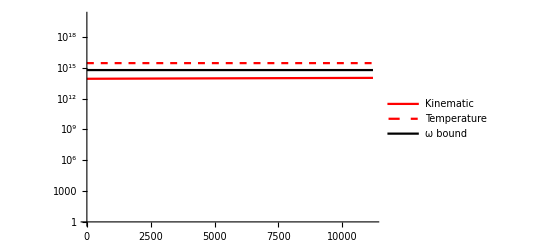

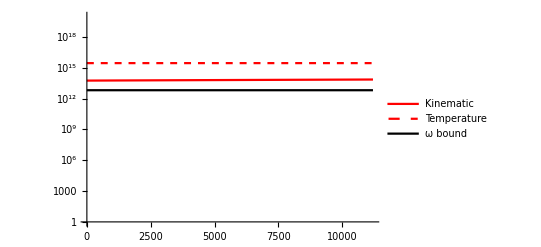

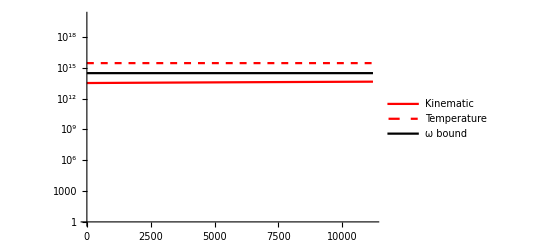

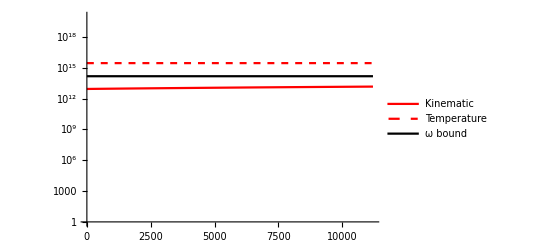

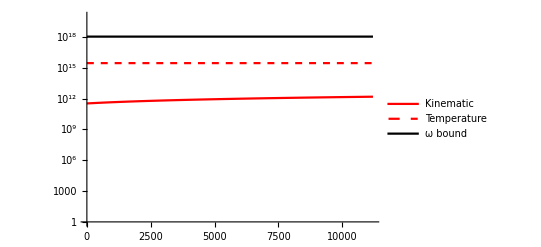

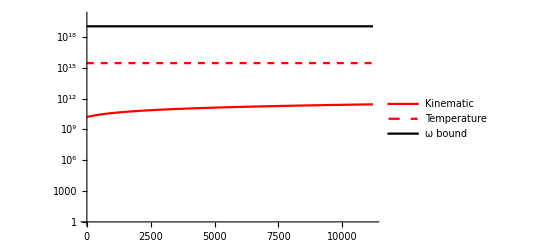

```mathematica
Do[Print@Show[{LogPlot[2 vχ ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.FeTotalparams[[o]]/.mχ->10^6("JpereV")/("c")^2/.SIConstRepl,{vχ,0,"vesc"/.EarthRepl},PlotStyle->Red,PlotRange->{10^0,10^20},PlotLegends->LineLegend[{Red,Directive[Red,Dashed],Black},{"Kinematic","Temperature","ω bound"}]],LogPlot[4/("β""ℏ")/.FeTotalparams[[o]],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Directive[Red,Dashed]],LogPlot["ωedgei"/.FeTotalparams[[o]],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Black]}],{o,Length[FeTotalparams]}]
```

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[MgOTotalparams]}]},{m,6,15}]
(*"The lowest rescaling we can do where evaporation is still 0 is b=4"
Drescale = "D"->("D")/b/.b->4
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"The first rescaling where it is non-zero is b=5"
Drescale = "D"->("D")/b/.b->5
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
"This tells us that the energy threshold is less than ωedgei for most of the oscillators we consider. The conduction band of iron is the lowest, and only begins to contribute to the rate between b of 4-5 so about an additional suppression of 10^-4, and only for electron mass aDM "
Drescale = "D"->("D")/b/.b->8
Table[{m,Table[(v-"vesc"/.EarthRepl)/.Solve["ωedgei"==2 v ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,v][[1]],{i,Length[FeTotalparams]}]},{m,6,15}]
"So we need this much suppression to get contributions from higher masses"*)
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | 293771.
-47548.7
244538.
251972.
1.01741×10^10
4.70135×10^11
7 | 339141.
-10559.2
272692.
266473.
1.01741×10^10
4.70135×10^11
8 | 343677.
-6860.2
275507.
267924.
1.01741×10^10
4.70135×10^11
9 | 344131.
-6490.31
275789.
268069.
1.01741×10^10
4.70135×10^11
10 | 344177.
-6453.32
275817.
268083.
1.01741×10^10
4.70135×10^11
11 | 344181.
-6449.62
275820.
268085.
1.01741×10^10
4.70135×10^11
12 | 344182.
-6449.25
275820.
268085.
1.01741×10^10
4.70135×10^11
13 | 344182.
-6449.21
275820.
268085.
1.01741×10^10
4.70135×10^11
14 | 344182.
-6449.21
275820.
268085.
1.01741×10^10
4.70135×10^11
15 | 344182.
-6449.21
275820.
268085.
1.01741×10^10
4.70135×10^11

{{6,{2.61001×10^7,4.44864×10^7}},{7,{2.61139×10^7,4.44945×10^7}},{8,{2.61152×10^7,4.44953×10^7}},{9,{2.61154×10^7,4.44954×10^7}},{10,{2.61154×10^7,4.44954×10^7}},{11,{2.61154×10^7,4.44954×10^7}},{12,{2.61154×10^7,4.44954×10^7}},{13,{2.61154×10^7,4.44954×10^7}},{14,{2.61154×10^7,4.44954×10^7}},{15,{2.61154×10^7,4.44954×10^7}}}

{{6,{1.63346×10^7,2.18293×10^7,2.33362×10^7,3.61145×10^7}},{7,{1.63538×10^7,2.18437×10^7,2.33496×10^7,3.61233×10^7}},{8,{1.63558×10^7,2.18451×10^7,2.3351×10^7,3.61241×10^7}},{9,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{10,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{11,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{12,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{13,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{14,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}},{15,{1.6356×10^7,2.18453×10^7,2.33511×10^7,3.61242×10^7}}}

```mathematica
"same as above, but for the raw kinematic constraint"
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(2 "ℏ""qF")/("D" mχ)/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]//TableForm
```

same as above, but for the raw kinematic constraint

D→D

6 | -100820.
-82198.9
-62564.8
-32225.2
-6352.32
-1385.41
7 | -10082.
-8219.89
-6256.48
-3222.52
-635.232
-138.541
8 | -1008.2
-821.989
-625.648
-322.252
-63.5232
-13.8541
9 | -100.82
-82.1989
-62.5648
-32.2252
-6.35232
-1.38541
10 | -10.082
-8.21989
-6.25648
-3.22252
-0.635232
-0.138541
11 | -1.0082
-0.821989
-0.625648
-0.322252
-0.0635232
-0.0138541
12 | -0.10082
-0.0821989
-0.0625648
-0.0322252
-0.00635232
-0.00138541
13 | -0.010082
-0.00821989
-0.00625648
-0.00322252
-0.000635232
-0.000138541
14 | -0.0010082
-0.000821989
-0.000625648
-0.000322252
-0.0000635232
-0.0000138541
15 | -0.00010082
-0.0000821989
-0.0000625648
-0.0000322252
-6.35232×10^-6
-1.38541×10^-6

6 | -30658.4
-17997.3
7 | -3065.84
-1799.73
8 | -306.584
-179.973
9 | -30.6584
-17.9973
10 | -3.06584
-1.79973
11 | -0.306584
-0.179973
12 | -0.0306584
-0.0179973
13 | -0.00306584
-0.00179973
14 | -0.000306584
-0.000179973
15 | -0.0000306584
-0.0000179973

6 | -42725.8
-31995.1
-29932.8
-19352.2
7 | -4272.58
-3199.51
-2993.28
-1935.22
8 | -427.258
-319.951
-299.328
-193.522
9 | -42.7258
-31.9951
-29.9328
-19.3522
10 | -4.27258
-3.19951
-2.99328
-1.93522
11 | -0.427258
-0.319951
-0.299328
-0.193522
12 | -0.0427258
-0.0319951
-0.0299328
-0.0193522
13 | -0.00427258
-0.00319951
-0.00299328
-0.00193522
14 | -0.000427258
-0.000319951
-0.000299328
-0.000193522
15 | -0.0000427258
-0.0000319951
-0.0000299328
-0.0000193522

```mathematica
"What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?"
mχ/2(("vesc")^2-vχ^2)=="EF"
Solve[%,vχ][[2]]
Table[{m,%/.FeTotalparams/.Constants`EarthRepl/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl//Simplify},{m,6,15}]
"imaginary part implies EF is more than enough to evaporate at any velocity"
```

What is the minimum velocity for evaporation we can have if we ignored the fermi suppression?

1/2 mχ (vesc^2-vχ^2)==EF

{vχ→(√(-2 EF+vesc^2 mχ))/(√mχ)}

{{6,{{vχ→0.+1.20449×10^6 ⅈ},{vχ→0.+1.47738×10^6 ⅈ},{vχ→0.+1.94103×10^6 ⅈ},{vχ→0.+3.76854×10^6 ⅈ},{vχ→0.+1.91178×10^7 ⅈ},{vχ→0.+8.76579×10^7 ⅈ}}},{7,{{vχ→0.+380745. ⅈ},{vχ→0.+467067. ⅈ},{vχ→0.+613716. ⅈ},{vχ→0.+1.19167×10^6 ⅈ},{vχ→0.+6.04557×10^6 ⅈ},{vχ→0.+2.77199×10^7 ⅈ}}},{8,{{vχ→0.+119933. ⅈ},{vχ→0.+147317. ⅈ},{vχ→0.+193783. ⅈ},{vχ→0.+376689. ⅈ},{vχ→0.+1.91175×10^6 ⅈ},{vχ→0.+8.76579×10^6 ⅈ}}},{9,{{vχ→0.+36407.2 ⅈ},{vχ→0.+45357.8 ⅈ},{vχ→0.+60351.4 ⅈ},{vχ→0.+118645. ⅈ},{vχ→0.+604454. ⅈ},{vχ→0.+2.77196×10^6 ⅈ}}},{10,{{vχ→0.+4433.12 ⅈ},{vχ→0.+9635.21 ⅈ},{vχ→0.+15853.5 ⅈ},{vχ→0.+35982.8 ⅈ},{vχ→0.+190850. ⅈ},{vχ→0.+876508. ⅈ}}},{11,{{vχ→10532.4},{vχ→10179.},{vχ→9368.17},{vχ→0.+4071.86 ⅈ},{vχ→0.+59409.3 ⅈ},{vχ→0.+276972. ⅈ}}},{12,{{vχ→11135.},{vχ→11102.1},{vχ→11030.5},{vχ→10546.9},{vχ→0.+15493.5 ⅈ},{vχ→0.+86939.5 ⅈ}}},{13,{{vχ→11193.5},{vχ→11190.3},{vχ→11183.2},{vχ→11136.4},{vχ→9428.2},{vχ→0.+25356.5 ⅈ}}},{14,{{vχ→11199.4},{vχ→11199.},{vχ→11198.3},{vχ→11193.7},{vχ→11035.6},{vχ→6971.43}}},{15,{{vχ→11199.9},{vχ→11199.9},{vχ→11199.8},{vχ→11199.4},{vχ→11183.7},{vχ→10851.5}}}}

imaginary part implies EF is more than enough to evaporate at any velocity

#### Kinematics working with Energy instead of ζ

```mathematica
1/2-("D")/4(Eζ-1)/.Eζ->(-2+"D")/("D")//Simplify
```

1

1/2-(D Δ)/4

1/2-1/4 D (-1+Ee/EF)

{Ee→((2+D) EF)/D}

{Ee→((-2+D) EF)/D}

(4 EF)/D

So in terms of momenta

{{ζ→-2/(√D)},{ζ→2/(√D)}}

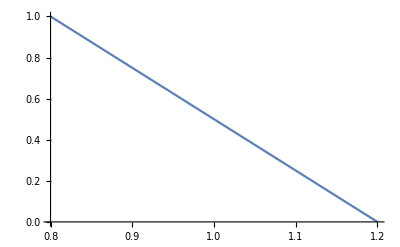

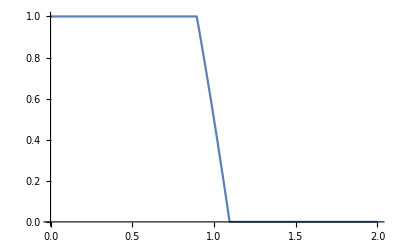

```mathematica
Series[ 1/(1 + E^("D"Δ)),{Δ,0,1}]//Normal
%/.Δ->Ee/EF-1
Solve[%==0,Ee][[1]]
Solve[%%==1,Ee][[1]]
(Ee/.%%)-(Ee/.%)//Simplify
"So in terms of momenta"
Solve[ℏ^2(ζ^2 kF^2)/(2 m)==ℏ^2 4/D kF^2/(2 m),ζ]
Plot[1/2-("D")/4(Eζ-1)/."D"->10,{Eζ,(-2+"D")/("D")/."D"->10,(2+"D")/("D")/."D"->10},PlotRange->All]
Plot[HeavisideTheta[√((-2+"D")/("D"))-ζ] +(1/2-("D")/4(ζ^2-1))HeavisideTheta[ζ-√((-2+"D")/("D"))]HeavisideTheta[√((2+"D")/("D"))-ζ]/."D"->10,(*{ζ,√((-2+"D")/("D"))/."D"->10,√((2+"D")/("D"))/."D"->10}*){ζ,0,2}]
```

```mathematica
ℏ ω<4 EF/D
```

ω ℏ<(4 EF)/D

```mathematica
Solve[4 EF/D==mχ/2(vesc^2-v^2),v]//PowerExpand
Series[v/.%[[2]],{D,∞,1}]//PowerExpand//Normal
```

{{v→-(√(-8 EF+D mχ vesc^2))/(√D √mχ)},{v→(√(-8 EF+D mχ vesc^2))/(√D √mχ)}}

-(4 EF)/(D mχ vesc)+vesc

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]//TableForm
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]
"So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is"
(4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[2]]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

-1.48805
-1.88182
-1.68663
-1.78616
716.214
7235.11

{-0.90446,-0.90446}

{-0.90446,-0.90446,-0.90446,-0.90446}

So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is

1.88616

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | -1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
7 | -1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
8 | -140366.
-140366.
-140366.
-140366.
-140366.
-140366.
9 | -3956.64
-3956.64
-3956.64
-3956.64
-3956.64
-3956.64
10 | 9684.34
9684.34
9684.34
9684.34
9684.34
9684.34
11 | 11048.4
11048.4
11048.4
11048.4
11048.4
11048.4
12 | 11184.8
11184.8
11184.8
11184.8
11184.8
11184.8
13 | 11198.5
11198.5
11198.5
11198.5
11198.5
11198.5
14 | 11199.8
11199.8
11199.8
11199.8
11199.8
11199.8
15 | 11200.
11200.
11200.
11200.
11200.
11200.

{{6,{-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.}},{8,{-61479.8,-61479.8}},{9,{3932.02,3932.02}},{10,{10473.2,10473.2}},{11,{11127.3,11127.3}},{12,{11192.7,11192.7}},{13,{11199.3,11199.3}},{14,{11199.9,11199.9}},{15,{11200.,11200.}}}

{{6,{-7.25678×10^6,-7.25678×10^6,-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.,-715598.,-715598.}},{8,{-61479.8,-61479.8,-61479.8,-61479.8}},{9,{3932.02,3932.02,3932.02,3932.02}},{10,{10473.2,10473.2,10473.2,10473.2}},{11,{11127.3,11127.3,11127.3,11127.3}},{12,{11192.7,11192.7,11192.7,11192.7}},{13,{11199.3,11199.3,11199.3,11199.3}},{14,{11199.9,11199.9,11199.9,11199.9}},{15,{11200.,11200.,11200.,11200.}}}

```mathematica
("βcore")^-1/.EarthRepl
("β")^-1/.FeTotalparams
("EF")/("D")/.FeTotalparams
"ℏ""ωedgei"/.FeTotalparams
```

7.55407×10^-20

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{6.37768×10^-20,6.95108×10^-22,3.19641×10^-20,1.602×10^-20,1.1504×10^-16,1.15937×10^-15}

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{17.0944,25.7168,44.3904,167.324,4306.1,90529.8}

{88.6464,257.244}

{45.6437,81.3942,92.9963,222.484}

```mathematica
("βcrust")^-1/.EarthRepl
("β")^-1/.SiO2Totalparams
("EF")/("D")/.SiO2Totalparams
("β")^-1/.MgOTotalparams
("EF")/("D")/.MgOTotalparams
```

3.62236×10^-20

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

### Nearly degenerate case - energy variable

#### Distribution function working with Energy instead of ζ

```mathematica
1/2-("D")/4(Eζ-1)/.Eζ->(-2+"D")/("D")//Simplify
```

1

```mathematica
Series[ 1/(1 + E^("D"Δ)),{Δ,0,1}]//Normal
%/.Δ->Ee/EF-1
Solve[%==0,Ee][[1]]
Solve[%%==1,Ee][[1]]
(Ee/.%%)-(Ee/.%)//Simplify
"So in terms of momenta"
Solve[ℏ^2(ζ^2 kF^2)/(2 m)==ℏ^2 4/D kF^2/(2 m),ζ]
Plot[1/2-("D")/4(Eζ-1)/."D"->10,{Eζ,(-2+"D")/("D")/."D"->10,(2+"D")/("D")/."D"->10},PlotRange->All]
Plot[HeavisideTheta[√((-2+"D")/("D"))-ζ] +(1/2-("D")/4(ζ^2-1))HeavisideTheta[ζ-√((-2+"D")/("D"))]HeavisideTheta[√((2+"D")/("D"))-ζ]/."D"->10,(*{ζ,√((-2+"D")/("D"))/."D"->10,√((2+"D")/("D"))/."D"->10}*){ζ,0,2}]
```

1/2-(D Δ)/4

1/2-1/4 D (-1+Ee/EF)

{Ee→((2+D) EF)/D}

{Ee→((-2+D) EF)/D}

(4 EF)/D

So in terms of momenta

{{ζ→-2/(√D)},{ζ→2/(√D)}}

-Graphics-

-Graphics-

```mathematica
ζm
```

-(ⅈ √(1/2-D))/(√D)

```mathematica
fndE=1/2-1/4 D (ζ^2-1)
Eζp = 1 + 2/D
Eζm= 1 - 2/D
ζp = 1 + 1/D
ζm = 1 -1/D
```

1/2-1/4 D (-1+ζ^2)

1+2/D

1-2/D

1+1/D

1-1/D

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","θ(1-ζ)"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],
Plot[(HeavisideTheta[1-ζ]),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotStyle->Black,PlotRange->All,AxesLabel->Automatic,Exclusions->None]}]
```

300

16

-Graphics-

300

16

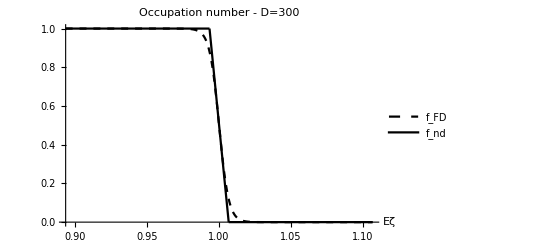

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+Eζ)))/.D->Dtemp),{Eζ,1-(2 rangerescale)/Dtemp,1 + (2 rangerescale)/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],Plot[(1/2-1/4 "D" (-1+Eζ)/."D"->Dtemp),{Eζ,1-2/Dtemp,1 + 2/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-Eζ],{Eζ,1-(2 rangerescale)/Dtemp,1-2/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-Eζ],{Eζ,1+2/Dtemp,1+(2 rangerescale)/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Initial and final states

```mathematica
{Eζm-(ℏ ω)/("EF"), ζ^2, Eζp}
%/.ζ->ζ+2 z//Expand
%-(4 z^2+4 z ζ)//Simplify
```

{Eζm-(ω ℏ)/EF,ζ^2,Eζp}

{Eζm-(ω ℏ)/EF,4 z^2+4 z ζ+ζ^2,Eζp}

{Eζm-4 z (z+ζ)-(ω ℏ)/EF,ζ^2,Eζp-4 z (z+ζ)}

#### Scattering Phase space

```mathematica
Solve[z == 1/2(√(1+2/D +(ℏ aω)/("EF"))- √(1 - 2/D)),aω][[1]]//Simplify
Series[aω/.%,{D,∞,1}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{aω→(4 EF (-1+D z (√((-2+D)/D)+z)))/(D ℏ)}

(4 EF z (1+z))/ℏ-(4 (EF (1+z)))/(ℏ D)+O[1/D]^2

```mathematica
Solve[z == 1/2(√(1+2/D)- √(1 - 2/D)),z][[1]]//Simplify
Series[z/.%,{D,∞,3}]
```

{z→1/2 (-√((-2+D)/D)+√((2+D)/D))}

1/D+1/(2 D^3)+O[1/D]^4

```mathematica
Series[√(1+2/D),{D,∞,1}]
Series[√(1-2/D),{D,∞,1}]
```

1+1/D+O[1/D]^2

1-1/D+O[1/D]^2

```mathematica
ℏ ω<4 EF/D
```

ω ℏ<(4 EF)/D

```mathematica
Solve[4 EF/D==mχ/2(vesc^2-v^2),v]//PowerExpand
Series[v/.%[[2]],{D,∞,1}]//PowerExpand//Normal
```

{{v→-(√(-8 EF+D mχ vesc^2))/(√D √mχ)},{v→(√(-8 EF+D mχ vesc^2))/(√D √mχ)}}

-(4 EF)/(D mχ vesc)+vesc

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]//TableForm
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]
Table[("ℏ""ωedgei"-4 ("EF")/("D"))("JpereV")^-1/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]
"So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is"
(4 ("EF")/("D"))("JpereV")^-1/.Drescale/.FeTotalparams[[2]]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

-1.48805
-1.88182
-1.68663
-1.78616
716.214
7235.11

{7.99554,7.99554}

{6.86554,6.86554,6.86554,6.86554}

So we see that expanding in energy instead of momenta made a huge difference. Now we are in line with expectation, just from the conduction band are we able to have non-zero energy transfer. And this is true independent of mass. So now we have to go back and recompute the dielectric with this correction. For the conduction band, the energy available to transfer in eV is

1.88616

```mathematica
"Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution."
Drescale = "D"->("D")/b/.b->1
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.FeTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[FeTotalparams]}]},{m,6,15}]//TableForm
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.SiO2Totalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[SiO2Totalparams]}]},{m,6,15}]
Table[{m,Table[-(4 "EF")/("D" mχ "vesc")+"vesc"/.Drescale/.MgOTotalparams[[i]]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl/.EarthRepl,{i,Length[MgOTotalparams]}]},{m,6,15}]
```

Looking at the velocity required to have a phase space for evaporation. negative values in the table implies the minimum velocity required to have a phase space is less than vesc, so we get some contribution.

D→D

6 | -1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
-1.51454×10^7
7 | -1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
-1.50446×10^6
8 | -140366.
-140366.
-140366.
-140366.
-140366.
-140366.
9 | -3956.64
-3956.64
-3956.64
-3956.64
-3956.64
-3956.64
10 | 9684.34
9684.34
9684.34
9684.34
9684.34
9684.34
11 | 11048.4
11048.4
11048.4
11048.4
11048.4
11048.4
12 | 11184.8
11184.8
11184.8
11184.8
11184.8
11184.8
13 | 11198.5
11198.5
11198.5
11198.5
11198.5
11198.5
14 | 11199.8
11199.8
11199.8
11199.8
11199.8
11199.8
15 | 11200.
11200.
11200.
11200.
11200.
11200.

{{6,{-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.}},{8,{-61479.8,-61479.8}},{9,{3932.02,3932.02}},{10,{10473.2,10473.2}},{11,{11127.3,11127.3}},{12,{11192.7,11192.7}},{13,{11199.3,11199.3}},{14,{11199.9,11199.9}},{15,{11200.,11200.}}}

{{6,{-7.25678×10^6,-7.25678×10^6,-7.25678×10^6,-7.25678×10^6}},{7,{-715598.,-715598.,-715598.,-715598.}},{8,{-61479.8,-61479.8,-61479.8,-61479.8}},{9,{3932.02,3932.02,3932.02,3932.02}},{10,{10473.2,10473.2,10473.2,10473.2}},{11,{11127.3,11127.3,11127.3,11127.3}},{12,{11192.7,11192.7,11192.7,11192.7}},{13,{11199.3,11199.3,11199.3,11199.3}},{14,{11199.9,11199.9,11199.9,11199.9}},{15,{11200.,11200.,11200.,11200.}}}

```mathematica
("βcore")^-1/.EarthRepl
("β")^-1/.FeTotalparams
("EF")/("D")/.FeTotalparams
"ℏ""ωedgei"/.FeTotalparams
```

7.55407×10^-20

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20,7.55407×10^-20}

{6.37768×10^-20,6.95108×10^-22,3.19641×10^-20,1.602×10^-20,1.1504×10^-16,1.15937×10^-15}

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{17.0944,25.7168,44.3904,167.324,4306.1,90529.8}

{88.6464,257.244}

{45.6437,81.3942,92.9963,222.484}

```mathematica
("βcrust")^-1/.EarthRepl
("β")^-1/.SiO2Totalparams
("EF")/("D")/.SiO2Totalparams
("β")^-1/.MgOTotalparams
("EF")/("D")/.MgOTotalparams
```

3.62236×10^-20

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

{3.62236×10^-20,3.62236×10^-20,3.62236×10^-20,3.62236×10^-20}

```mathematica
"We also have the constraint"
Solve[mχ/(2 ℏ)(vesc^2-vχ^2)==4/(β ℏ),vχ]//PowerExpand//Simplify
```

We also have the constraint

{{vχ→-(√(-8+mχ vesc^2 β))/(√mχ √β)},{vχ→(√(-8+mχ vesc^2 β))/(√mχ √β)}}

```mathematica
Re[√-2]
```

0

```mathematica
Log10@2980.110319634994
```

3.47423

```mathematica
10^3.85
```

7079.46

#### Phase space constraint from kinematics

```mathematica
ωp = q v + (ℏ q^2)/(2 mχ)
ωm = q v - (ℏ q^2)/(2 mχ)
ωm - ω > 0 
ωp + ω > 0
```

q v+(q^2 ℏ)/(2 mχ)

q v-(q^2 ℏ)/(2 mχ)

q v-ω-(q^2 ℏ)/(2 mχ)>0

q v+ω+(q^2 ℏ)/(2 mχ)>0

```mathematica
ωm + aω > 0 
ωp - aω > 0
```

aω+q v-(q^2 ℏ)/(2 mχ)>0

-aω+q v+(q^2 ℏ)/(2 mχ)>0

```mathematica
Solve[- mχ v + √(2 mχ(mχ/2 v^2+ aω ℏ))== 2 ℏ kF zndmax,aω][[1]]
ℏ aω<(ℏ aω/.%)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{aω→(2 (kF mχ v zndmax+kF^2 zndmax^2 ℏ))/mχ}

aω ℏ<(2 ℏ (kF mχ v zndmax+kF^2 zndmax^2 ℏ))/mχ

```mathematica
Solve[mχ/(2 ℏ)(vesc^2-v^2)==2/mχ ℏ kF^2/D^2+2 v kF/D,v]
```

{{v→(-D mχ vesc-2 kF ℏ)/(D mχ)},{v→(D mχ vesc-2 kF ℏ)/(D mχ)}}

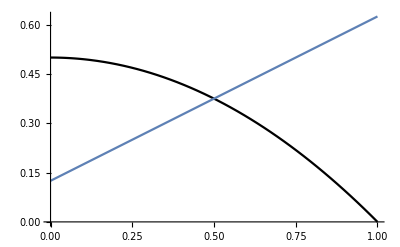

```mathematica
Show[{Plot[mχ/(2 ℏ)(vesc^2-v^2)/.{vesc->1,mχ->1,ℏ->1,D->4,kF->1},{v,0,1},PlotRange->All,PlotStyle->Black],
Plot[2/mχ ℏ kF^2/D^2+2 v kF/D/.{vesc->1,mχ->1,ℏ->1,D->4,kF->1},{v,0,1}]}]
```

#### Plot of constraints

```mathematica
"ℏ""JpereV"/.FeTotalparams[[2]]
```

1.69011×10^-53

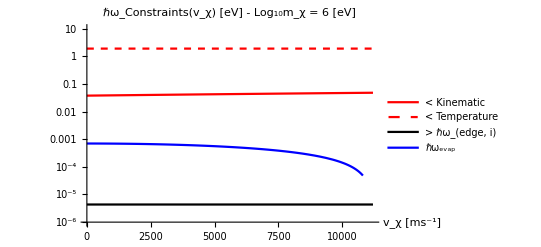

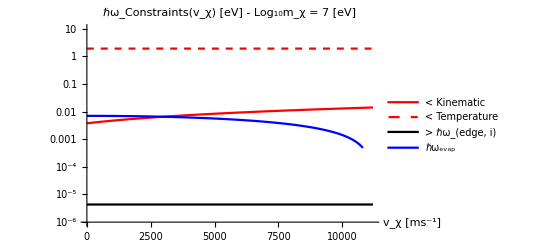

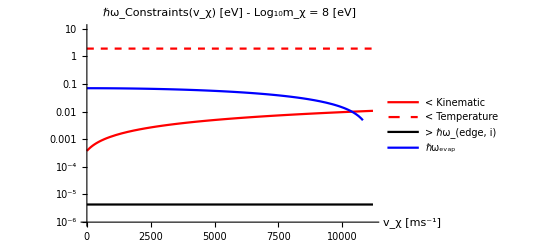

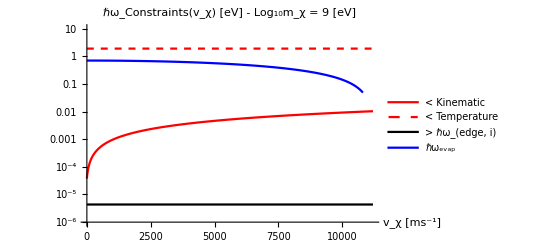

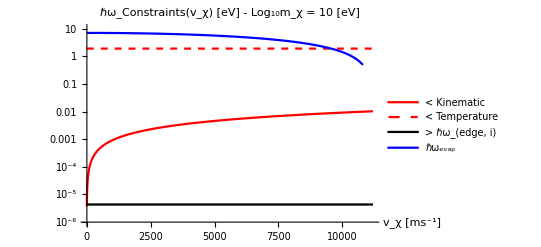

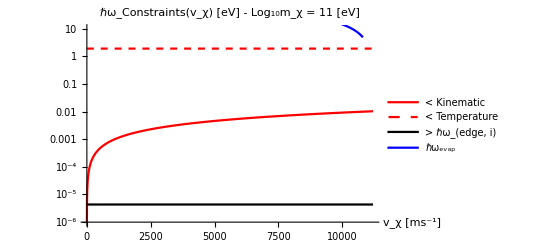

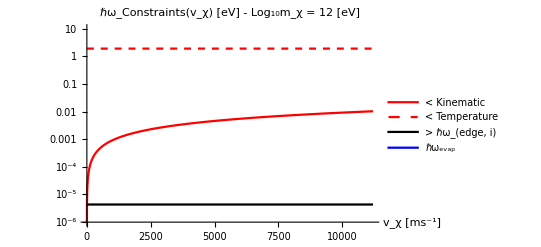

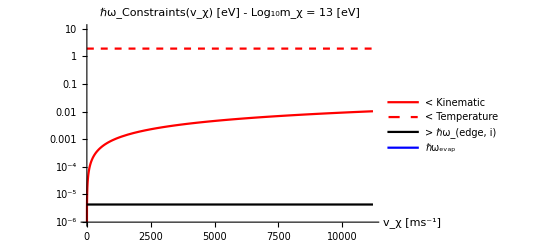

```mathematica
Do[Print@Show[{LogPlot[("ℏ")/("JpereV")(2 vχ ("qF")/("D")+2/mχ(("qF")/("D"))^2"ℏ")/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"]/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl,{vχ,0,"vesc"/.EarthRepl},PlotStyle->Red,PlotRange->{10^-6,10},(*PlotRange->All,*)PlotLegends->LineLegend[{Red,Directive[Red,Dashed],Black,Blue},{"< Kinematic","< Temperature","> ℏω_(edge, i)","ℏω_evap"}],PlotLabel->StringForm["ℏω_Constraints(v_χ) [eV] - Log_10m_χ = `` [eV]",ToString[m]],AxesLabel->{"v_χ [ms^-1]"}],LogPlot[("ℏ")/("JpereV")4/("β""ℏ")/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Directive[Red,Dashed]],LogPlot[("ℏ")/("JpereV")"ωedgei"/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Black],
LogPlot[("ℏ")/("JpereV")mχ/(2 "ℏ")(("vesc"/.EarthRepl)^2-vχ^2)/.mχ->10^m("JpereV")/("c")^2/.RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],{vχ,0,"vesc"/.EarthRepl},PlotStyle->Blue]}],{m,6,15}]
```

#### ftilde

```mathematica
1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3)
```

```mathematica
ftildeE = Integrate[ζ fndE,ζ]//Simplify
```

1/16 ζ^2 (4-D (-2+ζ^2))

```mathematica
"nearly degenerate case boundary term"
"Real part"
ReBound =ftildeE  Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =ftildeE Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

nearly degenerate case boundary term

Real part

1/32 ζ^2 (4-D (-2+ζ^2)) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

Imaginary part

1/16 ζ^2 (4-D (-2+ζ^2)) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

```mathematica
"nearly Degenerate case integral bulk"
"Real part"
ReBulk=-Integrate[ftildeE Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=-Integrate[ftildeE Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
```

nearly Degenerate case integral bulk

Real part

1/8 a ((4+D (2-a^2+3 uν^2)) ζ-(D ζ^3)/3+2 uν (2+D (1-a^2+uν^2)) ArcTan[(a-ζ)/uν]-2 uν (2+D (1-a^2+uν^2)) ArcTan[(a+ζ)/uν]-((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2-2 a ζ+ζ^2])/(4 a)+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2+2 a ζ+ζ^2])/(4 a))

Imaginary part

-1/16 uν (-2 (4+D (2-3 a^2+uν^2)) ζ+(2 D ζ^3)/3+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) ArcTan[(-a+ζ)/uν])/uν+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) ArcTan[(a+ζ)/uν])/uν-2 a (2+D (1-a^2+uν^2)) Log[a^2+uν^2-2 a ζ+ζ^2]+2 a (2+D (1-a^2+uν^2)) Log[a^2+uν^2+2 a ζ+ζ^2])

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

1/32 (4 a (4+D (2-a^2+3 uν^2)) ζ-4/3 a D ζ^3+8 a uν (2+D (1-a^2+uν^2)) ArcTan[(a-ζ)/uν]-8 a uν (2+D (1-a^2+uν^2)) ArcTan[(a+ζ)/uν]-(a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[uν^2+(a-ζ)^2]+ζ^2 (4-D (-2+ζ^2)) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]+(a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[uν^2+(a+ζ)^2])

1/16 (2/3 uν ζ (12-D (-6+9 a^2-3 uν^2+ζ^2))+(a^4 D-2 a^2 (2+D+3 D uν^2)+(uν^2+ζ^2) (4+D (2+uν^2-ζ^2))) ArcTan[(a-ζ)/uν]-(a^4 D-2 a^2 (2+D+3 D uν^2)+(uν^2+ζ^2) (4+D (2+uν^2-ζ^2))) ArcTan[(a+ζ)/uν]+2 a uν (-2+D (-1+a^2-uν^2)) (-Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

```mathematica
ReTotalWbounds=(ReTotal/.ζ->1+1/D- 2 zt/D )-(ReTotal/.ζ->1-1/D )//Simplify; (*zt = D z*)
ImTotalWbounds=(ImTotal/.ζ->1+1/D- 2 zt/D )-(ImTotal/.ζ->1-1/D )//Simplify;
```

```mathematica
Limit[ReTotalWbounds ,D->∞]
Limit[ImTotalWbounds ,D->∞]
```

0

0

```mathematica
Limit[ReTotalWbounds D,D->∞]
Limit[ImTotalWbounds D,D->∞]
```

-1/2 (-1+zt^2) Log[1+(4 a)/((-1+a)^2+uν^2)]

-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])

See the previous approach with the momentum variable. The imaginary part is Arctan - this is h(a,u_ν)

```mathematica
(ReBound/.ζ->1+1/D- 2 zt/D)-(ReBound/.ζ->1-1/D)//Simplify
Limit[%,D->∞]
1/4 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)];
(%/.ζ->1+1/D- 2 zt/D)-(%/.ζ->1-1/D)//Simplify
Limit[%,D->∞]
```

(-(-1+D)^2 (-1+6 D+D^2) Log[1+(4 a (-1+D))/(D ((-1+a+1/D)^2+uν^2))]+(4 D+2 D^2-(1+D-2 zt)^2) (1+D-2 zt)^2 Log[1+(4 a (1+D-2 zt))/(D (uν^2+(-1+(-1+a) D+2 zt)^2/D^2))])/(32 D^3)

-(a (-1+a^2+uν^2) (-1+zt))/(4 (1-2 a+a^2+uν^2) (1+2 a+a^2+uν^2))

(-(-1+D)^2 (5+D) Log[1+(4 a (-1+D))/(D ((-1+a+1/D)^2+uν^2))]+(1+D-2 zt)^2 (1+D+4 zt) Log[1+(4 a (1+D-2 zt))/(D (uν^2+(-1+(-1+a) D+2 zt)^2/D^2))])/(24 D^2)

-(a (-1+a^2+uν^2) (-1+zt))/(3 (1-2 a+a^2+uν^2) (1+2 a+a^2+uν^2))

```mathematica
(ReBulk/.ζ->1+1/D- 2 zt/D)-(ReBulk/.ζ->1-1/D)//Simplify
Limit[%,D->∞]
```

1/8 a ((-1+D)^3/(3 D^2)+((-1+D) (-4+D (-2+a^2-3 uν^2)))/D-((-4+D (-2+a^2-3 uν^2)) (1+D-2 zt))/D-(1+D-2 zt)^3/(3 D^2)+2 uν (2+D (1-a^2+uν^2)) ArcTan[(1+a-1/D)/uν]-2 uν (2+D (1-a^2+uν^2)) ArcTan[(-1+a+1/D)/uν]-2 uν (2+D (1-a^2+uν^2)) ArcTan[(1+D+a D-2 zt)/(D uν)]+2 uν (2+D (1-a^2+uν^2)) ArcTan[(-1+(-1+a) D+2 zt)/(D uν)]+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[1-2 a+a^2+1/D^2+(2 (-1+a))/D+uν^2])/(4 a)-((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[1+2 a+a^2+1/D^2-(2 (1+a))/D+uν^2])/(4 a)-((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2-(2 a (1+D-2 zt))/D+(1+D-2 zt)^2/D^2])/(4 a)+((a^4 D-2 a^2 (2+D+3 D uν^2)+uν^2 (4+D (2+uν^2))) Log[a^2+uν^2+(2 a (1+D-2 zt))/D+(1+D-2 zt)^2/D^2])/(4 a))

(a (-1+a^2+uν^2) (-1+zt))/(4 (a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2))

## Electronic Interpolation Analytics

#### Check cross-section units

```mathematica
"The dimensionfull quantities in our dσ cross-section are"
("e")^2/(vχ^2 ("ℏ")^2 "ne" "ϵ0")/."e"->√("α" 4 π "ϵ0" "ℏ" "c")
%/."ne"->L^-3 /.vχ->L T^-1 /."ℏ"-> M L T^-1 /."c"->L T^-1
%/.M -> J L^-1 T^2
```

The dimensionfull quantities in our dσ cross-section are

(4 c α π)/(ne ℏ vχ^2)

(4 α L π T^2)/M

(4 α L^2 π)/J

So the units of (d σ)/(d E_R)are Length squared per unit energy as needed

```mathematica
"in the EL function they are"
"ne" ("ℏ")^2 ω^2("e")^2/(vχ^2 ("ℏ")^2 "ne" "ϵ0")/."e"->√("α" 4 π "ϵ0" "ℏ" "c")
%/."ne"->L^-3 /.vχ->L T^-1 /."ℏ"-> M L T^-1 /."c"->L T^-1/.ω->T^-1
%/.M -> J L^-1 T^2
```

in the EL function they are

(4 c α ℏ π ω^2)/vχ^2

(4 α M π)/T^2

(4 α J π)/L

So for EL function they units are Energy per unit length as needed

#### Interpolation ξ range

```mathematica
"The prescription for ξ=(ω - SubscriptBox[ω, min])/ω_max range for interpolation is"
{ϵ ωmin/(ωmax-ωmin),1-ϵ ωmax/(ωmax - ωmin)}/.ωmax->mχ/(2 "ℏ") vχmax^2
"for some small ϵ (vχmax is 0.2 c for us), this is independent of the velocity"
```

The prescription for ξ=(ω - SubscriptBox[ω, min])/ω_max range for interpolation is

{(ϵ ωmin)/((mχ vχmax^2)/(2 ℏ)-ωmin),1-(mχ vχmax^2 ϵ)/(2 ℏ ((mχ vχmax^2)/(2 ℏ)-ωmin))}

for some small ϵ (vχmax is 0.2 c for us), this is independent of the velocity

```mathematica
"We now check that how close we are to the boundaries in ω using this prescription"
Do[ξrange=Table[{ϵ ("ωedgei")/(ωmax-"ωedgei"),1-ϵ ωmax/(ωmax - "ωedgei")}/.ωmax->mχ/(2 "ℏ") (0.2 "c")^2/.mχ->10^m ("JpereV")/("c")^2/.FeTotalparams[[1]]/.vχ->10^log10vχ/.ϵ->10^-2,{log10vχ,4,8}];
Print@Table[If[(mχ vχ^2)/(2 "ℏ")>"ωedgei",{ωofξ[Union[ξrange][[1,1]],"ωedgei",(mχ vχ^2)/(2 "ℏ")]/("ωedgei"),ωofξ[Union[ξrange][[1,2]],"ωedgei",(mχ vχ^2)/(2 "ℏ")]/((mχ vχ^2)/(2 "ℏ"))},{0,0}]/.mχ->10^m ("JpereV")/("c")^2/.vχ->10^log10vχ/.FeTotalparams[[1]],{log10vχ,4,8}],{m,6,15}]
"So we are within a few percent across the phase space"
```

We now check that how close we are to the boundaries in ω using this prescription

{{0,0},{0,0},{1.,0.990716},{1.00028,0.990007},{1.02778,0.99}}

{{0,0},{1.,0.997166},{1.,0.990072},{1.00028,0.990001},{1.02778,0.99}}

{{0,0},{1.,0.990717},{1.,0.990007},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.997166},{1.,0.990072},{1.,0.990001},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.990717},{1.,0.990007},{1.,0.99},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.990072},{1.,0.990001},{1.,0.99},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.990007},{1.,0.99},{1.,0.99},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.990001},{1.,0.99},{1.,0.99},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.99},{1.,0.99},{1.,0.99},{1.00028,0.99},{1.02778,0.99}}

{{1.,0.99},{1.,0.99},{1.,0.99},{1.00028,0.99},{1.02778,0.99}}

So we are within a few percent across the phase space

#### Interpolation integration over ξ subdivision

```mathematica
"The integration boundaries are"
{ξmin+0 Δξ,ξmin+10^-3 Δξ,ξmin+10^-2 Δξ,ξmin+10^-1 Δξ,ξmin+10^0 Δξ}
```

The integration boundaries are

{ξmin,Δξ/1000+ξmin,Δξ/100+ξmin,Δξ/10+ξmin,Δξ+ξmin}

```mathematica
"We have a list of boundaries and we want a simple way to integrate over each interval"
ξrange = {ξmin,ξmax};
Clear[Δξ]
(*Δξ = ξrange[[2]]-ξrange[[1]];*)
c0 = -4;
ξintervals = Table[{ξmin+If[c==c0,0,1] 10^(c-1)Δξ,+ξmin+10^c Δξ},{c,c0,0}]
ξintervals = Table[If[c==c0,0,1] 10^c Δξ+ξmin,{c,c0,0}]
```

We have a list of boundaries and we want a simple way to integrate over each interval

{{ξmin,Δξ/10000+ξmin},{Δξ/10000+ξmin,Δξ/1000+ξmin},{Δξ/1000+ξmin,Δξ/100+ξmin},{Δξ/100+ξmin,Δξ/10+ξmin},{Δξ/10+ξmin,Δξ+ξmin}}

{ξmin,Δξ/1000+ξmin,Δξ/100+ξmin,Δξ/10+ξmin,Δξ+ξmin}

```mathematica
"So it is simply given by the list of ranges"
c0 = 4;
ξintervals = Table[{ξmin+If[c==-c0,0,1] 10^(c-1)Δξ,+ξmin+10^c Δξ},{c,-c0,0}]
```

So it is simply given by the list of ranges

{{ξmin,Δξ/10000+ξmin},{Δξ/10000+ξmin,Δξ/1000+ξmin},{Δξ/1000+ξmin,Δξ/100+ξmin},{Δξ/100+ξmin,Δξ/10+ξmin},{Δξ/10+ξmin,Δξ+ξmin}}

```mathematica
ξintervals = Table[{ξmin+HeavisideTheta[c0+c-0.01] 10^(c-1)Δξ,+ξmin+10^c Δξ},{c,-c0,0}]
```

{{ξmin,Δξ/10000+ξmin},{Δξ/10000+ξmin,Δξ/1000+ξmin},{Δξ/1000+ξmin,Δξ/100+ξmin},{Δξ/100+ξmin,Δξ/10+ξmin},{Δξ/10+ξmin,Δξ+ξmin}}

#### Cross-section and EL Plots

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicts,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("σf"/.ElectronicσDicts[[eind,2]])["Grid"]
("σf"/.ElectronicσDicts[[eind,2]])["ValuesOnGrid"]
```

{{4.62242},{4.938},{5.25357},{5.56914},{5.88471},{6.20029},{6.51586},{6.83143},{7.14701},{7.46258},{7.77815}}

{-22.5543,-22.1663,-22.047,-21.9067,-21.5759,-21.1289,-21.3743,-21.9002,-22.7933,-24.3346,-26.1408}

{{4.62242,7.77815}}

{{4.12242,7.77815}}

{{3.62242,7.77815}}

{{3.12242,7.77815}}

{{2.62242,7.77815}}

{{2.12242,7.77815}}

{{1.62242,7.77815}}

{{1.12242,7.77815}}

{{0.622422,7.77815}}

{{0.122422,7.77815}}

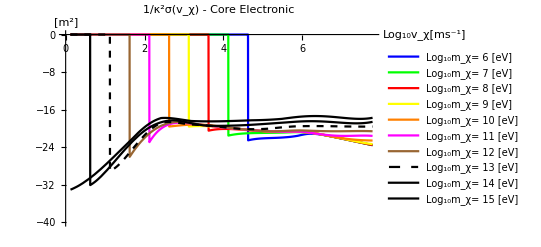

```mathematica
Quiet@Plot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("σf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print@Dom;
HeavisideTheta[vχ-Dom[[1,1]]]("σf"/.ElectronicσDicts[[eind,2]])[vχ]
,{m,6,15}]],{vχ,Dom[[1,1]],Dom[[1,2]]},AxesLabel->{"Log_10v_χ[ms^-1]","[m^2]"},PlotLabel->"1/κ^2σ(v_χ) - Core Electronic",PlotStyle->plotstyle,PlotRange->{-40,0},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

{{{4.62242,7.77815}},1}

{{{4.12242,7.77815}},2}

{{{3.62242,7.77815}},3}

{{{3.12242,7.77815}},4}

{{{2.62242,7.77815}},5}

{{{2.12242,7.77815}},6}

{{{1.62242,7.77815}},7}

{{{1.12242,7.77815}},8}

{{{0.622422,7.77815}},9}

{{{0.122422,7.77815}},10}

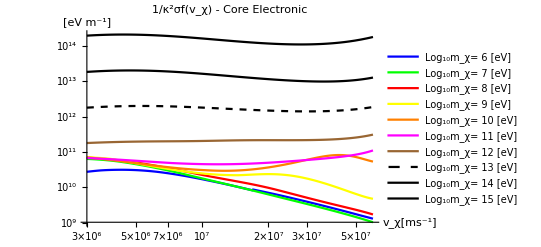

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("σf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print@{Dom,eind};
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic",PlotStyle->plotstyle,(*PlotRange->{10^7,10^12},*)PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

```mathematica
"vF"/.FeTotalparams
"ωi"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

{1.81874×10^16,2.47055×10^16,3.72046×10^16,1.00647×10^17,1.14999×10^18,1.12908×10^19}

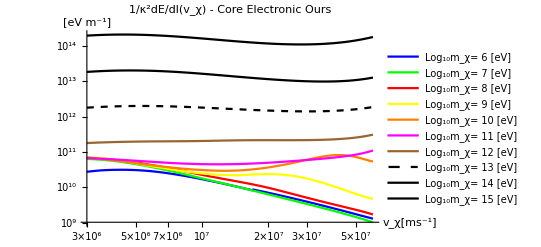

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

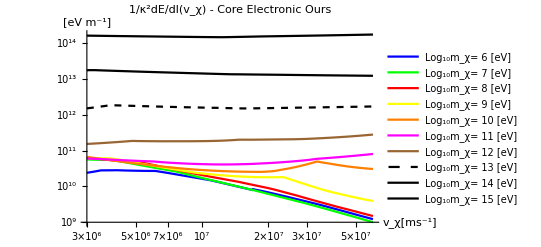

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

```mathematica
?ωmaxofvχ
```

```mathematica
Log10@(ωmaxofvχ[vχ,"mχ"/.ElectronicσDicts[[eind,1]],"params"/.ElectronicσDicts[[eind,1]]]-("ωedgei"/.("params"/.ElectronicσDicts[[eind,1]])))("dσf"/.ElectronicσDicts[[eind,1]])[vχ,ξ]/.vχ->10
```

1/Log[10]Log[-6.04519×10^14+8.43602×10^12 vχ^2] InterpolatingFunction[…][vχ,ξ]

{{5.60373,7.77815},{-6.70102,-0.00436489}}

{{5.10373,7.77815},{-7.70103,-0.00436481}}

{{4.60373,7.77815},{-8.70103,-0.00436481}}

{{4.10373,7.77815},{-9.70103,-0.00436481}}

{{3.60373,7.77815},{-10.701,-0.00436481}}

{{3.10373,7.77815},{-11.701,-0.00436481}}

{{2.60373,7.77815},{-12.701,-0.00436481}}

{{2.10373,7.77815},{-13.701,-0.00436481}}

{{1.60373,7.77815},{-14.701,-0.00436481}}

{{1.10373,7.77815},{-15.701,-0.00436481}}

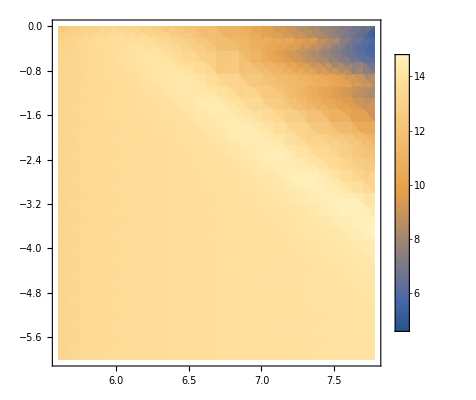
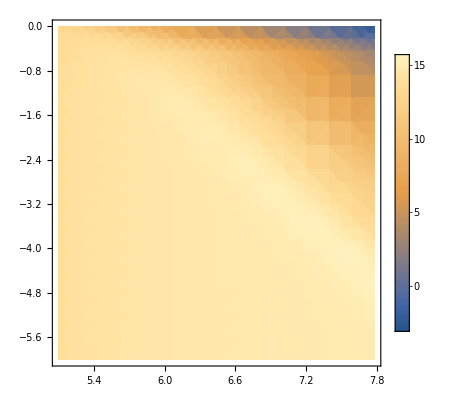
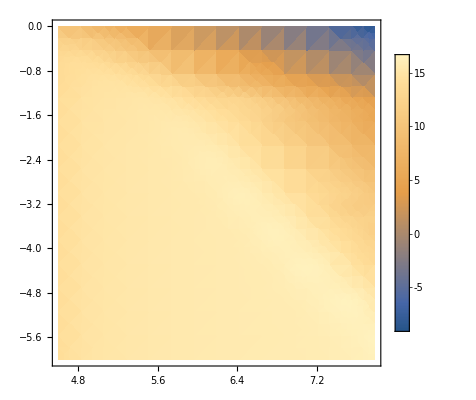
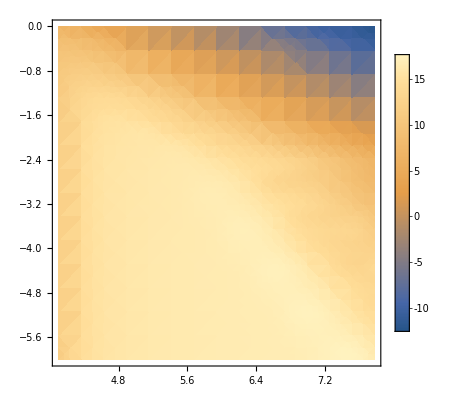
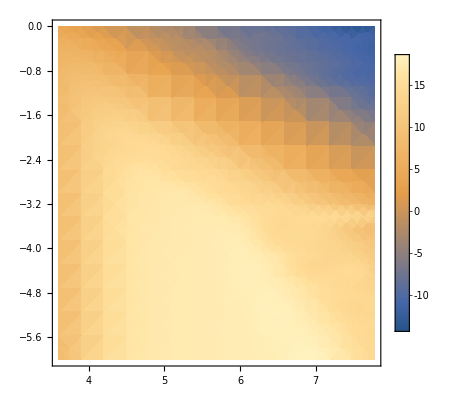
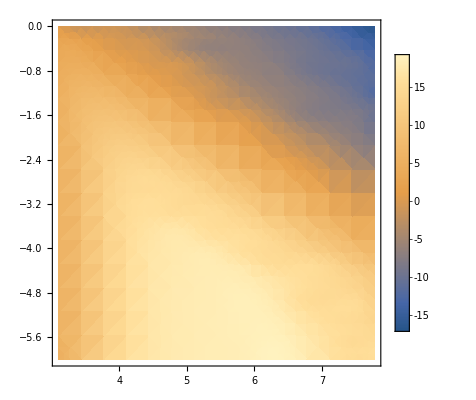
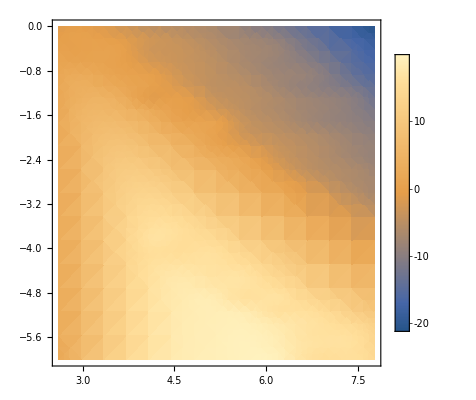
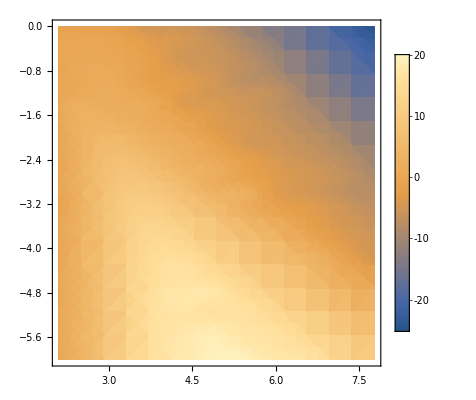

```mathematica
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dσf"/.ElectronicσDicts[[eind,1]])["Domain"];
Print[Dom];
DensityPlot[Log10@(ωmaxofvχ[10^vχ,"mχ"/.ElectronicσDicts[[eind,1]],"params"/.ElectronicσDicts[[eind,1]]]-("ωedgei"/.("params"/.ElectronicσDicts[[eind,1]])))+("dσf"/.ElectronicσDicts[[eind,1]])[vχ,ξ],{vχ,Dom[[1,1]],Dom[[1,2]]},{ξ,(*Dom[[2,1]]*)-6,Dom[[2,2]]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

```mathematica
(*("dσf"/.ElectronicσDicts[[1,2]])["Grid"]*)
(*(("JpereV")^-1/.Constants`SIConstRepl)10^*)(*("dσf"/.ElectronicσDicts[[1,2]])["ValuesOnGrid"]*)
("dσf"/.ElectronicσDicts[[10,2]])["Grid"]
(*(("JpereV")^-1/.Constants`SIConstRepl)10^*)("dσf"/.ElectronicσDicts[[10,2]])["ValuesOnGrid"]
```

{{{0.122422,-17.6636},{0.122422,-17.3693},{0.122422,-17.075},{0.122422,-16.7807},{0.122422,-16.4864},{0.122422,-16.192},{0.122422,-15.8977},{0.122422,-15.6034},{0.122422,-15.3091},{0.122422,-15.0147},{0.122422,-14.7204},{0.122422,-14.4261},{0.122422,-14.1318},{0.122422,-13.8375},{0.122422,-13.5431},{0.122422,-13.2488},{0.122422,-12.9545},{0.122422,-12.6602},{0.122422,-12.3659},{0.122422,-12.0715},{0.122422,-11.7772},{0.122422,-11.4829},{0.122422,-11.1886},{0.122422,-10.8943},{0.122422,-10.5999},{0.122422,-10.3056},{0.122422,-10.0113},{0.122422,-9.71697},{0.122422,-9.42265},{0.122422,-9.12832},{0.122422,-8.834},{0.122422,-8.53968},{0.122422,-8.24536},{0.122422,-7.95104},{0.122422,-7.65672},{0.122422,-7.3624},{0.122422,-7.06808},{0.122422,-6.77375},{0.122422,-6.47943},{0.122422,-6.18511},{0.122422,-5.89079},{0.122422,-5.59647},{0.122422,-5.30215},{0.122422,-5.00783},{0.122422,-4.7135},{0.122422,-4.41918},{0.122422,-4.12486},{0.122422,-3.83054},{0.122422,-3.53622},{0.122422,-3.2419},{0.122422,-2.94758},{0.122422,-2.65326},{0.122422,-2.35893},{0.122422,-2.06461},{0.122422,-1.77029},{0.122422,-1.47597},{0.122422,-1.18165},{0.122422,-0.887329},{0.122422,-0.593007},{0.122422,-0.298686},{0.122422,-0.00436481}},{{0.887995,-17.6636},{0.887995,-17.3693},{0.887995,-17.075},{0.887995,-16.7807},{0.887995,-16.4864},{0.887995,-16.192},{0.887995,-15.8977},{0.887995,-15.6034},{0.887995,-15.3091},{0.887995,-15.0147},{0.887995,-14.7204},{0.887995,-14.4261},{0.887995,-14.1318},{0.887995,-13.8375},{0.887995,-13.5431},{0.887995,-13.2488},{0.887995,-12.9545},{0.887995,-12.6602},{0.887995,-12.3659},{0.887995,-12.0715},{0.887995,-11.7772},{0.887995,-11.4829},{0.887995,-11.1886},{0.887995,-10.8943},{0.887995,-10.5999},{0.887995,-10.3056},{0.887995,-10.0113},{0.887995,-9.71697},{0.887995,-9.42265},{0.887995,-9.12832},{0.887995,-8.834},{0.887995,-8.53968},{0.887995,-8.24536},{0.887995,-7.95104},{0.887995,-7.65672},{0.887995,-7.3624},{0.887995,-7.06808},{0.887995,-6.77375},{0.887995,-6.47943},{0.887995,-6.18511},{0.887995,-5.89079},{0.887995,-5.59647},{0.887995,-5.30215},{0.887995,-5.00783},{0.887995,-4.7135},{0.887995,-4.41918},{0.887995,-4.12486},{0.887995,-3.83054},{0.887995,-3.53622},{0.887995,-3.2419},{0.887995,-2.94758},{0.887995,-2.65326},{0.887995,-2.35893},{0.887995,-2.06461},{0.887995,-1.77029},{0.887995,-1.47597},{0.887995,-1.18165},{0.887995,-0.887329},{0.887995,-0.593007},{0.887995,-0.298686},{0.887995,-0.00436481}},{{1.65357,-17.6636},{1.65357,-17.3693},{1.65357,-17.075},{1.65357,-16.7807},{1.65357,-16.4864},{1.65357,-16.192},{1.65357,-15.8977},{1.65357,-15.6034},{1.65357,-15.3091},{1.65357,-15.0147},{1.65357,-14.7204},{1.65357,-14.4261},{1.65357,-14.1318},{1.65357,-13.8375},{1.65357,-13.5431},{1.65357,-13.2488},{1.65357,-12.9545},{1.65357,-12.6602},{1.65357,-12.3659},{1.65357,-12.0715},{1.65357,-11.7772},{1.65357,-11.4829},{1.65357,-11.1886},{1.65357,-10.8943},{1.65357,-10.5999},{1.65357,-10.3056},{1.65357,-10.0113},{1.65357,-9.71697},{1.65357,-9.42265},{1.65357,-9.12832},{1.65357,-8.834},{1.65357,-8.53968},{1.65357,-8.24536},{1.65357,-7.95104},{1.65357,-7.65672},{1.65357,-7.3624},{1.65357,-7.06808},{1.65357,-6.77375},{1.65357,-6.47943},{1.65357,-6.18511},{1.65357,-5.89079},{1.65357,-5.59647},{1.65357,-5.30215},{1.65357,-5.00783},{1.65357,-4.7135},{1.65357,-4.41918},{1.65357,-4.12486},{1.65357,-3.83054},{1.65357,-3.53622},{1.65357,-3.2419},{1.65357,-2.94758},{1.65357,-2.65326},{1.65357,-2.35893},{1.65357,-2.06461},{1.65357,-1.77029},{1.65357,-1.47597},{1.65357,-1.18165},{1.65357,-0.887329},{1.65357,-0.593007},{1.65357,-0.298686},{1.65357,-0.00436481}},{{2.41914,-17.6636},{2.41914,-17.3693},{2.41914,-17.075},{2.41914,-16.7807},{2.41914,-16.4864},{2.41914,-16.192},{2.41914,-15.8977},{2.41914,-15.6034},{2.41914,-15.3091},{2.41914,-15.0147},{2.41914,-14.7204},{2.41914,-14.4261},{2.41914,-14.1318},{2.41914,-13.8375},{2.41914,-13.5431},{2.41914,-13.2488},{2.41914,-12.9545},{2.41914,-12.6602},{2.41914,-12.3659},{2.41914,-12.0715},{2.41914,-11.7772},{2.41914,-11.4829},{2.41914,-11.1886},{2.41914,-10.8943},{2.41914,-10.5999},{2.41914,-10.3056},{2.41914,-10.0113},{2.41914,-9.71697},{2.41914,-9.42265},{2.41914,-9.12832},{2.41914,-8.834},{2.41914,-8.53968},{2.41914,-8.24536},{2.41914,-7.95104},{2.41914,-7.65672},{2.41914,-7.3624},{2.41914,-7.06808},{2.41914,-6.77375},{2.41914,-6.47943},{2.41914,-6.18511},{2.41914,-5.89079},{2.41914,-5.59647},{2.41914,-5.30215},{2.41914,-5.00783},{2.41914,-4.7135},{2.41914,-4.41918},{2.41914,-4.12486},{2.41914,-3.83054},{2.41914,-3.53622},{2.41914,-3.2419},{2.41914,-2.94758},{2.41914,-2.65326},{2.41914,-2.35893},{2.41914,-2.06461},{2.41914,-1.77029},{2.41914,-1.47597},{2.41914,-1.18165},{2.41914,-0.887329},{2.41914,-0.593007},{2.41914,-0.298686},{2.41914,-0.00436481}},{{3.18471,-17.6636},{3.18471,-17.3693},{3.18471,-17.075},{3.18471,-16.7807},{3.18471,-16.4864},{3.18471,-16.192},{3.18471,-15.8977},{3.18471,-15.6034},{3.18471,-15.3091},{3.18471,-15.0147},{3.18471,-14.7204},{3.18471,-14.4261},{3.18471,-14.1318},{3.18471,-13.8375},{3.18471,-13.5431},{3.18471,-13.2488},{3.18471,-12.9545},{3.18471,-12.6602},{3.18471,-12.3659},{3.18471,-12.0715},{3.18471,-11.7772},{3.18471,-11.4829},{3.18471,-11.1886},{3.18471,-10.8943},{3.18471,-10.5999},{3.18471,-10.3056},{3.18471,-10.0113},{3.18471,-9.71697},{3.18471,-9.42265},{3.18471,-9.12832},{3.18471,-8.834},{3.18471,-8.53968},{3.18471,-8.24536},{3.18471,-7.95104},{3.18471,-7.65672},{3.18471,-7.3624},{3.18471,-7.06808},{3.18471,-6.77375},{3.18471,-6.47943},{3.18471,-6.18511},{3.18471,-5.89079},{3.18471,-5.59647},{3.18471,-5.30215},{3.18471,-5.00783},{3.18471,-4.7135},{3.18471,-4.41918},{3.18471,-4.12486},{3.18471,-3.83054},{3.18471,-3.53622},{3.18471,-3.2419},{3.18471,-2.94758},{3.18471,-2.65326},{3.18471,-2.35893},{3.18471,-2.06461},{3.18471,-1.77029},{3.18471,-1.47597},{3.18471,-1.18165},{3.18471,-0.887329},{3.18471,-0.593007},{3.18471,-0.298686},{3.18471,-0.00436481}},{{3.95029,-17.6636},{3.95029,-17.3693},{3.95029,-17.075},{3.95029,-16.7807},{3.95029,-16.4864},{3.95029,-16.192},{3.95029,-15.8977},{3.95029,-15.6034},{3.95029,-15.3091},{3.95029,-15.0147},{3.95029,-14.7204},{3.95029,-14.4261},{3.95029,-14.1318},{3.95029,-13.8375},{3.95029,-13.5431},{3.95029,-13.2488},{3.95029,-12.9545},{3.95029,-12.6602},{3.95029,-12.3659},{3.95029,-12.0715},{3.95029,-11.7772},{3.95029,-11.4829},{3.95029,-11.1886},{3.95029,-10.8943},{3.95029,-10.5999},{3.95029,-10.3056},{3.95029,-10.0113},{3.95029,-9.71697},{3.95029,-9.42265},{3.95029,-9.12832},{3.95029,-8.834},{3.95029,-8.53968},{3.95029,-8.24536},{3.95029,-7.95104},{3.95029,-7.65672},{3.95029,-7.3624},{3.95029,-7.06808},{3.95029,-6.77375},{3.95029,-6.47943},{3.95029,-6.18511},{3.95029,-5.89079},{3.95029,-5.59647},{3.95029,-5.30215},{3.95029,-5.00783},{3.95029,-4.7135},{3.95029,-4.41918},{3.95029,-4.12486},{3.95029,-3.83054},{3.95029,-3.53622},{3.95029,-3.2419},{3.95029,-2.94758},{3.95029,-2.65326},{3.95029,-2.35893},{3.95029,-2.06461},{3.95029,-1.77029},{3.95029,-1.47597},{3.95029,-1.18165},{3.95029,-0.887329},{3.95029,-0.593007},{3.95029,-0.298686},{3.95029,-0.00436481}},{{4.71586,-17.6636},{4.71586,-17.3693},{4.71586,-17.075},{4.71586,-16.7807},{4.71586,-16.4864},{4.71586,-16.192},{4.71586,-15.8977},{4.71586,-15.6034},{4.71586,-15.3091},{4.71586,-15.0147},{4.71586,-14.7204},{4.71586,-14.4261},{4.71586,-14.1318},{4.71586,-13.8375},{4.71586,-13.5431},{4.71586,-13.2488},{4.71586,-12.9545},{4.71586,-12.6602},{4.71586,-12.3659},{4.71586,-12.0715},{4.71586,-11.7772},{4.71586,-11.4829},{4.71586,-11.1886},{4.71586,-10.8943},{4.71586,-10.5999},{4.71586,-10.3056},{4.71586,-10.0113},{4.71586,-9.71697},{4.71586,-9.42265},{4.71586,-9.12832},{4.71586,-8.834},{4.71586,-8.53968},{4.71586,-8.24536},{4.71586,-7.95104},{4.71586,-7.65672},{4.71586,-7.3624},{4.71586,-7.06808},{4.71586,-6.77375},{4.71586,-6.47943},{4.71586,-6.18511},{4.71586,-5.89079},{4.71586,-5.59647},{4.71586,-5.30215},{4.71586,-5.00783},{4.71586,-4.7135},{4.71586,-4.41918},{4.71586,-4.12486},{4.71586,-3.83054},{4.71586,-3.53622},{4.71586,-3.2419},{4.71586,-2.94758},{4.71586,-2.65326},{4.71586,-2.35893},{4.71586,-2.06461},{4.71586,-1.77029},{4.71586,-1.47597},{4.71586,-1.18165},{4.71586,-0.887329},{4.71586,-0.593007},{4.71586,-0.298686},{4.71586,-0.00436481}},{{5.48143,-17.6636},{5.48143,-17.3693},{5.48143,-17.075},{5.48143,-16.7807},{5.48143,-16.4864},{5.48143,-16.192},{5.48143,-15.8977},{5.48143,-15.6034},{5.48143,-15.3091},{5.48143,-15.0147},{5.48143,-14.7204},{5.48143,-14.4261},{5.48143,-14.1318},{5.48143,-13.8375},{5.48143,-13.5431},{5.48143,-13.2488},{5.48143,-12.9545},{5.48143,-12.6602},{5.48143,-12.3659},{5.48143,-12.0715},{5.48143,-11.7772},{5.48143,-11.4829},{5.48143,-11.1886},{5.48143,-10.8943},{5.48143,-10.5999},{5.48143,-10.3056},{5.48143,-10.0113},{5.48143,-9.71697},{5.48143,-9.42265},{5.48143,-9.12832},{5.48143,-8.834},{5.48143,-8.53968},{5.48143,-8.24536},{5.48143,-7.95104},{5.48143,-7.65672},{5.48143,-7.3624},{5.48143,-7.06808},{5.48143,-6.77375},{5.48143,-6.47943},{5.48143,-6.18511},{5.48143,-5.89079},{5.48143,-5.59647},{5.48143,-5.30215},{5.48143,-5.00783},{5.48143,-4.7135},{5.48143,-4.41918},{5.48143,-4.12486},{5.48143,-3.83054},{5.48143,-3.53622},{5.48143,-3.2419},{5.48143,-2.94758},{5.48143,-2.65326},{5.48143,-2.35893},{5.48143,-2.06461},{5.48143,-1.77029},{5.48143,-1.47597},{5.48143,-1.18165},{5.48143,-0.887329},{5.48143,-0.593007},{5.48143,-0.298686},{5.48143,-0.00436481}},{{6.24701,-17.6636},{6.24701,-17.3693},{6.24701,-17.075},{6.24701,-16.7807},{6.24701,-16.4864},{6.24701,-16.192},{6.24701,-15.8977},{6.24701,-15.6034},{6.24701,-15.3091},{6.24701,-15.0147},{6.24701,-14.7204},{6.24701,-14.4261},{6.24701,-14.1318},{6.24701,-13.8375},{6.24701,-13.5431},{6.24701,-13.2488},{6.24701,-12.9545},{6.24701,-12.6602},{6.24701,-12.3659},{6.24701,-12.0715},{6.24701,-11.7772},{6.24701,-11.4829},{6.24701,-11.1886},{6.24701,-10.8943},{6.24701,-10.5999},{6.24701,-10.3056},{6.24701,-10.0113},{6.24701,-9.71697},{6.24701,-9.42265},{6.24701,-9.12832},{6.24701,-8.834},{6.24701,-8.53968},{6.24701,-8.24536},{6.24701,-7.95104},{6.24701,-7.65672},{6.24701,-7.3624},{6.24701,-7.06808},{6.24701,-6.77375},{6.24701,-6.47943},{6.24701,-6.18511},{6.24701,-5.89079},{6.24701,-5.59647},{6.24701,-5.30215},{6.24701,-5.00783},{6.24701,-4.7135},{6.24701,-4.41918},{6.24701,-4.12486},{6.24701,-3.83054},{6.24701,-3.53622},{6.24701,-3.2419},{6.24701,-2.94758},{6.24701,-2.65326},{6.24701,-2.35893},{6.24701,-2.06461},{6.24701,-1.77029},{6.24701,-1.47597},{6.24701,-1.18165},{6.24701,-0.887329},{6.24701,-0.593007},{6.24701,-0.298686},{6.24701,-0.00436481}},{{7.01258,-17.6636},{7.01258,-17.3693},{7.01258,-17.075},{7.01258,-16.7807},{7.01258,-16.4864},{7.01258,-16.192},{7.01258,-15.8977},{7.01258,-15.6034},{7.01258,-15.3091},{7.01258,-15.0147},{7.01258,-14.7204},{7.01258,-14.4261},{7.01258,-14.1318},{7.01258,-13.8375},{7.01258,-13.5431},{7.01258,-13.2488},{7.01258,-12.9545},{7.01258,-12.6602},{7.01258,-12.3659},{7.01258,-12.0715},{7.01258,-11.7772},{7.01258,-11.4829},{7.01258,-11.1886},{7.01258,-10.8943},{7.01258,-10.5999},{7.01258,-10.3056},{7.01258,-10.0113},{7.01258,-9.71697},{7.01258,-9.42265},{7.01258,-9.12832},{7.01258,-8.834},{7.01258,-8.53968},{7.01258,-8.24536},{7.01258,-7.95104},{7.01258,-7.65672},{7.01258,-7.3624},{7.01258,-7.06808},{7.01258,-6.77375},{7.01258,-6.47943},{7.01258,-6.18511},{7.01258,-5.89079},{7.01258,-5.59647},{7.01258,-5.30215},{7.01258,-5.00783},{7.01258,-4.7135},{7.01258,-4.41918},{7.01258,-4.12486},{7.01258,-3.83054},{7.01258,-3.53622},{7.01258,-3.2419},{7.01258,-2.94758},{7.01258,-2.65326},{7.01258,-2.35893},{7.01258,-2.06461},{7.01258,-1.77029},{7.01258,-1.47597},{7.01258,-1.18165},{7.01258,-0.887329},{7.01258,-0.593007},{7.01258,-0.298686},{7.01258,-0.00436481}},{{7.77815,-17.6636},{7.77815,-17.3693},{7.77815,-17.075},{7.77815,-16.7807},{7.77815,-16.4864},{7.77815,-16.192},{7.77815,-15.8977},{7.77815,-15.6034},{7.77815,-15.3091},{7.77815,-15.0147},{7.77815,-14.7204},{7.77815,-14.4261},{7.77815,-14.1318},{7.77815,-13.8375},{7.77815,-13.5431},{7.77815,-13.2488},{7.77815,-12.9545},{7.77815,-12.6602},{7.77815,-12.3659},{7.77815,-12.0715},{7.77815,-11.7772},{7.77815,-11.4829},{7.77815,-11.1886},{7.77815,-10.8943},{7.77815,-10.5999},{7.77815,-10.3056},{7.77815,-10.0113},{7.77815,-9.71697},{7.77815,-9.42265},{7.77815,-9.12832},{7.77815,-8.834},{7.77815,-8.53968},{7.77815,-8.24536},{7.77815,-7.95104},{7.77815,-7.65672},{7.77815,-7.3624},{7.77815,-7.06808},{7.77815,-6.77375},{7.77815,-6.47943},{7.77815,-6.18511},{7.77815,-5.89079},{7.77815,-5.59647},{7.77815,-5.30215},{7.77815,-5.00783},{7.77815,-4.7135},{7.77815,-4.41918},{7.77815,-4.12486},{7.77815,-3.83054},{7.77815,-3.53622},{7.77815,-3.2419},{7.77815,-2.94758},{7.77815,-2.65326},{7.77815,-2.35893},{7.77815,-2.06461},{7.77815,-1.77029},{7.77815,-1.47597},{7.77815,-1.18165},{7.77815,-0.887329},{7.77815,-0.593007},{7.77815,-0.298686},{7.77815,-0.00436481}}}

{{-11.2658,-11.2658,-11.2658,-11.2658,-11.2658,-11.2658,-11.2658,-11.555,-11.555,-11.0592,-12.2187,-11.4572,-11.9217,-11.3186,-11.4462,-12.5608,-11.0641,-11.4013,-11.8757,-11.5152,-11.4669,-11.8036,-11.3863,-12.552,-12.1224,-11.862,-11.1817,-11.6245,-11.924,-11.7198,-11.3512,-11.12,-11.7147,-11.3125,-11.4538,-11.8475,-11.4838,-11.4176,-11.4587,-11.0149,-11.3809,-11.4317,-11.9297,-11.4841,-11.8897,-10.9257,-11.6528,-11.526,-12.1449,-12.2519,-11.0888,-12.6558,-11.4714,-11.1984,-11.9281,-12.2743,-11.5411,-12.7573,-12.1277,-11.6995,-13.2433},{-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62694,-6.62693,-6.62694,-6.62692,-6.62693,-6.62694,-6.62694,-6.62692,-6.62693,-6.62694,-6.62692,-6.62694,-6.62692,-6.62692,-6.62692,-6.62693,-6.62693,-6.62692,-6.62694,-6.62693,-6.62693,-6.62694,-6.62693,-6.62693,-6.62692,-6.62694,-6.62694,-6.62696,-6.62697,-6.62699,-6.62703,-6.62712,-6.62732,-6.62768,-6.62842,-6.62983,-6.63266,-6.63822,-6.64911,-6.67047,-6.71222,-6.79316,-6.94789,-7.23125,-7.74294,-8.59039,-9.86453,-11.5524,-12.6595,-13.1545,-13.3398,-15.3458,-15.019},{-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.45649,-0.45649,-0.456491,-0.456493,-0.456497,-0.456504,-0.456519,-0.456548,-0.456605,-0.456717,-0.456937,-0.457371,-0.458226,-0.459909,-0.463222,-0.469737,-0.482535,-0.507616,-0.556535,-0.651095,-0.826403,-1.15719,-1.73591,-2.67178,-4.03832,-5.82613,-7.94887,-10.2905,-13.0055,-15.1005,-14.2528,-14.8785,-14.9177,-15.2502,-15.7566,-17.1908},{3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29832,3.29832,3.29831,3.29829,3.29826,3.29819,3.29805,3.29779,3.29726,3.29623,3.2942,3.29021,3.28233,3.26683,3.23627,3.18019,3.05601,2.42673,3.60157,1.91117,-0.0511733,-2.26439,-4.65266,-7.14159,-9.67235,-12.1996,-14.1125,-14.3614,-15.0843,-15.5709,-16.4347,-17.5416,-18.6334,-19.224,-19.7812,-20.3185},{2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10573,2.10573,2.10572,2.10571,2.10568,2.10563,2.10552,2.10532,2.10491,2.10411,2.10255,2.09949,2.09353,2.08211,2.06516,2.02677,1.96071,1.85113,1.66221,1.30574,1.46694,1.12507,-1.48855,-4.04973,-6.57605,-9.04447,-11.4518,-13.7117,-15.2303,-15.1323,-16.0607,-17.5572,-18.3047,-20.3829,-20.9144,-21.8274,-22.2887,-22.3281,-25.2438,-25.6562},{2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05754,2.05753,2.05752,2.05748,2.05741,2.05727,2.05699,2.05645,2.05538,2.05329,2.04919,2.04125,2.02601,2.00213,1.95168,1.86753,1.74079,1.57296,1.37977,1.17293,0.896587,0.392226,-0.951664,-2.30507,-3.39253,-5.79618,-8.15088,-10.5047,-12.8613,-15.9133,-16.5875,-17.4469,-18.5486,-19.8441,-20.5359,-21.7328,-23.1623,-24.0234,-24.6666,-24.8139,-26.3781,-27.7343,-29.3226,-31.8118},{2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05542,2.05542,2.05542,2.05541,2.0554,2.05538,2.05534,2.05526,2.0551,2.05478,2.05415,2.05291,2.05049,2.04576,2.03659,2.02341,1.99117,1.93398,1.83974,1.69919,1.51208,1.28859,1.04584,0.806483,0.596416,0.404264,0.109156,-1.1428,-2.85863,-3.89088,-4.8483,-7.20817,-9.56391,-11.9186,-14.2787,-16.209,-16.8214,-18.0965,-20.8163,-22.9587,-23.5295,-23.8428,-24.6987,-25.176,-26.446,-27.9171,-28.8256,-30.5031,-32.2477,-33.8396,-35.4498,-37.9388},{2.05538,2.05547,2.05538,2.05538,2.05536,2.05537,2.05537,2.05542,2.05531,2.05536,2.05532,2.05523,2.05499,2.05463,2.05391,2.05253,2.04968,2.04426,2.03386,2.01832,1.98192,1.91818,1.81503,1.66451,1.46834,1.23751,0.987073,0.73269,0.49205,0.290563,0.165406,0.134924,0.0889786,-0.304721,-3.12558,-4.33554,-5.31955,-6.26642,-8.62396,-10.9793,-13.3339,-15.6609,-18.0939,-18.3607,-22.0256,-23.8074,-23.7842,-24.8888,-26.5939,-26.9624,-27.4178,-28.5572,-29.7461,-31.2822,-32.9563,-34.8529,-36.6344,-38.3665,-39.9639,-41.5743,-44.0634},{2.83597,1.84024,2.09934,2.0991,2.09861,1.83922,2.09571,2.09199,2.08161,2.07917,2.38238,2.24181,2.17667,2.14835,1.84477,2.01187,1.90483,1.76775,1.62634,1.42382,1.18782,0.935032,0.680884,0.442265,0.241411,0.1084,0.0733896,0.161335,0.137013,-0.477783,-1.24074,-1.62754,-2.91327,-7.06994,-6.71329,-7.67642,-10.038,-12.3943,-14.75,-17.1277,-18.7736,-21.7831,-24.0072,-24.9445,-26.8974,-27.2075,-27.7298,-28.9608,-29.4648,-29.4786,-32.0507,-33.9063,-35.6517,-37.4283,-39.2006,-40.9784,-42.759,-44.4911,-46.0885,-47.6989,-50.188},{-1.14059,-1.14065,-1.14079,-1.14103,-1.72546,-1.40498,-1.40394,-1.40188,-1.2452,-1.35463,-0.915341,-0.492464,-0.31372,1.05676,2.13505,1.12493,0.883212,0.630283,0.397459,0.207232,0.0902953,0.068571,0.26287,-0.00612555,-0.776486,-1.78672,-2.91035,-4.07171,-5.24065,-6.40217,-7.51669,-8.32923,-7.50806,-8.97533,-11.4251,-13.8026,-16.1606,-18.4794,-19.5966,-23.2275,-25.5616,-27.894,-28.6374,-28.9023,-30.1646,-30.9849,-32.1184,-32.5161,-34.7501,-36.4783,-38.2491,-40.016,-41.7837,-43.5528,-45.3251,-47.103,-48.8836,-50.6157,-52.2131,-53.8235,-56.3126},{-4.26213,-5.36025,-5.28394,-5.36034,-5.27964,-4.25585,-3.60204,-3.61442,-3.48584,-1.70421,-1.16433,0.0939512,0.944379,0.348758,0.176905,0.0773935,0.0826083,0.273795,-0.136442,-0.968951,-2.01183,-3.14787,-4.31396,-5.48827,-6.66477,-7.84178,-9.01876,-10.1951,-9.94915,-9.69234,-9.38924,-10.2243,-12.235,-15.101,-17.5514,-19.7623,-22.2875,-24.6434,-26.9909,-29.2223,-30.102,-31.8126,-32.9861,-33.122,-33.9466,-35.5808,-37.1353,-39.0748,-40.8416,-42.6075,-44.3739,-46.1407,-47.9082,-49.6774,-51.4497,-53.2276,-55.0081,-56.7403,-58.3376,-59.9481,-62.4371}}

```mathematica
Dimensions[("dσf"/.ElectronicσDicts[[10,2]])["Grid"]][[2]]
```

61

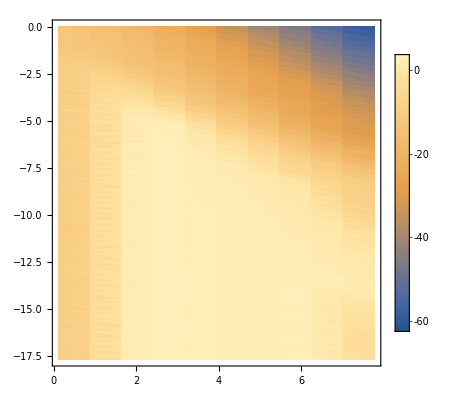

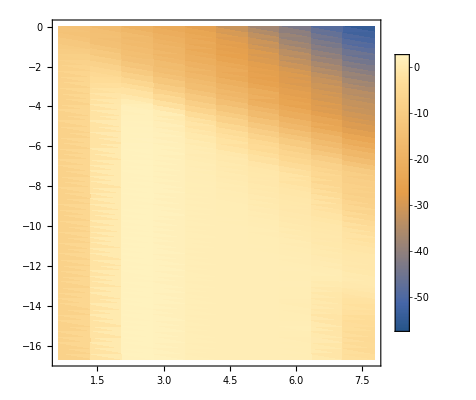

```mathematica
(*ListDensityPlot[Flatten[Table[{("dσf"/.ElectronicσDicts[[10,2]])["Grid"][[i,j,1]],("dσf"/.ElectronicσDicts[[10,2]])["Grid"][[i,j,2]],("dσf"/.ElectronicσDicts[[10,2]])["ValuesOnGrid"][[i,j]]},{i,Dimensions[("dσf"/.ElectronicσDicts[[10,2]])["Grid"]][[1]]},{j,Dimensions[("dσf"/.ElectronicσDicts[[10,2]])["Grid"]][[2]]}],1],PlotLegends->Automatic]*)
ListDensityPlot[Flatten[Table[{("dσf"/.ElectronicσDicts[[#,2]])["Grid"][[i,j,1]],("dσf"/.ElectronicσDicts[[#,2]])["Grid"][[i,j,2]],("dσf"/.ElectronicσDicts[[#,2]])["ValuesOnGrid"][[i,j]]},{i,Dimensions[("dσf"/.ElectronicσDicts[[#,2]])["Grid"]][[1]]},{j,Dimensions[("dσf"/.ElectronicσDicts[[#,2]])["Grid"]][[2]]}],1],PlotLegends->Automatic,PlotRange->All]&;
%[10]
%%[9]
```

#### Cross-section and EL Plots - post stabilization fix

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicts,10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("σf"/.ElectronicσDicts[[eind,2]])["Grid"]
("σf"/.ElectronicσDicts[[eind,2]])["ValuesOnGrid"]
```

{{4.62242},{4.938},{5.25357},{5.56914},{5.88471},{6.20029},{6.51586},{6.83143},{7.14701},{7.46258},{7.77815}}

{-22.5543,-22.1663,-22.047,-21.9067,-21.5759,-21.1289,-21.3743,-21.9002,-22.7933,-24.3346,-26.1408}

{{4.62242,7.77815}}

{{4.12242,7.77815}}

{{3.62242,7.77815}}

{{3.12242,7.77815}}

{{2.62242,7.77815}}

{{2.12242,7.77815}}

{{1.62242,7.77815}}

{{1.12242,7.77815}}

{{0.622422,7.77815}}

{{0.122422,7.77815}}

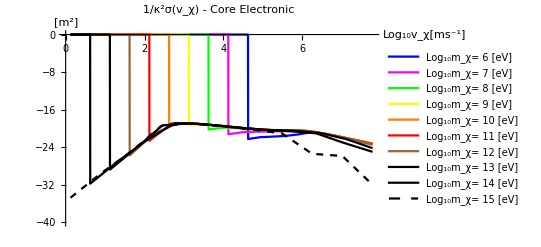

```mathematica
Quiet@Plot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("σf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print@Dom;
HeavisideTheta[vχ-Dom[[1,1]]]("σf"/.ElectronicσDicts[[eind,2]])[vχ]
,{m,6,15}]],{vχ,Dom[[1,1]],Dom[[1,2]]},AxesLabel->{"Log_10v_χ[ms^-1]","[m^2]"},PlotLabel->"1/κ^2σ(v_χ) - Core Electronic",PlotStyle->plotstyle,PlotRange->{-40,0},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

{{{4.62242,7.77815}},1}

{{{4.12242,7.77815}},2}

{{{3.62242,7.77815}},3}

{{{3.12242,7.77815}},4}

{{{2.62242,7.77815}},5}

{{{2.12242,7.77815}},6}

{{{1.62242,7.77815}},7}

{{{1.12242,7.77815}},8}

{{{0.622422,7.77815}},9}

{{{0.122422,7.77815}},10}

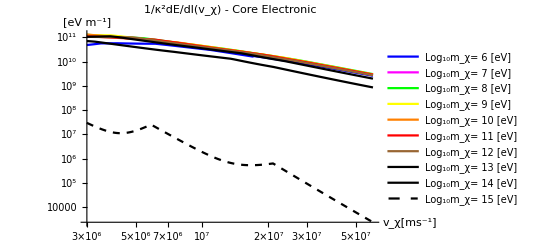

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("σf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print@{Dom,eind};
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic",PlotStyle->plotstyle,PlotRange->All,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

```mathematica
"vF"/.FeTotalparams
"ωi"/.FeTotalparams
```

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

{1.81874×10^16,2.47055×10^16,3.72046×10^16,1.00647×10^17,1.14999×10^18,1.12908×10^19}

```mathematica
?ωmaxofvχ
```

```mathematica
Log10@(ωmaxofvχ[vχ,"mχ"/.ElectronicσDicts[[eind,1]],"params"/.ElectronicσDicts[[eind,1]]]-("ωedgei"/.("params"/.ElectronicσDicts[[eind,1]])))("dσf"/.ElectronicσDicts[[eind,1]])[vχ,ξ]/.vχ->10
```

1/Log[10]Log[-6.04519×10^14+8.43602×10^12 vχ^2] InterpolatingFunction[…][vχ,ξ]

```mathematica
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dσf"/.ElectronicσDicts[[eind,1]])["Domain"];
Print[Dom];
DensityPlot[Log10@(ωmaxofvχ[10^vχ,"mχ"/.ElectronicσDicts[[eind,1]],"params"/.ElectronicσDicts[[eind,1]]]-("ωedgei"/.("params"/.ElectronicσDicts[[eind,1]])))+("dσf"/.ElectronicσDicts[[eind,1]])[vχ,ξ],{vχ,Dom[[1,1]],Dom[[1,2]]},{ξ,(*Dom[[2,1]]*)-6,Dom[[2,2]]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

{{5.60373,7.77815},{-6.70102,-0.00436489}}

{{5.10373,7.77815},{-7.70103,-0.00436481}}

{{4.60373,7.77815},{-8.70103,-0.00436481}}

{{4.10373,7.77815},{-9.70103,-0.00436481}}

{{3.60373,7.77815},{-10.701,-0.00436481}}

{{3.10373,7.77815},{-11.701,-0.00436481}}

{{2.60373,7.77815},{-12.701,-0.00436481}}

{{2.10373,7.77815},{-13.701,-0.00436481}}

{{1.60373,7.77815},{-14.701,-0.00436481}}

{{1.10373,7.77815},{-15.701,-0.00436481}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*("dσf"/.ElectronicσDicts[[1,2]])["Grid"]*)
(*(("JpereV")^-1/.Constants`SIConstRepl)10^*)(*("dσf"/.ElectronicσDicts[[1,2]])["ValuesOnGrid"]*)
("dσf"/.ElectronicσDicts[[10,2]])["Grid"]
(*(("JpereV")^-1/.Constants`SIConstRepl)10^*)("dσf"/.ElectronicσDicts[[10,2]])["ValuesOnGrid"]
```

{{{0.122422,-17.6636},{0.122422,-17.3693},{0.122422,-17.075},{0.122422,-16.7807},{0.122422,-16.4864},{0.122422,-16.192},{0.122422,-15.8977},{0.122422,-15.6034},{0.122422,-15.3091},{0.122422,-15.0147},{0.122422,-14.7204},{0.122422,-14.4261},{0.122422,-14.1318},{0.122422,-13.8375},{0.122422,-13.5431},{0.122422,-13.2488},{0.122422,-12.9545},{0.122422,-12.6602},{0.122422,-12.3659},{0.122422,-12.0715},{0.122422,-11.7772},{0.122422,-11.4829},{0.122422,-11.1886},{0.122422,-10.8943},{0.122422,-10.5999},{0.122422,-10.3056},{0.122422,-10.0113},{0.122422,-9.71697},{0.122422,-9.42265},{0.122422,-9.12832},{0.122422,-8.834},{0.122422,-8.53968},{0.122422,-8.24536},{0.122422,-7.95104},{0.122422,-7.65672},{0.122422,-7.3624},{0.122422,-7.06808},{0.122422,-6.77375},{0.122422,-6.47943},{0.122422,-6.18511},{0.122422,-5.89079},{0.122422,-5.59647},{0.122422,-5.30215},{0.122422,-5.00783},{0.122422,-4.7135},{0.122422,-4.41918},{0.122422,-4.12486},{0.122422,-3.83054},{0.122422,-3.53622},{0.122422,-3.2419},{0.122422,-2.94758},{0.122422,-2.65326},{0.122422,-2.35893},{0.122422,-2.06461},{0.122422,-1.77029},{0.122422,-1.47597},{0.122422,-1.18165},{0.122422,-0.887329},{0.122422,-0.593007},{0.122422,-0.298686},{0.122422,-0.00436481}},{{0.887995,-17.6636},{0.887995,-17.3693},{0.887995,-17.075},{0.887995,-16.7807},{0.887995,-16.4864},{0.887995,-16.192},{0.887995,-15.8977},{0.887995,-15.6034},{0.887995,-15.3091},{0.887995,-15.0147},{0.887995,-14.7204},{0.887995,-14.4261},{0.887995,-14.1318},{0.887995,-13.8375},{0.887995,-13.5431},{0.887995,-13.2488},{0.887995,-12.9545},{0.887995,-12.6602},{0.887995,-12.3659},{0.887995,-12.0715},{0.887995,-11.7772},{0.887995,-11.4829},{0.887995,-11.1886},{0.887995,-10.8943},{0.887995,-10.5999},{0.887995,-10.3056},{0.887995,-10.0113},{0.887995,-9.71697},{0.887995,-9.42265},{0.887995,-9.12832},{0.887995,-8.834},{0.887995,-8.53968},{0.887995,-8.24536},{0.887995,-7.95104},{0.887995,-7.65672},{0.887995,-7.3624},{0.887995,-7.06808},{0.887995,-6.77375},{0.887995,-6.47943},{0.887995,-6.18511},{0.887995,-5.89079},{0.887995,-5.59647},{0.887995,-5.30215},{0.887995,-5.00783},{0.887995,-4.7135},{0.887995,-4.41918},{0.887995,-4.12486},{0.887995,-3.83054},{0.887995,-3.53622},{0.887995,-3.2419},{0.887995,-2.94758},{0.887995,-2.65326},{0.887995,-2.35893},{0.887995,-2.06461},{0.887995,-1.77029},{0.887995,-1.47597},{0.887995,-1.18165},{0.887995,-0.887329},{0.887995,-0.593007},{0.887995,-0.298686},{0.887995,-0.00436481}},{{1.65357,-17.6636},{1.65357,-17.3693},{1.65357,-17.075},{1.65357,-16.7807},{1.65357,-16.4864},{1.65357,-16.192},{1.65357,-15.8977},{1.65357,-15.6034},{1.65357,-15.3091},{1.65357,-15.0147},{1.65357,-14.7204},{1.65357,-14.4261},{1.65357,-14.1318},{1.65357,-13.8375},{1.65357,-13.5431},{1.65357,-13.2488},{1.65357,-12.9545},{1.65357,-12.6602},{1.65357,-12.3659},{1.65357,-12.0715},{1.65357,-11.7772},{1.65357,-11.4829},{1.65357,-11.1886},{1.65357,-10.8943},{1.65357,-10.5999},{1.65357,-10.3056},{1.65357,-10.0113},{1.65357,-9.71697},{1.65357,-9.42265},{1.65357,-9.12832},{1.65357,-8.834},{1.65357,-8.53968},{1.65357,-8.24536},{1.65357,-7.95104},{1.65357,-7.65672},{1.65357,-7.3624},{1.65357,-7.06808},{1.65357,-6.77375},{1.65357,-6.47943},{1.65357,-6.18511},{1.65357,-5.89079},{1.65357,-5.59647},{1.65357,-5.30215},{1.65357,-5.00783},{1.65357,-4.7135},{1.65357,-4.41918},{1.65357,-4.12486},{1.65357,-3.83054},{1.65357,-3.53622},{1.65357,-3.2419},{1.65357,-2.94758},{1.65357,-2.65326},{1.65357,-2.35893},{1.65357,-2.06461},{1.65357,-1.77029},{1.65357,-1.47597},{1.65357,-1.18165},{1.65357,-0.887329},{1.65357,-0.593007},{1.65357,-0.298686},{1.65357,-0.00436481}},{{2.41914,-17.6636},{2.41914,-17.3693},{2.41914,-17.075},{2.41914,-16.7807},{2.41914,-16.4864},{2.41914,-16.192},{2.41914,-15.8977},{2.41914,-15.6034},{2.41914,-15.3091},{2.41914,-15.0147},{2.41914,-14.7204},{2.41914,-14.4261},{2.41914,-14.1318},{2.41914,-13.8375},{2.41914,-13.5431},{2.41914,-13.2488},{2.41914,-12.9545},{2.41914,-12.6602},{2.41914,-12.3659},{2.41914,-12.0715},{2.41914,-11.7772},{2.41914,-11.4829},{2.41914,-11.1886},{2.41914,-10.8943},{2.41914,-10.5999},{2.41914,-10.3056},{2.41914,-10.0113},{2.41914,-9.71697},{2.41914,-9.42265},{2.41914,-9.12832},{2.41914,-8.834},{2.41914,-8.53968},{2.41914,-8.24536},{2.41914,-7.95104},{2.41914,-7.65672},{2.41914,-7.3624},{2.41914,-7.06808},{2.41914,-6.77375},{2.41914,-6.47943},{2.41914,-6.18511},{2.41914,-5.89079},{2.41914,-5.59647},{2.41914,-5.30215},{2.41914,-5.00783},{2.41914,-4.7135},{2.41914,-4.41918},{2.41914,-4.12486},{2.41914,-3.83054},{2.41914,-3.53622},{2.41914,-3.2419},{2.41914,-2.94758},{2.41914,-2.65326},{2.41914,-2.35893},{2.41914,-2.06461},{2.41914,-1.77029},{2.41914,-1.47597},{2.41914,-1.18165},{2.41914,-0.887329},{2.41914,-0.593007},{2.41914,-0.298686},{2.41914,-0.00436481}},{{3.18471,-17.6636},{3.18471,-17.3693},{3.18471,-17.075},{3.18471,-16.7807},{3.18471,-16.4864},{3.18471,-16.192},{3.18471,-15.8977},{3.18471,-15.6034},{3.18471,-15.3091},{3.18471,-15.0147},{3.18471,-14.7204},{3.18471,-14.4261},{3.18471,-14.1318},{3.18471,-13.8375},{3.18471,-13.5431},{3.18471,-13.2488},{3.18471,-12.9545},{3.18471,-12.6602},{3.18471,-12.3659},{3.18471,-12.0715},{3.18471,-11.7772},{3.18471,-11.4829},{3.18471,-11.1886},{3.18471,-10.8943},{3.18471,-10.5999},{3.18471,-10.3056},{3.18471,-10.0113},{3.18471,-9.71697},{3.18471,-9.42265},{3.18471,-9.12832},{3.18471,-8.834},{3.18471,-8.53968},{3.18471,-8.24536},{3.18471,-7.95104},{3.18471,-7.65672},{3.18471,-7.3624},{3.18471,-7.06808},{3.18471,-6.77375},{3.18471,-6.47943},{3.18471,-6.18511},{3.18471,-5.89079},{3.18471,-5.59647},{3.18471,-5.30215},{3.18471,-5.00783},{3.18471,-4.7135},{3.18471,-4.41918},{3.18471,-4.12486},{3.18471,-3.83054},{3.18471,-3.53622},{3.18471,-3.2419},{3.18471,-2.94758},{3.18471,-2.65326},{3.18471,-2.35893},{3.18471,-2.06461},{3.18471,-1.77029},{3.18471,-1.47597},{3.18471,-1.18165},{3.18471,-0.887329},{3.18471,-0.593007},{3.18471,-0.298686},{3.18471,-0.00436481}},{{3.95029,-17.6636},{3.95029,-17.3693},{3.95029,-17.075},{3.95029,-16.7807},{3.95029,-16.4864},{3.95029,-16.192},{3.95029,-15.8977},{3.95029,-15.6034},{3.95029,-15.3091},{3.95029,-15.0147},{3.95029,-14.7204},{3.95029,-14.4261},{3.95029,-14.1318},{3.95029,-13.8375},{3.95029,-13.5431},{3.95029,-13.2488},{3.95029,-12.9545},{3.95029,-12.6602},{3.95029,-12.3659},{3.95029,-12.0715},{3.95029,-11.7772},{3.95029,-11.4829},{3.95029,-11.1886},{3.95029,-10.8943},{3.95029,-10.5999},{3.95029,-10.3056},{3.95029,-10.0113},{3.95029,-9.71697},{3.95029,-9.42265},{3.95029,-9.12832},{3.95029,-8.834},{3.95029,-8.53968},{3.95029,-8.24536},{3.95029,-7.95104},{3.95029,-7.65672},{3.95029,-7.3624},{3.95029,-7.06808},{3.95029,-6.77375},{3.95029,-6.47943},{3.95029,-6.18511},{3.95029,-5.89079},{3.95029,-5.59647},{3.95029,-5.30215},{3.95029,-5.00783},{3.95029,-4.7135},{3.95029,-4.41918},{3.95029,-4.12486},{3.95029,-3.83054},{3.95029,-3.53622},{3.95029,-3.2419},{3.95029,-2.94758},{3.95029,-2.65326},{3.95029,-2.35893},{3.95029,-2.06461},{3.95029,-1.77029},{3.95029,-1.47597},{3.95029,-1.18165},{3.95029,-0.887329},{3.95029,-0.593007},{3.95029,-0.298686},{3.95029,-0.00436481}},{{4.71586,-17.6636},{4.71586,-17.3693},{4.71586,-17.075},{4.71586,-16.7807},{4.71586,-16.4864},{4.71586,-16.192},{4.71586,-15.8977},{4.71586,-15.6034},{4.71586,-15.3091},{4.71586,-15.0147},{4.71586,-14.7204},{4.71586,-14.4261},{4.71586,-14.1318},{4.71586,-13.8375},{4.71586,-13.5431},{4.71586,-13.2488},{4.71586,-12.9545},{4.71586,-12.6602},{4.71586,-12.3659},{4.71586,-12.0715},{4.71586,-11.7772},{4.71586,-11.4829},{4.71586,-11.1886},{4.71586,-10.8943},{4.71586,-10.5999},{4.71586,-10.3056},{4.71586,-10.0113},{4.71586,-9.71697},{4.71586,-9.42265},{4.71586,-9.12832},{4.71586,-8.834},{4.71586,-8.53968},{4.71586,-8.24536},{4.71586,-7.95104},{4.71586,-7.65672},{4.71586,-7.3624},{4.71586,-7.06808},{4.71586,-6.77375},{4.71586,-6.47943},{4.71586,-6.18511},{4.71586,-5.89079},{4.71586,-5.59647},{4.71586,-5.30215},{4.71586,-5.00783},{4.71586,-4.7135},{4.71586,-4.41918},{4.71586,-4.12486},{4.71586,-3.83054},{4.71586,-3.53622},{4.71586,-3.2419},{4.71586,-2.94758},{4.71586,-2.65326},{4.71586,-2.35893},{4.71586,-2.06461},{4.71586,-1.77029},{4.71586,-1.47597},{4.71586,-1.18165},{4.71586,-0.887329},{4.71586,-0.593007},{4.71586,-0.298686},{4.71586,-0.00436481}},{{5.48143,-17.6636},{5.48143,-17.3693},{5.48143,-17.075},{5.48143,-16.7807},{5.48143,-16.4864},{5.48143,-16.192},{5.48143,-15.8977},{5.48143,-15.6034},{5.48143,-15.3091},{5.48143,-15.0147},{5.48143,-14.7204},{5.48143,-14.4261},{5.48143,-14.1318},{5.48143,-13.8375},{5.48143,-13.5431},{5.48143,-13.2488},{5.48143,-12.9545},{5.48143,-12.6602},{5.48143,-12.3659},{5.48143,-12.0715},{5.48143,-11.7772},{5.48143,-11.4829},{5.48143,-11.1886},{5.48143,-10.8943},{5.48143,-10.5999},{5.48143,-10.3056},{5.48143,-10.0113},{5.48143,-9.71697},{5.48143,-9.42265},{5.48143,-9.12832},{5.48143,-8.834},{5.48143,-8.53968},{5.48143,-8.24536},{5.48143,-7.95104},{5.48143,-7.65672},{5.48143,-7.3624},{5.48143,-7.06808},{5.48143,-6.77375},{5.48143,-6.47943},{5.48143,-6.18511},{5.48143,-5.89079},{5.48143,-5.59647},{5.48143,-5.30215},{5.48143,-5.00783},{5.48143,-4.7135},{5.48143,-4.41918},{5.48143,-4.12486},{5.48143,-3.83054},{5.48143,-3.53622},{5.48143,-3.2419},{5.48143,-2.94758},{5.48143,-2.65326},{5.48143,-2.35893},{5.48143,-2.06461},{5.48143,-1.77029},{5.48143,-1.47597},{5.48143,-1.18165},{5.48143,-0.887329},{5.48143,-0.593007},{5.48143,-0.298686},{5.48143,-0.00436481}},{{6.24701,-17.6636},{6.24701,-17.3693},{6.24701,-17.075},{6.24701,-16.7807},{6.24701,-16.4864},{6.24701,-16.192},{6.24701,-15.8977},{6.24701,-15.6034},{6.24701,-15.3091},{6.24701,-15.0147},{6.24701,-14.7204},{6.24701,-14.4261},{6.24701,-14.1318},{6.24701,-13.8375},{6.24701,-13.5431},{6.24701,-13.2488},{6.24701,-12.9545},{6.24701,-12.6602},{6.24701,-12.3659},{6.24701,-12.0715},{6.24701,-11.7772},{6.24701,-11.4829},{6.24701,-11.1886},{6.24701,-10.8943},{6.24701,-10.5999},{6.24701,-10.3056},{6.24701,-10.0113},{6.24701,-9.71697},{6.24701,-9.42265},{6.24701,-9.12832},{6.24701,-8.834},{6.24701,-8.53968},{6.24701,-8.24536},{6.24701,-7.95104},{6.24701,-7.65672},{6.24701,-7.3624},{6.24701,-7.06808},{6.24701,-6.77375},{6.24701,-6.47943},{6.24701,-6.18511},{6.24701,-5.89079},{6.24701,-5.59647},{6.24701,-5.30215},{6.24701,-5.00783},{6.24701,-4.7135},{6.24701,-4.41918},{6.24701,-4.12486},{6.24701,-3.83054},{6.24701,-3.53622},{6.24701,-3.2419},{6.24701,-2.94758},{6.24701,-2.65326},{6.24701,-2.35893},{6.24701,-2.06461},{6.24701,-1.77029},{6.24701,-1.47597},{6.24701,-1.18165},{6.24701,-0.887329},{6.24701,-0.593007},{6.24701,-0.298686},{6.24701,-0.00436481}},{{7.01258,-17.6636},{7.01258,-17.3693},{7.01258,-17.075},{7.01258,-16.7807},{7.01258,-16.4864},{7.01258,-16.192},{7.01258,-15.8977},{7.01258,-15.6034},{7.01258,-15.3091},{7.01258,-15.0147},{7.01258,-14.7204},{7.01258,-14.4261},{7.01258,-14.1318},{7.01258,-13.8375},{7.01258,-13.5431},{7.01258,-13.2488},{7.01258,-12.9545},{7.01258,-12.6602},{7.01258,-12.3659},{7.01258,-12.0715},{7.01258,-11.7772},{7.01258,-11.4829},{7.01258,-11.1886},{7.01258,-10.8943},{7.01258,-10.5999},{7.01258,-10.3056},{7.01258,-10.0113},{7.01258,-9.71697},{7.01258,-9.42265},{7.01258,-9.12832},{7.01258,-8.834},{7.01258,-8.53968},{7.01258,-8.24536},{7.01258,-7.95104},{7.01258,-7.65672},{7.01258,-7.3624},{7.01258,-7.06808},{7.01258,-6.77375},{7.01258,-6.47943},{7.01258,-6.18511},{7.01258,-5.89079},{7.01258,-5.59647},{7.01258,-5.30215},{7.01258,-5.00783},{7.01258,-4.7135},{7.01258,-4.41918},{7.01258,-4.12486},{7.01258,-3.83054},{7.01258,-3.53622},{7.01258,-3.2419},{7.01258,-2.94758},{7.01258,-2.65326},{7.01258,-2.35893},{7.01258,-2.06461},{7.01258,-1.77029},{7.01258,-1.47597},{7.01258,-1.18165},{7.01258,-0.887329},{7.01258,-0.593007},{7.01258,-0.298686},{7.01258,-0.00436481}},{{7.77815,-17.6636},{7.77815,-17.3693},{7.77815,-17.075},{7.77815,-16.7807},{7.77815,-16.4864},{7.77815,-16.192},{7.77815,-15.8977},{7.77815,-15.6034},{7.77815,-15.3091},{7.77815,-15.0147},{7.77815,-14.7204},{7.77815,-14.4261},{7.77815,-14.1318},{7.77815,-13.8375},{7.77815,-13.5431},{7.77815,-13.2488},{7.77815,-12.9545},{7.77815,-12.6602},{7.77815,-12.3659},{7.77815,-12.0715},{7.77815,-11.7772},{7.77815,-11.4829},{7.77815,-11.1886},{7.77815,-10.8943},{7.77815,-10.5999},{7.77815,-10.3056},{7.77815,-10.0113},{7.77815,-9.71697},{7.77815,-9.42265},{7.77815,-9.12832},{7.77815,-8.834},{7.77815,-8.53968},{7.77815,-8.24536},{7.77815,-7.95104},{7.77815,-7.65672},{7.77815,-7.3624},{7.77815,-7.06808},{7.77815,-6.77375},{7.77815,-6.47943},{7.77815,-6.18511},{7.77815,-5.89079},{7.77815,-5.59647},{7.77815,-5.30215},{7.77815,-5.00783},{7.77815,-4.7135},{7.77815,-4.41918},{7.77815,-4.12486},{7.77815,-3.83054},{7.77815,-3.53622},{7.77815,-3.2419},{7.77815,-2.94758},{7.77815,-2.65326},{7.77815,-2.35893},{7.77815,-2.06461},{7.77815,-1.77029},{7.77815,-1.47597},{7.77815,-1.18165},{7.77815,-0.887329},{7.77815,-0.593007},{7.77815,-0.298686},{7.77815,-0.00436481}}}

{{-11.2658,-11.2658,-11.2658,-11.2658,-11.2658,-11.2658,-11.2658,-11.555,-11.555,-11.0592,-12.2187,-11.4572,-11.9217,-11.3186,-11.4462,-12.5608,-11.0641,-11.4013,-11.8757,-11.5152,-11.4669,-11.8036,-11.3863,-12.552,-12.1224,-11.862,-11.1817,-11.6245,-11.924,-11.7198,-11.3512,-11.12,-11.7147,-11.3125,-11.4538,-11.8475,-11.4838,-11.4176,-11.4587,-11.0149,-11.3809,-11.4317,-11.9297,-11.4841,-11.8897,-10.9257,-11.6528,-11.526,-12.1449,-12.2519,-11.0888,-12.6558,-11.4714,-11.1984,-11.9281,-12.2743,-11.5411,-12.7573,-12.1277,-11.6995,-13.2433},{-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62692,-6.62694,-6.62693,-6.62694,-6.62692,-6.62693,-6.62694,-6.62694,-6.62692,-6.62693,-6.62694,-6.62692,-6.62694,-6.62692,-6.62692,-6.62692,-6.62693,-6.62693,-6.62692,-6.62694,-6.62693,-6.62693,-6.62694,-6.62693,-6.62693,-6.62692,-6.62694,-6.62694,-6.62696,-6.62697,-6.62699,-6.62703,-6.62712,-6.62732,-6.62768,-6.62842,-6.62983,-6.63266,-6.63822,-6.64911,-6.67047,-6.71222,-6.79316,-6.94789,-7.23125,-7.74294,-8.59039,-9.86453,-11.5524,-12.6595,-13.1545,-13.3398,-15.3458,-15.019},{-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.456489,-0.45649,-0.45649,-0.456491,-0.456493,-0.456497,-0.456504,-0.456519,-0.456548,-0.456605,-0.456717,-0.456937,-0.457371,-0.458226,-0.459909,-0.463222,-0.469737,-0.482535,-0.507616,-0.556535,-0.651095,-0.826403,-1.15719,-1.73591,-2.67178,-4.03832,-5.82613,-7.94887,-10.2905,-13.0055,-15.1005,-14.2528,-14.8785,-14.9177,-15.2502,-15.7566,-17.1908},{3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29833,3.29832,3.29832,3.29831,3.29829,3.29826,3.29819,3.29805,3.29779,3.29726,3.29623,3.2942,3.29021,3.28233,3.26683,3.23627,3.18019,3.05601,2.42673,3.60157,1.91117,-0.0511733,-2.26439,-4.65266,-7.14159,-9.67235,-12.1996,-14.1125,-14.3614,-15.0843,-15.5709,-16.4347,-17.5416,-18.6334,-19.224,-19.7812,-20.3185},{2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10574,2.10573,2.10573,2.10572,2.10571,2.10568,2.10563,2.10552,2.10532,2.10491,2.10411,2.10255,2.09949,2.09353,2.08211,2.06516,2.02677,1.96071,1.85113,1.66221,1.30574,1.46694,1.12507,-1.48855,-4.04973,-6.57605,-9.04447,-11.4518,-13.7117,-15.2303,-15.1323,-16.0607,-17.5572,-18.3047,-20.3829,-20.9144,-21.8274,-22.2887,-22.3281,-25.2438,-25.6562},{2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05755,2.05754,2.05753,2.05752,2.05748,2.05741,2.05727,2.05699,2.05645,2.05538,2.05329,2.04919,2.04125,2.02601,2.00213,1.95168,1.86753,1.74079,1.57296,1.37977,1.17293,0.896587,0.392226,-0.951664,-2.30507,-3.39253,-5.79618,-8.15088,-10.5047,-12.8613,-15.9133,-16.5875,-17.4469,-18.5486,-19.8441,-20.5359,-21.7328,-23.1623,-24.0234,-24.6666,-24.8139,-26.3781,-27.7343,-29.3226,-31.8118},{2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05543,2.05542,2.05542,2.05542,2.05541,2.0554,2.05538,2.05534,2.05526,2.0551,2.05478,2.05415,2.05291,2.05049,2.04576,2.03659,2.02341,1.99117,1.93398,1.83974,1.69919,1.51208,1.28859,1.04584,0.806483,0.596416,0.404264,0.109156,-1.1428,-2.85863,-3.89088,-4.8483,-7.20817,-9.56391,-11.9186,-14.2787,-16.209,-16.8214,-18.0965,-20.8163,-22.9587,-23.5295,-23.8428,-24.6987,-25.176,-26.446,-27.9171,-28.8256,-30.5031,-32.2477,-33.8396,-35.4498,-37.9388},{2.05538,2.05547,2.05538,2.05538,2.05536,2.05537,2.05537,2.05542,2.05531,2.05536,2.05532,2.05523,2.05499,2.05463,2.05391,2.05253,2.04968,2.04426,2.03386,2.01832,1.98192,1.91818,1.81503,1.66451,1.46834,1.23751,0.987073,0.73269,0.49205,0.290563,0.165406,0.134924,0.0889786,-0.304721,-3.12558,-4.33554,-5.31955,-6.26642,-8.62396,-10.9793,-13.3339,-15.6609,-18.0939,-18.3607,-22.0256,-23.8074,-23.7842,-24.8888,-26.5939,-26.9624,-27.4178,-28.5572,-29.7461,-31.2822,-32.9563,-34.8529,-36.6344,-38.3665,-39.9639,-41.5743,-44.0634},{2.83597,1.84024,2.09934,2.0991,2.09861,1.83922,2.09571,2.09199,2.08161,2.07917,2.38238,2.24181,2.17667,2.14835,1.84477,2.01187,1.90483,1.76775,1.62634,1.42382,1.18782,0.935032,0.680884,0.442265,0.241411,0.1084,0.0733896,0.161335,0.137013,-0.477783,-1.24074,-1.62754,-2.91327,-7.06994,-6.71329,-7.67642,-10.038,-12.3943,-14.75,-17.1277,-18.7736,-21.7831,-24.0072,-24.9445,-26.8974,-27.2075,-27.7298,-28.9608,-29.4648,-29.4786,-32.0507,-33.9063,-35.6517,-37.4283,-39.2006,-40.9784,-42.759,-44.4911,-46.0885,-47.6989,-50.188},{-1.14059,-1.14065,-1.14079,-1.14103,-1.72546,-1.40498,-1.40394,-1.40188,-1.2452,-1.35463,-0.915341,-0.492464,-0.31372,1.05676,2.13505,1.12493,0.883212,0.630283,0.397459,0.207232,0.0902953,0.068571,0.26287,-0.00612555,-0.776486,-1.78672,-2.91035,-4.07171,-5.24065,-6.40217,-7.51669,-8.32923,-7.50806,-8.97533,-11.4251,-13.8026,-16.1606,-18.4794,-19.5966,-23.2275,-25.5616,-27.894,-28.6374,-28.9023,-30.1646,-30.9849,-32.1184,-32.5161,-34.7501,-36.4783,-38.2491,-40.016,-41.7837,-43.5528,-45.3251,-47.103,-48.8836,-50.6157,-52.2131,-53.8235,-56.3126},{-4.26213,-5.36025,-5.28394,-5.36034,-5.27964,-4.25585,-3.60204,-3.61442,-3.48584,-1.70421,-1.16433,0.0939512,0.944379,0.348758,0.176905,0.0773935,0.0826083,0.273795,-0.136442,-0.968951,-2.01183,-3.14787,-4.31396,-5.48827,-6.66477,-7.84178,-9.01876,-10.1951,-9.94915,-9.69234,-9.38924,-10.2243,-12.235,-15.101,-17.5514,-19.7623,-22.2875,-24.6434,-26.9909,-29.2223,-30.102,-31.8126,-32.9861,-33.122,-33.9466,-35.5808,-37.1353,-39.0748,-40.8416,-42.6075,-44.3739,-46.1407,-47.9082,-49.6774,-51.4497,-53.2276,-55.0081,-56.7403,-58.3376,-59.9481,-62.4371}}

```mathematica
Dimensions[("dσf"/.ElectronicσDicts[[10,2]])["Grid"]][[2]]
```

61

```mathematica
(*ListDensityPlot[Flatten[Table[{("dσf"/.ElectronicσDicts[[10,2]])["Grid"][[i,j,1]],("dσf"/.ElectronicσDicts[[10,2]])["Grid"][[i,j,2]],("dσf"/.ElectronicσDicts[[10,2]])["ValuesOnGrid"][[i,j]]},{i,Dimensions[("dσf"/.ElectronicσDicts[[10,2]])["Grid"]][[1]]},{j,Dimensions[("dσf"/.ElectronicσDicts[[10,2]])["Grid"]][[2]]}],1],PlotLegends->Automatic]*)
ListDensityPlot[Flatten[Table[{("dσf"/.ElectronicσDicts[[#,2]])["Grid"][[i,j,1]],("dσf"/.ElectronicσDicts[[#,2]])["Grid"][[i,j,2]],("dσf"/.ElectronicσDicts[[#,2]])["ValuesOnGrid"][[i,j]]},{i,Dimensions[("dσf"/.ElectronicσDicts[[#,2]])["Grid"]][[1]]},{j,Dimensions[("dσf"/.ElectronicσDicts[[#,2]])["Grid"]][[2]]}],1],PlotLegends->Automatic,PlotRange->All]&;
%[10]
%%[9]
```

-Graphics-

-Graphics-

### Mass independence

#### limits of momenta bounds

```mathematica
zb["-",ω,mχ,vχ,{}]
Series[%,{mχ,∞,1}]//PowerExpand
```

(mχ vχ-√2 √(mχ ((mχ vχ^2)/2-ℏ ω)))/(2 qF ℏ)

ω/(2 qF vχ)+(ℏ ω^2)/(4 qF vχ^3 mχ)+O[1/mχ]^2

```mathematica
"What is the numerical value of the lower bound?"
ω/(2 "qF" vχ)/.ω->"ωedgei"/.FeTotalparams
ω/(2 "qF" vχ)/.ω->1/(2 "ℏ")mχ vχ^2/.mχ->10^9"m"/.FeTotalparams
```

What is the numerical value of the lower bound?

{20789.3/vχ,184.735/vχ,6465.82/vχ,1669.12/vχ,(2.36271×10^6)/vχ,(5.19315×10^6)/vχ}

{148.48 vχ,121.056 vχ,92.1402 vχ,47.4585 vχ,9.35516 vχ,2.04032 vχ}

#### Run mχ->∞ limit of stopping power

```mathematica
Femχ∞dEdl = Monitor[Table[InterpolateLossFnmχto∞[FeTotalparams[[o]]],{o,Length[FeTotalparams]}],{o,v,cz}](*Table[InterpolateLossFnmχto∞[FeTotalparams[[o]]],{o,Length[FeTotalparams]}]*)
```

dEdlf interpolation done

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 4 iterated refinements in z in the region {{1.,10.}}. NIntegrate obtained 0.0815756 and 0.00105778 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 4 iterated refinements in z in the region {{1.,10.}}. NIntegrate obtained 0.0858802 and 0.0010222 for the integral and error estimates.

dEdlf interpolation done

dEdlf interpolation done

dEdlf interpolation done

«2 more identical outputs»

{<|Interpointsvχ→{1.68373,9.58211,54.5317,310.339,1766.14,10051.1,57200.5,325528.,1.85257×10^6,1.0543×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.226273,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→17.0944,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},ωmin→6.04519×10^14,regionindex→1,materialname→material|>,<|Interpointsvχ→{2.06517,11.5153,64.2088,358.025,1996.34,11131.5,62068.7,346093.,1.9298×10^6,1.07605×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.314955,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},ωmin→6.5887×10^12,regionindex→1,materialname→material|>,<|Interpointsvχ→{2.71326,14.7217,79.8772,433.4,2351.55,12759.1,69228.8,375624.,2.03807×10^6,1.10582×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.433491,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→44.3904,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},ωmin→3.02977×10^14,regionindex→1,materialname→material|>,<|Interpointsvχ→{5.26776,26.7472,135.81,689.578,3501.35,17778.2,90269.5,458346.,2.32727×10^6,1.18168×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.721626,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→167.324,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},ωmin→1.51848×10^14,regionindex→1,materialname→material|>,<|Interpointsvχ→{26.7232,115.349,497.899,2149.15,9276.7,40042.4,172841.,746058.,3.22032×10^6,1.39003×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{1.42689,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→4306.1,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},ωmin→1.09042×10^18,regionindex→1,materialname→material|>,<|Interpointsvχ→{122.53,454.185,1683.54,6240.43,23131.6,85742.6,317825.,1.17809×10^6,4.36686×10^6,1.61868×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{2.08824,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→90529.8,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19},ωmin→1.09893×10^19,regionindex→1,materialname→material|>}

```mathematica
?SaveIt
```

```mathematica
SaveIt[NotebookDirectory[]<>"Femχ∞dEdl",Femχ∞dEdl]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\analytics\Femχ∞dEdl.dat

```mathematica
Femχ∞dEdl=ReadIt[NotebookDirectory[]<>"Femχ∞dEdl"]
```

{<|Interpointsvχ→{1.68373,9.58211,54.5317,310.339,1766.14,10051.1,57200.5,325528.,1.85257×10^6,1.0543×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.226273,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→17.0944,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},ωmin→6.04519×10^14,regionindex→1,materialname→material|>,<|Interpointsvχ→{2.06517,11.5153,64.2088,358.025,1996.34,11131.5,62068.7,346093.,1.9298×10^6,1.07605×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.314955,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},ωmin→6.5887×10^12,regionindex→1,materialname→material|>,<|Interpointsvχ→{2.71326,14.7217,79.8772,433.4,2351.55,12759.1,69228.8,375624.,2.03807×10^6,1.10582×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.433491,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→44.3904,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},ωmin→3.02977×10^14,regionindex→1,materialname→material|>,<|Interpointsvχ→{5.26776,26.7472,135.81,689.578,3501.35,17778.2,90269.5,458346.,2.32727×10^6,1.18168×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.721626,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→167.324,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},ωmin→1.51848×10^14,regionindex→1,materialname→material|>,<|Interpointsvχ→{26.7232,115.349,497.899,2149.15,9276.7,40042.4,172841.,746058.,3.22032×10^6,1.39003×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{1.42689,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→4306.1,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},ωmin→1.09042×10^18,regionindex→1,materialname→material|>,<|Interpointsvχ→{122.53,454.185,1683.54,6240.43,23131.6,85742.6,317825.,1.17809×10^6,4.36686×10^6,1.61868×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{2.08824,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→90529.8,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19},ωmin→1.09893×10^19,regionindex→1,materialname→material|>}

#### mχ->∞ limit of stopping power

```mathematica
testFe2= Monitor[InterpolateLossFnmχto∞[FeTotalparams[[2]]],{v,cz,cu}]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 4 iterated refinements in z in the region {{1.,10.}}. NIntegrate obtained 0.0815756 and 0.00105777 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 4 iterated refinements in z in the region {{1.,10.}}. NIntegrate obtained 0.0858801 and 0.00102219 for the integral and error estimates.

dEdlf interpolation done

<|Interpointsvχ→{2.06517,11.5153,64.2088,358.025,1996.34,11131.5,62068.7,346093.,1.9298×10^6,1.07605×10^7,6.×10^7},integrand→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],vχ→{0.314955,Log[60000000]/Log[10]},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},ωmin→6.5887×10^12,regionindex→1,materialname→material|>

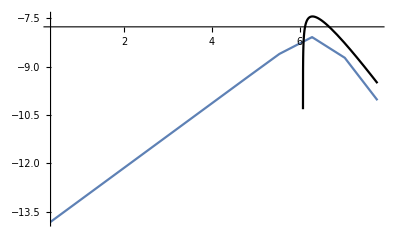

```mathematica
Show[{Plot[testFe2["dEdlf"][vχ],{vχ,testFe2["dEdlf"]["Domain"][[1,1]],testFe2["dEdlf"]["Domain"][[1,2]]},PlotRange->All],Plot[Log10[("e")^4/(4 π("ϵ0")^2"m"10^(2 vχ))"ne"Log[(2"m"10^(2 vχ))/("ℏ""ωi")]]/.FeTotalparams[[2]],{vχ,testFe2["dEdlf"]["Domain"][[1,1]],testFe2["dEdlf"]["Domain"][[1,2]]}(*,PlotRange->{{0,8},{-6,0.5}}*),PlotStyle->Black]}]
```

Note this scales linearly in v at small velocities (as predicted by Lindhard)

Also note that there is a factor of 2 discrepancy between the two expressions. Could this be related to the equipartition rule / plasmon line? I don’t think you get it from the fact that the integral extends to negative ω values.

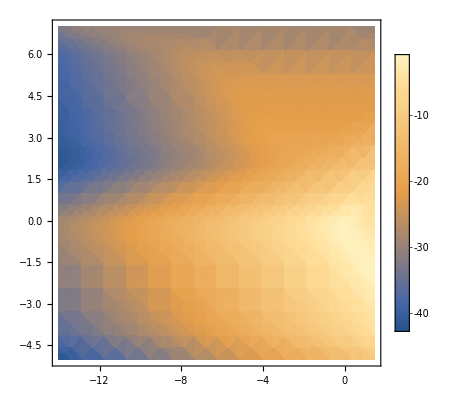

```mathematica
DensityPlot[testFe2["integrand"][u,z],{u,testFe2["integrand"]["Domain"][[1,1]],testFe2["integrand"]["Domain"][[1,2]]},{z,testFe2["integrand"]["Domain"][[2,1]],testFe2["integrand"]["Domain"][[2,2]]},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
testFe2["dEdlf"]["ValuesOnGrid"]
```

{-13.8212,-13.0748,-12.3285,-11.5822,-10.8359,-10.0896,-9.34354,-8.6044,-8.08195,-8.72413,-10.0432}

InterpolatingFunction::dmval: Input value {0.226428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

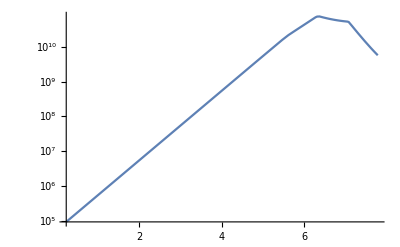

```mathematica
LogPlot[(("JpereV")^-1/.SIConstRepl)Sum["Ai"10^Femχ∞dEdl[[o]]["dEdlf"][#]/.FeTotalparams[[o]] ,{o,Length[FeTotalparams]}]&[vχ],{vχ,testFe1["dEdlf"]["Domain"][[1,1]],testFe1["dEdlf"]["Domain"][[1,2]]},PlotRange->All]
```

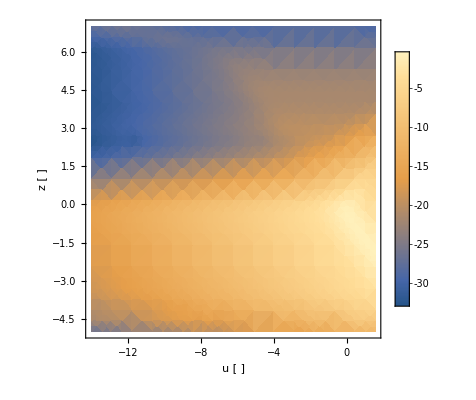

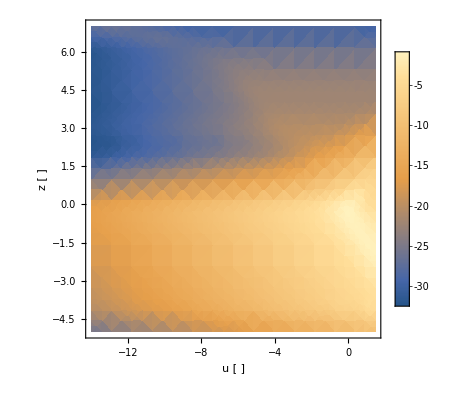

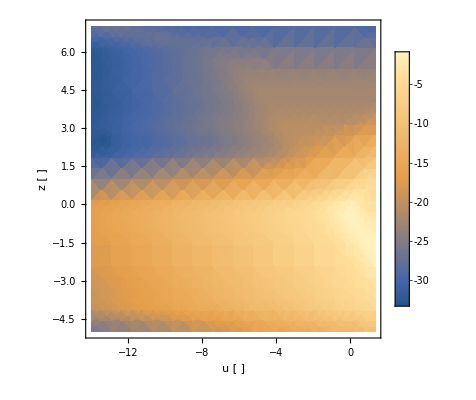

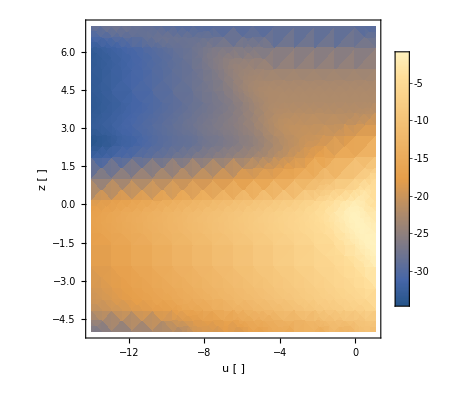

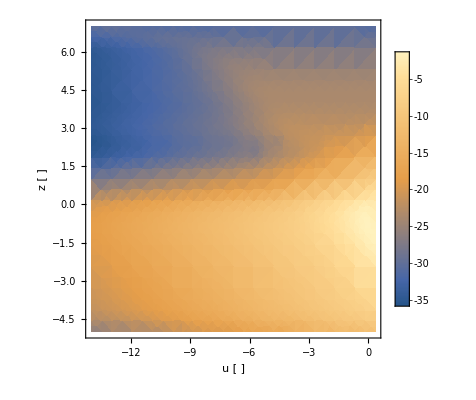

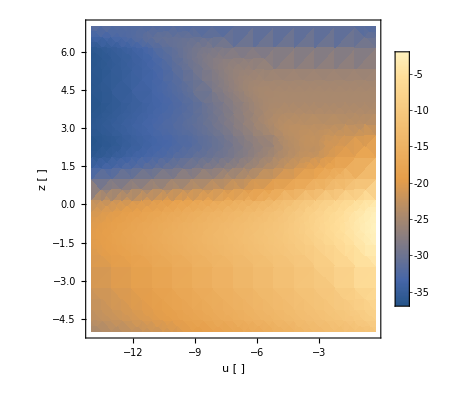

```mathematica
Do[Print@DensityPlot[Femχ∞dEdl[[i]]["integrand"][u,z],{u,Femχ∞dEdl[[i]]["integrand"]["Domain"][[1,1]],Femχ∞dEdl[[i]]["integrand"]["Domain"][[1,2]]},{z,Femχ∞dEdl[[i]]["integrand"]["Domain"][[2,1]],Femχ∞dEdl[[i]]["integrand"]["Domain"][[2,2]]},PlotRange->All,PlotLegends->Automatic,FrameLabel->{"u [ ]","z [ ]"}],{i,Length[Femχ∞dEdl]}]
```

InterpolatingFunction::dmval: Input value {0.226428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

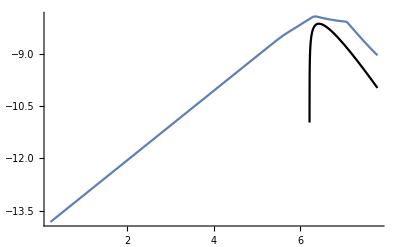

```mathematica
Show[{Plot[Log10@Sum["Ai"10^Femχ∞dEdl[[o]]["dEdlf"][#]/.FeTotalparams[[o]] ,{o,Length[FeTotalparams]}]&[vχ],{vχ,testFe1["dEdlf"]["Domain"][[1,1]],testFe1["dEdlf"]["Domain"][[1,2]]},PlotRange->All],Plot[Log10@((*"JpereV"*)dEdlBethe[10^vχ,Total@("Ai""ne"/.FeTotalparams),15,Total@(("JpereV")^-1"ℏ""Ai""ωi"/.FeTotalparams),False]/.SIConstRepl),{vχ,testFe2["dEdlf"]["Domain"][[1,1]],testFe2["dEdlf"]["Domain"][[1,2]]}(*,PlotRange->{{0,8},{-6,0.5}}*),PlotStyle->Black]}]
```

InterpolatingFunction::dmval: Input value {0.226428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

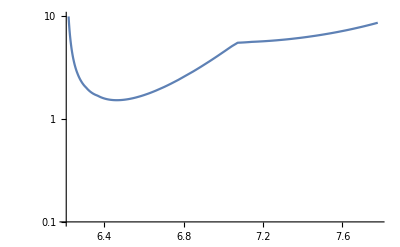

```mathematica
Show[{LogPlot[10^(Log10@Sum["Ai"10^Femχ∞dEdl[[o]]["dEdlf"][#]/.FeTotalparams[[o]] ,{o,Length[FeTotalparams]}]&[vχ]-Log10@((*"JpereV"*)dEdlBethe[10^vχ,Total@("Ai""ne"/.FeTotalparams),15,Total@(("JpereV")^-1"ℏ""Ai""ωi"/.FeTotalparams),False]/.SIConstRepl)),{vχ,testFe1["dEdlf"]["Domain"][[1,1]],testFe1["dEdlf"]["Domain"][[1,2]]},PlotRange->{0.1,10}]}]
```

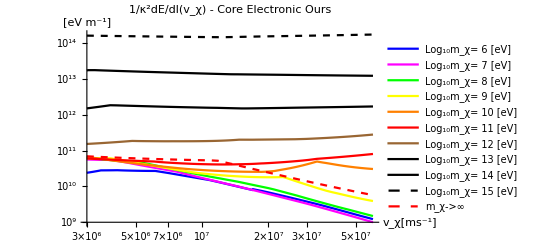

```mathematica
plotstyle= {Blue,Magenta,Green,Yellow,Orange,Red,Brown, Directive[Black, Thick],Directive[Black, Thin],Directive[Black, Dashed],Directive[Red,Dashed,Thick]};
Quiet@LogLogPlot[Evaluate[Join[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}],{(("JpereV")^-1/.Constants`SIConstRepl)Sum["Ai"10^Femχ∞dEdl[[o]]["dEdlf"][Log10@#]/.FeTotalparams[[o]] ,{o,Length[FeTotalparams]}]&[vχ]}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Join[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],{"m_χ->∞"}]]]
```

#### Compare mχ limit to interpolated plots - Post dielectric stabilization

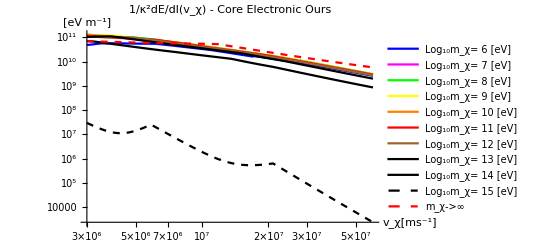

```mathematica
plotstyle= {Blue,Magenta,Green,Yellow,Orange,Red,Brown, Directive[Black, Thick],Directive[Black, Thin],Directive[Black, Dashed],Directive[Red,Dashed,Thick]};
Quiet@LogLogPlot[Evaluate[Join[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}],{(("JpereV")^-1/.Constants`SIConstRepl)Sum["Ai"10^Femχ∞dEdl[[o]]["dEdlf"][Log10@#]/.FeTotalparams[[o]] ,{o,Length[FeTotalparams]}]&[vχ]}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotRange->All,PlotLegends->LineLegend[plotstyle,Join[Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}],{"m_χ->∞"}]]]
```

```mathematica
ElectronicσDicts[[eind,2]]["dEdlf"]["ValuesOnGrid"]
ElectronicσDicts[[eind,2]]["dEdlf"]["Grid"]
Table[ElectronicσDicts[[eind,2]]["dEdlf"][%[[i,1]]],{i,Length[%]}]
```

{-26.6062,-21.4379,-16.8123,-11.3146,-10.4021,-10.3252,-10.2801,-10.3177,-13.4931,-16.6293,-19.6936}

{{0.122422},{0.887995},{1.65357},{2.41914},{3.18471},{3.95029},{4.71586},{5.48143},{6.24701},{7.01258},{7.77815}}

{-26.6062,-21.4379,-16.8123,-11.3146,-10.4021,-10.3252,-10.2801,-10.3177,-13.4931,-16.6293,-19.6936}

```mathematica
ElectronicσDicts[[eind-1,2]]["dEdlf"]["ValuesOnGrid"]
ElectronicσDicts[[eind-1,2]]["dEdlf"]["Grid"]
```

{-23.6034,-18.7355,-14.2994,-10.5648,-10.3355,-10.3057,-10.0423,-9.53724,-9.31731,-10.3255,-12.0497}

{{0.622422},{1.338},{2.05357},{2.76914},{3.48471},{4.20029},{4.91586},{5.63143},{6.34701},{7.06258},{7.77815}}

#### Compare w T enhancement

```mathematica
Femχ∞dEdlwEnhancement = Monitor[Table[InterpolateLossFnmχto∞[FeTotalparams[[o]]],{o,Length[FeTotalparams]}],{o,v,cz,cu}]
```

#### Interpolated x-secs

{{5.60373,7.77815},{-6.70102,-0.00436489}}

{{5.10373,7.77815},{-7.70103,-0.00436481}}

{{4.60373,7.77815},{-8.70103,-0.00436481}}

{{4.10373,7.77815},{-9.70103,-0.00436481}}

{{3.60373,7.77815},{-10.701,-0.00436481}}

{{3.10373,7.77815},{-11.701,-0.00436481}}

{{2.60373,7.77815},{-12.701,-0.00436481}}

{{2.10373,7.77815},{-13.701,-0.00436481}}

{{1.60373,7.77815},{-14.701,-0.00436481}}

{{1.10373,7.77815},{-15.701,-0.00436481}}

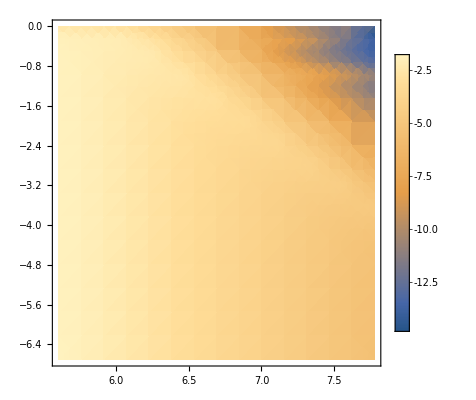
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dσf"/.ElectronicσDicts[[eind,1]])["Domain"];
Print[Dom];
DensityPlot[("dσf"/.ElectronicσDicts[[eind,1]])[vχ,ξ],{vχ,Dom[[1,1]],Dom[[1,2]]},{ξ,Dom[[2,1]],Dom[[2,2]]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

```mathematica
"in terms of ω"
Table[eindl = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dσf"/.ElectronicσDicts[[eindl,1]])["Domain"];
ξofωt = Log10@ξofωandvχ[#1,"ωmin"/.ElectronicσDicts[[eindh,1]],10^#2,#3,ElectronicσDicts[[eindh,1]]["params"]]&;
ωofξt = ωofξandvχ[#1,"ωmin"/.ElectronicσDicts[[eindh,1]],10^#2,#3,ElectronicσDicts[[eindh,1]]["params"]]&;
DensityPlot[If[ω<=("mχ"/.ElectronicσDicts[[eindh,1]])/(2 "ℏ"/.SIConstRepl)vχ^2,("dσf"/.ElectronicσDicts[[eindh,1]])[vχ,ξofωt[10^ω,vχ,"mχ"/.ElectronicσDicts[[eindh,1]]]],0],{vχ,Dom[[1,1]],Dom[[1,2]]},{ω,Log10@"ωmin"/.ElectronicσDicts[[eindh,1]],Log10[("mχ"/.ElectronicσDicts[[eindh,1]])/(2 "ℏ")(0.2"c")^2/.SIConstRepl]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

in terms of ω

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"It looks like this may correspond to a resonance at a particular velocity. Could it be the fermi velocity?"

("mχ" "vF")/("ℏ")/.ElectronicσDicts[[eindh,1]]["params"]/.ElectronicσDicts[[eindh,1]]
("mχ" "vF")/("ℏ")/.ElectronicσDicts[[eindh,1]]["params"]/.ElectronicσDicts[[eindh,1]]
```

It looks like this may correspond to a resonance at a particular velocity. Could it be the fermi velocity?

2.8408×10^19

```mathematica
"vF"/.ElectronicσDicts[[eindh,1]]["params"]/.ElectronicσDicts[[eindh,1]]
```

1.68373×10^6

Is the dielectric asymptotics giving this resonance.

#### Interpolated x-secs - After dielectric stabilization fix

```mathematica
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dσf"/.ElectronicσDicts[[eind,1]])["Domain"];
Print[Dom];
DensityPlot[("dσf"/.ElectronicσDicts[[eind,1]])[vχ,ξ],{vχ,Dom[[1,1]],Dom[[1,2]]},{ξ,Dom[[2,1]],Dom[[2,2]]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

{{5.60373,7.77815},{-6.70102,-0.00436489}}

{{5.10373,7.77815},{-7.70103,-0.00436481}}

{{4.60373,7.77815},{-8.70103,-0.00436481}}

{{4.10373,7.77815},{-9.70103,-0.00436481}}

{{3.60373,7.77815},{-10.701,-0.00436481}}

{{3.10373,7.77815},{-11.701,-0.00436481}}

{{2.60373,7.77815},{-12.701,-0.00436481}}

{{2.10373,7.77815},{-13.701,-0.00436481}}

{{1.60373,7.77815},{-14.701,-0.00436481}}

{{1.10373,7.77815},{-15.701,-0.00436481}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"in terms of ω"
Table[eindh = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dσf"/.ElectronicσDicts[[eindh,1]])["Domain"];
Print[Dom];
ξofωt = Log10@ξofωandvχ[#1,"ωmin"/.ElectronicσDicts[[eindh,1]],10^#2,#3,ElectronicσDicts[[eindh,1]]["params"]]&;
ωofξt = ωofξandvχ[#1,"ωmin"/.ElectronicσDicts[[eindh,1]],10^#2,#3,ElectronicσDicts[[eindh,1]]["params"]]&;
DensityPlot[If[ω<=("mχ"/.ElectronicσDicts[[eindh,1]])/(2 "ℏ"/.SIConstRepl)vχ^2,("dσf"/.ElectronicσDicts[[eindh,1]])[vχ,ξofωt[10^ω,vχ,"mχ"/.ElectronicσDicts[[eindh,1]]]],0],{vχ,Dom[[1,1]],Dom[[1,2]]},{ω,Log10@"ωmin"/.ElectronicσDicts[[eindh,1]],Log10[("mχ"/.ElectronicσDicts[[eindh,1]])/(2 "ℏ")(0.2"c")^2/.SIConstRepl]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

in terms of ω

{{5.60373,7.77815},{-6.70102,-0.00436489}}

{{5.10373,7.77815},{-7.70103,-0.00436481}}

{{4.60373,7.77815},{-8.70103,-0.00436481}}

{{4.10373,7.77815},{-9.70103,-0.00436481}}

{{3.60373,7.77815},{-10.701,-0.00436481}}

{{3.10373,7.77815},{-11.701,-0.00436481}}

{{2.60373,7.77815},{-12.701,-0.00436481}}

{{2.10373,7.77815},{-13.701,-0.00436481}}

{{1.60373,7.77815},{-14.701,-0.00436481}}

{{1.10373,7.77815},{-15.701,-0.00436481}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"It looks like this may correspond to a resonance at a particular velocity. Could it be the fermi velocity?"

("mχ" "vF")/("ℏ")/.ElectronicσDicts[[eindh,1]]["params"]/.ElectronicσDicts[[eindh,1]]
("mχ" "vF")/("ℏ")/.ElectronicσDicts[[eindh,1]]["params"]/.ElectronicσDicts[[eindh,1]]
```

It looks like this may correspond to a resonance at a particular velocity. Could it be the fermi velocity?

2.8408×10^19

```mathematica
"vF"/.ElectronicσDicts[[eindh,1]]["params"]/.ElectronicσDicts[[eindh,1]]
```

1.68373×10^6

Is the dielectric asymptotics giving this resonance.

#### Interpolated Elfs

```mathematica
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dEdlf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print[Dom];
Plot[("dEdlf"/.ElectronicσDicts[[eind,2]])[vχ],{vχ,Dom[[1,1]],Dom[[1,2]]},PlotLegends->Automatic,PlotRange->{-15,-6}],{m,6,15}]
```

{{4.62242,7.77815}}

{{4.12242,7.77815}}

{{3.62242,7.77815}}

{{3.12242,7.77815}}

{{2.62242,7.77815}}

{{2.12242,7.77815}}

{{1.62242,7.77815}}

{{1.12242,7.77815}}

{{0.622422,7.77815}}

{{0.122422,7.77815}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dEdlf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print[Dom];
Plot[("dEdlf"/.ElectronicσDicts[[eind,2]])[vχ],{vχ,Dom[[1,1]],Dom[[1,2]]},PlotLegends->Automatic,PlotRange->All],{m,6,15}]
```

```mathematica
"After dielectric stabilization fix"
Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Dom=("dEdlf"/.ElectronicσDicts[[eind,2]])["Domain"];
Print[Dom];
Plot[("dEdlf"/.ElectronicσDicts[[eind,2]])[vχ],{vχ,Dom[[1,1]],Dom[[1,2]]},PlotLegends->Automatic,PlotRange->{-15,-6}],{m,6,15}]
```

After dielectric stabilization fix

{{4.62242,7.77815}}

{{4.12242,7.77815}}

{{3.62242,7.77815}}

{{3.12242,7.77815}}

{{2.62242,7.77815}}

{{2.12242,7.77815}}

{{1.62242,7.77815}}

{{1.12242,7.77815}}

{{0.622422,7.77815}}

{{0.122422,7.77815}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Nuclear Interpolation Analytics

#### Cross-section and EL checks

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
```

```mathematica
Quiet@LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)("dEdlofr"/.GetNucELFunction[NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^m ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2)
,{m,6,15}]],{vχ,10^4,10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"r_E/κ^2dE/dl(v_χ) - core Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

-Graphics-

```mathematica
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
FirstPosition["materialname"/.NuclearσDicts[[Nucind]],"Fe Nuc"][[1]];
"σf"/.NuclearσDicts[[Nucind,%]]
Plot[%[vχ],{vχ,%["Domain"][[1,1]],%["Domain"][[1,2]]}]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
NuclearσDicts[[Nucind,matind]]["σf"]
```

InterpolatingFunction[…]

```mathematica
Plot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
matind=FirstPosition["materialname"/.NuclearσDicts[[Nucind]],"Fe Nuc"][[1]];
Dom = NuclearσDicts[[Nucind,matind]]["σf"]["Domain"];NuclearσDicts[[Nucind,matind]]["σf"][vχ],{m,6,15}]]
,{vχ,Dom[[1,1]],Dom[[1,2]]},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"σ(v_χ) - core Nuclear",PlotStyle->plotstyle,  PlotLegends->LineLegend[plotstyle,Evaluate[Table[ToString[m],{m,6,15}]]]]
```

-Graphics-

#### lower interpolation order to investigate bump

```mathematica
FeσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,6,15}],m];
```

General::munfl: (9.36744×10^-172)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.51869×10^-216)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.98173×10^-25 7.1867×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta, Brown,Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
LogLogPlot[Evaluate[Table[Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("rE"/.Constants`EarthRepl)GetTotalNucWeakCaptureInteractionLength[Gather[NuclearσDicts[[Nucind]],#1["regionindex"]==#2["regionindex"]&][[1]]][vχ+"vesc"/.Constants`EarthRepl]
,{m,6,15}]],{vχ,10^-4,10^5-"vesc"/.Constants`EarthRepl},AxesLabel->{"v_χ-v_esc[ms^-1]","[]"},PlotLabel->"r_E/κ^2(λ^-1)_cap(v_χ) - Core Nuclear",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]],PlotRange->{{10^-4,10^7-"vesc"/.Constants`EarthRepl},{10^-15,10^24}}]
```

-Graphics-

## Capture Analytics

### Normalize truncated velocity distribution for Evap rate to 1

#### Analytic Expression

When we include this in the Evaporation rate, we will need to factor out the normalization for the MB distribution on the full range and replace it with the below for the restricted / truncated velocity range

```mathematica
fMBnorm = Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),{vχ,0,∞}]]
```

(√(π/2))/(mχ βE)^(3/2)

```mathematica
Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),vχ]]
truncedfMBnorm=(%/.vχ->vesc)-(%/.vχ->0)//Simplify
```

-(ⅇ^(-1/2 mχ vχ^2 βE) vχ)/(mχ βE)+(√(π/2) Erf[(√mχ vχ √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

-(ⅇ^(-1/2 mχ vesc^2 βE) vesc)/(mχ βE)+(√(π/2) Erf[(√mχ vesc √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

```mathematica
Clear[x]
EvapRescale =fMBnorm/truncedfMBnorm//FullSimplify//PowerExpand//FullSimplify
("N_(MB, truncated)")/("N_MB")==%/.vesc->x/(√(mχ βE))//FullSimplify//PowerExpand//FullSimplify
x== Subscript[v, esc] √(Subscript[m, χ] Subscript[β, E])
```

1/(-ⅇ^(-1/2 mχ vesc^2 βE) √mχ √(2/π) vesc √βE+Erf[(√mχ vesc √βE)/(√2)])

(N_(MB, truncated))/N_MB==1/(-ⅇ^(-x^2/2) √(2/π) x+Erf[x/(√2)])

x==v_esc √(m_χ β_ⅇ)

```mathematica
EvapRescale/.vesc->"vesc"/.βE->"βcore"/.EarthRepl/.mχ->mχ("JpereV")/("c")^2/.SIConstRepl//Simplify//PowerExpand
LogLogPlot[%,{mχ,10^6,10^15},PlotLabel->"Evaporation Enhancement [ ]",AxesLabel->"mχ [eV]",PlotStyle->Black]
```

1/(-0.0000433788 ⅇ^(-1.4779×10^-9 mχ) √mχ+Erf[0.0000384435 √mχ])

-Graphics-

```mathematica
EvapRescale/.vesc->x/(√(mχ βE))//PowerExpand
Limit[%^-1,x->0]
```

1/(-ⅇ^(-x^2/2) √(2/π) x+Erf[x/(√2)])

0

### Analytic Expression for flux / speed dist at Earth

#### Analytic speed dist at Earth - from appendix

Flux density at ∞ is

- n_p_D f_∞(v_∞)  ∫_(toward Earth) dΩ  v.r̂ 

Angular Integral of v . r̂ = v∞ cosθ is

```mathematica
2 π Integrate[Subscript[v, ∞] cosθ^2,{cosθ,0,1}]
```

(2 π v_∞)/3

So just do (2π)/3 times the gravitationally focussed boltzmann distribution, times a factor of number density

ϕ_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 

This is INCOMING flux density, total flux is zero

So the incoming rate is then

ϕ_∞ A_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 4 π (r_∞)^2

** ** caveat is we need to constrain the integral so that only the particles with impact parameter low enough to reach a given r are included. This expression diverges in the limit r_∞ -> ∞

```mathematica
cosθ = vr/v
```

```mathematica
"The f in this expression is normalized to ∫dv f=n. Which is MB times a factor of n."
Integrate[(vr∞)/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->-v∞) - (%/.vr∞->-√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvdistatearth=2 (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand
Print["Factor of 2 from other velocity sign. \n \n Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))"]
```

The f in this expression is normalized to ∫dv f=n. Which is MB times a factor of n.

(√(vesc^2+(vr∞)^2))/(v∞)

((r∞-√(-r^2+(r∞)^2)) √(vesc^2+(v∞)^2))/(r∞ v∞)

(v^2 f[r∞,v∞])/(v∞)^2

Factor of 2 from other velocity sign. 
 
 Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))

```mathematica
Integrate[v^2 E^(-β m/2 v^2),{v,0,∞}]//Normal
Normofveldist=A/.Solve[n ==A %,A][[1]]
```

(√(π/2))/(m β)^(3/2)

n √(2/π) (m β)^(3/2)

```mathematica
vdistatearth=Normofveldist unnormedvdistatearth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2)

```mathematica
natEarth =Integrate[vdistatearth,{v,0,∞}]
```

ConditionalExpression[ⅇ^(1/2 m vesc^2 β) n, Re[m β]>0]

```mathematica
vrintermsofbE=vr/.Solve[bE==rE vperp/vr/.vperp->√(v^2-vr^2),vr][[2]]//Simplify//PowerExpand
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(rE v)/(√(bE^2+rE^2))

#### Flux at Earth - from appendix

```mathematica
ϕE = vdistatearth vrintermsofbE
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) rE v^3 (m β)^(3/2))/(√(bE^2+rE^2))

```mathematica
Integrate[(vr∞)^2/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

(1/2 vr∞ √(vesc^2+(vr∞)^2)+1/2 vesc^2 Log[-vr∞+√(vesc^2+(vr∞)^2)])/(v∞)

1/(2 r∞ v∞)(√(vesc^2+(v∞)^2) (r∞ v∞-√(-r^2+(r∞)^2) √((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2))+r∞ vesc^2 Log[-v∞+√(vesc^2+(v∞)^2)]-r∞ vesc^2 Log[(√(-r^2+(r∞)^2) √(vesc^2+(v∞)^2))/(r∞)-√((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2)])

(v^2 f[r∞,v∞])/(2 v∞)

No factor of 2 here since we only want the incoming flux.

```mathematica
Print["Maybe this is right?"]
Integrate[vr∞  1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

Maybe this is right?

(vr∞)^2/(2 v∞)

(r^2 (vesc^2+(v∞)^2))/(2 (r∞)^2 v∞)

(v^3 f[r∞,v∞])/(2 (v∞)^2)

No factor of 2 here since we only want the incoming flux.

```mathematica
vfluxdistatearth=Normofveldist unnormedvfluxdistEarth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n v^2 √(v^2-vesc^2) (m β)^(3/2))/(√(2 π))

```mathematica
fluxatEarth=Integrate[vfluxdistatearth,{v,vesc,∞}]//PowerExpand
```

ConditionalExpression[(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π)), Re[vesc]>0&&Im[vesc]==0&&Re[m β]>0]

```mathematica
Normal@fluxatEarth
```

(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π))

Units here are v n ([mβ] =[1/v^2])

```mathematica
Plot[BesselK[1,x] E^x,{x,1,1000}]
```

-Graphics-

```mathematica
Normal@Series[BesselK[1,x],{x,∞,1}]
Plot[%E^x,{x,1,1000},PlotRange->{0,0.2}]
Plot[√(π/(2 x)),{x,1,1000},PlotRange->{0,0.2}]
```

(ⅇ^-x √(π/2))/(√x)

-Graphics-

-Graphics-

```mathematica
Series[BesselK[1,x],{x,∞,1}]
```

ⅇ^(-x+O[1/x]^2) (√(π/2) √(1/x)+O[1/x]^(3/2))

So at low temperatures compared to mχ vesc^2 the flux goes as 1/(√ratio)

## Bethe-Bloch Analytics

### Plot / Compare to our interpolations

#### Bethe + Shell Corrections Only - Core

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
```

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotRange->{10^7,10^12},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

```mathematica
nFe=13000/("M")/.FeTotalparams[[1]]
(*Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1( (2 π ("e")^4 ("c")^2)/(("ϵ0")^2 10^m "JpereV"vχ^2))nFe ( Log@(1/286(2 10^m vχ^2/("c")^2)) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2)/.Constants`SIConstRepl)/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_(χ\)[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
dEdlBethe[vχ,nFe,m,286]/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotRange->{0.001,10},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.40188×10^29

-Graphics-

```mathematica
nFe=13000/("M")/.FeTotalparams[[1]]
(*Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1( (2 π ("e")^4 ("c")^2)/(("ϵ0")^2 10^m "JpereV"vχ^2))nFe ( Log@(1/286(2 10^m vχ^2/("c")^2)) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2)/.Constants`SIConstRepl)/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"v_(χ\)[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
dEdlBethe[vχ,nFe,m,286]/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotRange->{0.001,10},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.40188×10^29

-Graphics-

```mathematica
(*nFe=13000/("M")/.FeTotalparams[[1]]
Quiet@LogLogPlot[Evaluate[Table[
("JpereV")^-1( (2 π ("e")^4 ("c")^2)/((4π)^2("ϵ0")^2 10^6/2"JpereV"vχ^2))nFe( Log@(1/286(2 ("m"vχ^2)/("JpereV"))) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2 - 2 Log[1 +  10^(6-m)/2]+(("c""α")/vχ)^2 Zeta[3])/.Constants`SIConstRepl
,{m,6,15}]],{vχ,3 10^6,10^8},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Bethe",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
nFe=13000/("M")/.FeTotalparams[[1]]
Quiet@LogLogPlot[Evaluate[Table[
dEdlBethe[vχ,nFe,m,286]
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Bethe",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.40188×10^29

-Graphics-

#### Bethe + Shell Corrections Only - Core - post dielectric stabilization fix

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
```

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Ours",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

something is still wrong at the very high masses

```mathematica
(*nFe=13000/("M")/.FeTotalparams[[1]]*)
nFe=Sum["ne""Ai"/.FeTotalparams[[i]],{i,Length[FeTotalparams]}]
(*Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1( (2 π ("e")^4 ("c")^2)/(("ϵ0")^2 10^m "JpereV"vχ^2))nFe ( Log@(1/286(2 10^m vχ^2/("c")^2)) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2)/.Constants`SIConstRepl)/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"SubscriptBox[v,χ\][ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
dEdlBethe[vχ,nFe,m,286]/((*(("JpereV")^-1/.Constants`SIConstRepl)*)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotRange->{1,2},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.62833×10^30

-Graphics-

```mathematica
(*nFe=13000/("M")/.FeTotalparams[[1]]*)
nFe=Sum["ne""Ai"/.FeTotalparams[[i]],{i,Length[FeTotalparams]}]
(*Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1( (2 π ("e")^4 ("c")^2)/(("ϵ0")^2 10^m "JpereV"vχ^2))nFe ( Log@(1/286(2 10^m vχ^2/("c")^2)) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2)/.Constants`SIConstRepl)/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,"vesc"/.EarthRepl,10^7},AxesLabel->{"SubscriptBox[v,χ\][ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
dEdlBethe[vχ,nFe,m,286,False]/((*(("JpereV")^-1/.Constants`SIConstRepl)*)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[1 10^6,vχ]))
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Core Electronic",PlotStyle->plotstyle,PlotRange->{0.01,10},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.62833×10^30

-Graphics-

```mathematica
(*nFe=13000/("M")/.FeTotalparams[[1]]
Quiet@LogLogPlot[Evaluate[Table[
("JpereV")^-1( (2 π ("e")^4 ("c")^2)/((4π)^2("ϵ0")^2 10^6/2"JpereV"vχ^2))nFe( Log@(1/286(2 ("m"vχ^2)/("JpereV"))) - Log[1/(1-vχ^2/("c")^2)]-vχ^2/("c")^2 - 2 Log[1 +  10^(6-m)/2]+(("c""α")/vχ)^2 Zeta[3])/.Constants`SIConstRepl
,{m,6,15}]],{vχ,3 10^6,10^8},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Bethe",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]*)
nFe=13000/("M")/.FeTotalparams[[1]]
Quiet@LogLogPlot[Evaluate[Table[
dEdlBethe[vχ,nFe,m,286]
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Core Electronic Bethe",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

1.40188×10^29

-Graphics-

#### Bethe + Shell Corrections Only - Mantle

```mathematica
plotstyle= {Blue,Green,Red,Yellow,Orange,Magenta,Brown, Directive[Black, Dashed],Directive[Black, Thick],Directive[Black, Thin]};
```

```mathematica
LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ])
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"1/κ^2dE/dl(v_χ) - Mantle Electronic",PlotStyle->plotstyle,PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

```mathematica
nMgO=("MgOFrac""ρMgO")/("M"/.MgOTotalparams[[1]])/.EarthRepl/.MassDensities
nSiO2=("SiO2Frac""ρSiO2")/("M"/.SiO2Totalparams[[1]])/.EarthRepl/.MassDensities
"From Seltzer, the mean excitation energy prescription for compounds is"
```

1.49403×10^28

1.27738×10^28

From Seltzer, the mean excitation energy prescription for compounds is

```mathematica
Quiet@LogLogPlot[Evaluate@Table[
(dEdlBethe[vχ,nMgO,m,143]+dEdlBethe[vχ,nSiO2,m,139])/.Constants`SIConstRepl
,{m,6,15}],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[eV m^-1]"},PlotLabel->"dE_Bethe/dl - Mantle Electronic Bethe",PlotStyle->plotstyle,PlotRange->All(*{0.001,100}*),PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

```mathematica
Quiet@LogLogPlot[Evaluate[Table[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
(dEdlBethe[vχ,nMgO,m,143]+dEdlBethe[vχ,nSiO2,m,139])/((("JpereV")^-1/.Constants`SIConstRepl)(("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind]]])[5 10^6,vχ]))/.Constants`SIConstRepl
,{m,6,15}]],{vχ,3 10^6,6 10^7},AxesLabel->{"v_χ[ms^-1]","[ ]"},PlotLabel->"dE_Bethe/dl/dE_Ours/dl - Mantle Electronic Bethe",PlotStyle->plotstyle,PlotRange->{0.01,100},PlotLegends->LineLegend[plotstyle,Table["Log_10m_χ= "<>ToString[m]<>" [eV]",{m,6,15}]]]
```

-Graphics-

### Mean Excitation Energy

```mathematica
"The drude dielectric is the OOS used in the computation of the mean excitation energy. Drude is"
ImϵDrude = ("νi" ("ωp")^2#)/(("νi")^2#^2 + (("ωp")^2-#^2)^2)&
lnIintegrand = 2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&
ϵDrude = 1 - ("ωp")^2/(#(#+I "νi"))&
```

The drude dielectric is the OOS used in the computation of the mean excitation energy. Drude is

(νi ωp^2 #1)/(νi^2 #1^2+(ωp^2-#1^2)^2)&

(2 #1 Log[ℏ #1] ImϵDrude[#1])/(π ωp^2)&

1-ωp^2/(#1 (#1+ⅈ νi))&

#### Sum Rule - from imaginary part

```mathematica
"Numerically we see that it holds"
NIntegrate[2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams,{ω,10^11,10^25},Method->"LocalAdaptive"]
```

Numerically we see that it holds

{1.,1.,1.,1.,1.,1.}

```mathematica
Table[NIntegrate["Ai"2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive"],{i,Length[FeTotalparams]}]
Total[%]
Total["Ai"/.FeTotalparams]
"Even with the truncations, to approximately the same precision as we have enforced on sum_i A_i = 1"
```

{0.209472,0.0699144,0.386622,0.234383,0.00107965,1.38466×10^-6}

0.901473

0.901844

Even with the truncations, to approximately the same precision as we have enforced on sum_i A_i = 1

```mathematica
Integrate[ω ImϵDrude[ω],ω]
Limit[%,ω->0]
Limit[%%,ω->∞]
```

(ωp^2 (-√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))]+√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))]))/(√2 √(νi^2-4 ωp^2))

0

(ωp^2 (-π/(2 √(1/(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2))))+π/(2 √(1/(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2))))))/(√2 √(νi^2-4 ωp^2))

```mathematica
(("ωp")^2 (-π/(2 √(1/(("νi")^2-2 ("ωp")^2-"νi" √(("νi")^2-4 ("ωp")^2))))+π/(2 √(1/(("νi")^2-2 ("ωp")^2+"νi" √(("νi")^2-4 ("ωp")^2))))))/(√2 √(("νi")^2-4 ("ωp")^2))//PowerExpand//FullSimplify
```

(ωp^2 (-√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2))+√(-2 ωp^2+νi (νi+√(νi^2-4 ωp^2)))) π)/(2 √2 √(νi^2-4 ωp^2))

```mathematica
Im[-1/(1 - ωp^2/(ω(ω+I ν)))]//ComplexExpand//Simplify
Integrate[ω %,{ω,0,∞}]
```

(ν ω ωp^2)/(ν^2 ω^2+(ω^2-ωp^2)^2)

ConditionalExpression[(ⅈ π ν ωp^2)/(√2 (√(-ν^2+2 ωp^2-√(ν^4-4 ν^2 ωp^2))+√(-ν^2+2 ωp^2+√(ν^4-4 ν^2 ωp^2)))), ]

```mathematica
Integrate[ω ImϵDrude[ω],{ω,0,∞}]
```

ConditionalExpression[(ⅈ νi ωp^2 π)/(√2 (√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2))+√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))), ]

#### Sum Rule - From complex drude

```mathematica
-1/ϵDrude[ω]//Simplify
```

-1/(1-ωp^2/(ω (ⅈ νi+ω)))

```mathematica
Integrate[ω-1/ϵDrude[ω],ω]
Assuming[{ω,"νi","ωp"}∈ Reals,Assuming[{ω,"νi","ωp"}∈ Reals,ComplexExpand[Im[%]]//Simplify]//Simplify]
Limit[%,ω->∞]-Limit[%,ω->0]//Simplify
(*
Limit[%,ω->0]//Simplify
Limit[%%,ω->∞]//Simplify*)
```

1/4 (-2 ω^2+(4 ⅈ νi ωp^2 ArcTan[(ⅈ νi+2 ω)/(√(νi^2-4 ωp^2))])/(√(νi^2-4 ωp^2))-2 ⅈ ωp^2 ArcTan[(νi ω)/(-ωp^2+ω^2)]-ωp^2 Log[ωp^4+νi^2 ω^2-2 ωp^2 ω^2+ω^4])

1/4 ωp^2 (-Arg[ωp^4+νi^2 ω^2-2 ωp^2 ω^2+ω^4]+Arg[1+(ⅈ νi ω)/(ωp^2-ω^2)]-Arg[1+(ⅈ νi ω)/(-ωp^2+ω^2)]-1/(√Abs[νi^2-4 ωp^2])νi (2 Arg[1+(νi-2 ⅈ ω)/(√(νi^2-4 ωp^2))] Cos[1/2 Arg[νi^2-4 ωp^2]]-2 Arg[1+(-νi+2 ⅈ ω)/(√(νi^2-4 ωp^2))] Cos[1/2 Arg[νi^2-4 ωp^2]]+(-Log[νi^2+4 ω^2+Abs[νi^2-4 ωp^2]+2 √Abs[νi^2-4 ωp^2] (νi Cos[1/2 Arg[νi^2-4 ωp^2]]-2 ω Sin[1/2 Arg[νi^2-4 ωp^2]])]+Log[νi^2+4 ω^2+Abs[νi^2-4 ωp^2]+√Abs[νi^2-4 ωp^2] (-2 νi Cos[1/2 Arg[νi^2-4 ωp^2]]+4 ω Sin[1/2 Arg[νi^2-4 ωp^2]])]) Sin[1/2 Arg[νi^2-4 ωp^2]]))

$Aborted

#### Direct integration

```mathematica
Integrate[lnIintegrand[ω],ω]//FullSimplify
```

1/(2 √2 √(νi^4-4 νi^2 ωp^2) π)νi (4 (√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) ArcTanh[ω/(√(-νi^2/2+ωp^2-1/2 √(νi^4-4 νi^2 ωp^2)))]-√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) ArcTanh[(√2 ω)/(√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))]) Log[ℏ ω]+√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) (-4 PolyLog[2,ω/(√(-νi^2/2+ωp^2-1/2 √(νi^4-4 νi^2 ωp^2)))]+PolyLog[2,-(2 ω^2)/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))])+√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) (4 PolyLog[2,(√2 ω)/(√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))]-PolyLog[2,(2 ω^2)/(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2))]))

```mathematica
Limit[1/(2 √2 √(("νi")^4-4 ("νi")^2 ("ωp")^2) π)"νi" (4 (√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]) Log["ℏ" ω]+√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (-4 PolyLog[2,ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]+PolyLog[2,-(2 ω^2)/(("νi")^2-2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])+√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (4 PolyLog[2,(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-PolyLog[2,(2 ω^2)/(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])),ω->0]
```

0

```mathematica
Limit[1/(2 √2 √(("νi")^4-4 ("νi")^2 ("ωp")^2) π)"νi" (4 (√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) ArcTanh[(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]) Log["ℏ" ω]+√(-("νi")^2+2 ("ωp")^2-√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (-4 PolyLog[2,ω/(√(-("νi")^2/2+("ωp")^2-1/2 √(("νi")^4-4 ("νi")^2 ("ωp")^2)))]+PolyLog[2,-(2 ω^2)/(("νi")^2-2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])+√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)) (4 PolyLog[2,(√2 ω)/(√(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2)))]-PolyLog[2,(2 ω^2)/(-("νi")^2+2 ("ωp")^2+√(("νi")^4-4 ("νi")^2 ("ωp")^2))])),ω->∞]
```

(νi DirectedInfinity[π-νi^2 √(1/(νi^2-2 ωp^2-√(νi^4-4 νi^2 ωp^2))) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) π+2 ωp^2 √(1/(νi^2-2 ωp^2-√(νi^4-4 νi^2 ωp^2))) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) π+√(νi^4-4 νi^2 ωp^2) √(1/(νi^2-2 ωp^2-√(νi^4-4 νi^2 ωp^2))) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) π+2 √(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) Log[-1/(√(-νi^2/2+ωp^2-1/2 √(νi^4-4 νi^2 ωp^2)))]-√(-νi^2+2 ωp^2-√(νi^4-4 νi^2 ωp^2)) √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) Log[2/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))]+√(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) √(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) Log[-2/(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2))]-2 √(1/(νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2))) √(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)) Log[-(√2)/(√(-νi^2+2 ωp^2+√(νi^4-4 νi^2 ωp^2)))]])/(√Sign[νi^4-4 νi^2 ωp^2] √(1/Sign[νi^2-2 ωp^2+√(νi^4-4 νi^2 ωp^2)]))

```mathematica
Assuming[{"ℏ","νi","ωp"}∈ Reals&&{"ℏ","νi"}>0,Integrate[lnIintegrand[ω],{ω,0,∞}]]
```

$Aborted

#### Convergence check

```mathematica
Series[lnIintegrand[ω],{ω,∞,2}]
Series[lnIintegrand[ω],{ω,0,2}]
```

(2 νi Log[ℏ ω])/(π ω^2)+O[1/ω]^3

(2 νi Log[ℏ ω] ω^2)/(ωp^4 π)+O[ω]^3

```mathematica
Integrate[(2 "νi" Log["ℏ" ω])/(π ω^2),{ω,a,∞}]
```

ConditionalExpression[(2 νi (1+Log[ℏ a]))/(a π), Im[a]≠0||Re[a]>0]

```mathematica
Integrate[(2 "νi" Log["ℏ" ω] ω^2)/(("ωp")^4 π),{ω,0,a}]
```

(2 νi a^3 (-1+3 Log[ℏ a]))/(9 ωp^4 π)

```mathematica
"So the integral should converge"
```

#### Try integrating by parts

```mathematica
Integrate[ ImϵDrude[ω],ω]//Simplify
(2/(π ("ωp")^2)# Log["ℏ"#])&[ω]%
Limit[%,ω->0]
Limit[%%,ω->∞]
```

Try integrating by parts

(ωp^2 ArcTan[(νi^2-2 ωp^2+2 ω^2)/(νi √(-νi^2+4 ωp^2))])/(√(-νi^2+4 ωp^2))

(2 ω ArcTan[(νi^2-2 ωp^2+2 ω^2)/(νi √(-νi^2+4 ωp^2))] Log[ℏ ω])/(√(-νi^2+4 ωp^2) π)

0

νi ∞ √(-1/Sign[νi^4-4 νi^2 ωp^2])

```mathematica
Integrate[Integrate[ ImϵDrude[ω],ω]D[ω Log[ℏ ω],ω],ω]
Limit[%,ω->∞]
```

(ωp^2 (-2 √2 νi √(-(νi^2-4 ωp^2)^2) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))] Log[ω ℏ]+2 νi^2 √(-2 νi^2+8 ωp^2) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))] Log[ω ℏ]-4 ωp^2 √(-2 νi^2+8 ωp^2) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))] Log[ω ℏ]-2 √(-2 νi^2+8 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) √(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) ArcTan[(√2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))] Log[ω ℏ]+4 √(νi^2-4 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) ω ArcTan[(νi^2-2 ωp^2+2 ω^2)/(νi √(-νi^2+4 ωp^2))] Log[ω ℏ]+ⅈ √2 (νi √(-(νi^2-4 ωp^2)^2)-νi^2 √(-νi^2+4 ωp^2)+2 ωp^2 √(-νi^2+4 ωp^2)) PolyLog[2,-(ⅈ √2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))]-ⅈ √2 (νi √(-(νi^2-4 ωp^2)^2)-νi^2 √(-νi^2+4 ωp^2)+2 ωp^2 √(-νi^2+4 ωp^2)) PolyLog[2,(ⅈ √2 ω)/(√(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))]+ⅈ √(-2 νi^2+8 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) √(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) PolyLog[2,-(ⅈ √2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))]-ⅈ √(-2 νi^2+8 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)) √(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)) PolyLog[2,(ⅈ √2 ω)/(√(νi^2-2 ωp^2+νi √(νi^2-4 ωp^2)))]))/(4 √(νi^2-4 ωp^2) √(-νi^2+4 ωp^2) √(νi^2-2 ωp^2-νi √(νi^2-4 ωp^2)))

ComplexInfinity

#### Numerical using Salvat Prescription - w truncation

```mathematica
Table[NIntegrate["Ai"2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
Total["Ai"/.FeTotalparams]
"The Ai sum isn't quite 1, which is violating the sum rule"
```

{0.209473,0.0699144,0.386622,0.234383,0.00107965,1.38467×10^-6}

0.901473

0.901844

The Ai sum isn't quite 1, which is violating the sum rule

```mathematica
"This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai"
-(Log["JpereV"]/.SIConstRepl)/Total["Ai"/.FeTotalparams]Table[NIntegrate["Ai"2/(π ("ωp")^2)#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
E^Total[%+%%]
```

This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai

{10.0522,3.35507,18.5533,11.2476,0.0518105,0.0000664479}

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

41.4143

```mathematica
"Same  as above, divide by sum_i A_i"
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
E^%/("JpereV")/.SIConstRepl
"So fixing the sum on A_i, the two ways of calculating I now agree"
```

Same  as above, divide by sum_i A_i

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

-39.5365

42.1574

So fixing the sum on A_i, the two ways of calculating I now agree

```mathematica
"Now do SiO2"
1/Total["Ai"/.SiO2Totalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
"and MgO"
1/Total["Ai"/.MgOTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,"ωedgei"/.MgOTotalparams[[i]],10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
```

Now do SiO2

52.2152

and MgO

62.2989

#### Numerical using Salvat Prescription - no truncation

```mathematica
Table[NIntegrate["Ai"2/(π ("ωp")^2)# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
Total["Ai"/.FeTotalparams]
"The Ai sum isn't quite 1, which is violating the sum rule"
```

{0.209473,0.0699144,0.386622,0.234383,0.00107965,1.38467×10^-6}

0.901473

0.901844

The Ai sum isn't quite 1, which is violating the sum rule

```mathematica
"This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai"
-(Log["JpereV"]/.SIConstRepl)/Total["Ai"/.FeTotalparams]Table[NIntegrate["Ai"2/(π ("ωp")^2)#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
E^Total[%+%%]
```

This is all only valid for sum_i Ai = 1, and is very sensitive because of the exponential (unlike in the loss calculation where it only affected things at the 10% level) so now we divide by sun_i Ai

{10.0522,3.35507,18.5533,11.2476,0.0518105,0.0000664479}

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

41.4143

```mathematica
"Same  as above, divide by sum_i A_i"
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
E^%/("JpereV")/.SIConstRepl
"So fixing the sum on A_i, the two ways of calculating I now agree"
```

Same  as above, divide by sum_i A_i

{-9.33915,-3.1189,-17.0254,-10.0099,-0.0430661,-0.0000519001}

-39.5365

42.1574

So fixing the sum on A_i, the two ways of calculating I now agree

```mathematica
"Now do SiO2"
1/Total["Ai"/.SiO2Totalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,10^9,10^26},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
"and MgO"
1/Total["Ai"/.MgOTotalparams] Table[NIntegrate["Ai"2/(π ("ωp")^2)# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,10^11,10^25},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}];
E^Total[%]/("JpereV")/.SIConstRepl
```

Now do SiO2

39.5939

and MgO

57.6243

#### Numerical using Seltzer Prescription

```mathematica
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
Total[%]
1/Total["Ai"/.FeTotalparams] Total["Ai"π/2("ωp")^2/.FeTotalparams]
```

{1.20686×10^32,7.43262×10^31,9.32115×10^32,4.13535×10^33,2.48685×10^33,3.07458×10^32}

8.05679×10^33

9.03806×10^33

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

7.26597×10^33

{-0.602292,-0.371147,-4.59461,-19.769,-11.104,-1.28995}

256.42

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,10^11,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.20581×10^14}. NIntegrate obtained 3.96806×10^32 and 3.60288×10^17 for the integral and error estimates.

8.15092×10^33

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.72737×10^13}. NIntegrate obtained -1.08972×10^35 and 7.3787×10^19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.95086×10^14}. NIntegrate obtained -1.35097×10^34 and 9.22337×10^18 for the integral and error estimates.

{-0.536905,-0.330851,-4.09577,-17.6227,-13.3693,-1.65747}

288.567

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

1.56724×10^33

{-28.138,-21.7308}

0.00137264

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,10^10,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,10^10,10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

2.00395×10^33

{-22.3205,-17.0096}

51.8202

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.SiO2Totalparams[[i]],{ω,"ωedgei"/.SiO2Totalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[SiO2Totalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

1.56724×10^33

{-28.138,-21.7308}

0.00137264

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,"ωedgei"/.MgOTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,"ωedgei"/.MgOTotalparams[[i]],10^29},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

3.94397×10^33

{-0.304631,-3.27401,-2.13617,-33.3193}

69.6657

```mathematica
Total@Table[NIntegrate["Ai"# ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,10^11,10^28},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
1/%Table[NIntegrate["Ai"# Log["ℏ"#]ImϵDrude[#]&[ω]/.MgOTotalparams[[i]],{ω,10^11,10^28},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[MgOTotalparams]}]
(E^Total@%)/("JpereV")/.SIConstRepl
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {5.38362×10^11}. NIntegrate obtained 2.99862×10^31 and 8.34588×10^21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {8.08107×10^11}. NIntegrate obtained 3.22835×10^32 and 5.36793×10^24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.04002×10^12}. NIntegrate obtained 2.11014×10^32 and 2.50434×10^25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3.97569×10^33

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {4.60903×10^11}. NIntegrate obtained -1.21341×10^33 and 3.37756×10^23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {8.42514×10^11}. NIntegrate obtained -1.29338×10^34 and 2.14659×10^26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {8.78521×10^11}. NIntegrate obtained -8.43431×10^33 and 1.00431×10^27 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.305209,-3.25322,-2.12147,-33.1058}

89.3161

#### Plasma energy comparison to Seltzer

```mathematica
1/Total["Ai"/.FeTotalparams] Table[√NIntegrate["Ai"2/π#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^26},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}];
("ℏ")/("JpereV")Total[%]/.SIConstRepl
1/Total["Ai"/.FeTotalparams] Table[NIntegrate["Ai"2/π#  ImϵDrude[#]&[ω]/.FeTotalparams[[i]],{ω,"ωedgei"/.FeTotalparams[[i]],10^26},Method->"LocalAdaptive",PrecisionGoal->10,AccuracyGoal->10],{i,Length[FeTotalparams]}];
("ℏ")/("JpereV")√Total[%]/.SIConstRepl
"so factor of 2 difference between averaging and adding in quadrature for the plasma freuqncy"
```

100.617

47.1642

so factor of 2 difference between averaging and adding in quadrature for the plasma freuqncy

```mathematica
"Ai"("M")/1000"nI"/.FeTotalparams
28.816 √(Total[%] 26/56)(*seltzer parametrization*)
```

{0.252041,0.155222,1.94661,8.6362,6.96598,0.918891}

85.304

#### Density effect

### Stopping number

#### Matching on to dEdr

```mathematica
Series[(mχ  v - √(mχ^2 v^2 - 2 mχ ℏ ω))/ℏ,{mχ,∞,1}]//PowerExpand
Series[(mχ  v + √(mχ^2 v^2 - 2 mχ ℏ ω))/ℏ,{mχ,∞,1}]//PowerExpand
```

ω/v+(ω^2 ℏ)/(2 v^3 mχ)+O[1/mχ]^2

(2 v mχ)/ℏ-ω/v-(ω^2 ℏ)/(2 v^3 mχ)+O[1/mχ]^2

```mathematica
"Stopping coefficient from stopping number"
(2 π z^2 e^4)/(m v^2)n(4 Z)/(π ωp^2)/.ωp -> √((4 π e^2 n)/m)
```

Stopping coefficient from stopping number

(2 e^2 z^2 Z)/(π v^2)

Is there an order of limits issue?

### Bloch / Lindhard Sorensen Correction

```mathematica
"From Bischell, this is the Lindhard Sorensen / Bloch correction"
```

```mathematica
LBloch = - y^2 Sum[1/l^3,{l,1,∞}] (*Summand is 1/(l (l^2+y^2))since y^2 ∝ κ^2 << 1*)
```

-y^2 Zeta[3]

```mathematica
N[Zeta[3]]
```

1.20206

```mathematica
Integrate
```

### Validity of our appraoch and bethe approaches

#### χ and v_F values in the Earth

```mathematica
"χ"/.FeTotalparams
"vF"/.FeTotalparams
```

{0.643411,0.580962,0.506851,0.363758,0.161503,0.0754231}

{1.68373×10^6,2.06517×10^6,2.71326×10^6,5.26776×10^6,2.67232×10^7,1.2253×10^8}

```mathematica
"χ"/.SiO2Totalparams
"vF"/.SiO2Totalparams
```

{0.512371,0.392567}

{2.65511×10^6,4.52297×10^6}

```mathematica
"χ"/.MgOTotalparams
"vF"/.MgOTotalparams
```

{0.604859,0.523421,0.506271,0.407075}

{1.90521×10^6,2.54418×10^6,2.71947×10^6,4.20631×10^6}

#### The Born approximation - screening length

From our notes, the characteristic screening length is k_TF^-1 where

```mathematica
kTF = √(("e")^2/("ϵ0")(3 "ne")/(2"EF"))/."EF" -> ("ℏ")^2/(2 "m")(3 π^2"ne")^(2/3)/."e"->√("α" 4 π "ϵ0" "ℏ" "c")//Simplify
```

2 √((c m ne^(1/3) α)/ℏ) (3/π)^(1/6)

```mathematica
√((kg s^-1 m^-1)/(J s))/.J->kg m s^-2
```

√(1/m^2)

This implies the characteristic range of the interaction (following Merzbacher) is

```mathematica
scatrad =kTF^-1
```

(π/3)^(1/6)/(2 √((c m ne^(1/3) α)/ℏ))

The spacing between electrons in the gas is roughly n_e^(-1/3).

So that the condition on pg293 of Merzbacher for the validity of the scattering formula used in the born approximation is

```mathematica
(scatrad^2 k)/r/.r->("ne")^(-1/3)/.k->mχ v
```

(ℏ mχ (π/3)^(1/3) v)/(4 c m α)

Does what we are doing here really rely on the Born approximation? 

Merzbacher lays out the Born approximation and the roughly the assumptions involved (that the above is small) - explain physically

Pines lays out the condition v>>v_F (I think, I couldn’t find a definition of v_0) for the born approximation as well. 

Merzbacher also lays out TDPT, and I don’t really understand the difference, it seems FGR is the correct thing. 

The physics argument from pines is that we just need to be able to treat the field of the probe as a time varying external test charge. - I can see this being related to a fast probe, since if it is moving too slowly then it can’t be treated as a plane wave, since it will be a superposition of states with widely varying momenta (does that invalidate our derivation?)

But I think all of this is helped by the fact that the amplitude for a scatter is very small, so that subsequent scatters will be very widely separated and we can treat the probe as an asymptotic plane wave. 
- but I need to understand this weakness condition. 
- soft scatters won’t affect this story, since one they would be small so won’t violate the born approximation (small loss so approximately same state) and also screening suppresses these so no enhancement.

I don' t think this is necessary for the born approximation.

#### Assumptions / physics story

Fermi's golden rule - so just TDPT
Integrating over transition rate for average energy transfered to system

Charges in the system respond to the constant electric oscillating / harmonic electric field of the probe - ie. no magnetic (and in an energy eigenstate) 
In response to the electric field the system polarizes, according to the screened / total electric field (response is then solved for self consistently)
Also assuming spin independence

Also worth noting that we share assumptions with the Bethe formula 
	- valid since they reduce to eachother
	- can support this by showing the lindhard result for large v/vF
	
For illustration can also show the wakes paper results

1409.8079_mermin_finit_temp...

A CHECK WE CAN DO IS LOOK AT ASSUMPTIONS OF RANDOM TIME APPROXIMATION IN (BONITZ?) they time scales over which we can make these assumption that the interaction behaves as a decay.

## Scrap

#### more scrap

```mathematica
Integrate
```

Here are some things that would be nice if they work, but currently don’t

```mathematica
"Degenerate case integral proper"
Integrate[Integrate[ζ ,ζ](1/(a -ζ + I uν)1/(a -ζ + I uν)),ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Assuming[{{a,uν,ζ}∈Reals,uν>0},Re[%]//ComplexExpand//Simplify]
Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[%%]//ComplexExpand//Simplify]
```

Degenerate case integral proper

1/2 ((a+ⅈ uν)^2/(a+ⅈ uν-ζ)+ζ+2 (-ⅈ a+uν) ArcTan[uν/(-a+ζ)]+(a+ⅈ uν) Log[a^2+uν^2-2 a ζ+ζ^2])

1/4 (-2 uν Arg[1+(ⅈ uν)/(a-ζ)]+(2 (a^3+a uν^2+2 uν^2 ζ-2 a ζ^2+ζ^3+uν (a^2+uν^2-2 a ζ+ζ^2) Arg[1+(ⅈ uν)/(-a+ζ)]+a (a^2+uν^2-2 a ζ+ζ^2) Log[a^2+uν^2-2 a ζ+ζ^2]))/(a^2+uν^2-2 a ζ+ζ^2))

1/2 (a Arg[1+(ⅈ uν)/(a-ζ)]+(a^2 uν+uν^3-2 a uν ζ-a (uν^2+(a-ζ)^2) Arg[1+(ⅈ uν)/(-a+ζ)]+uν (uν^2+(a-ζ)^2) Log[a^2+uν^2-2 a ζ+ζ^2])/(uν^2+(a-ζ)^2))

```mathematica
"degenerate case boundary term"
Integrate[ζ ,ζ]Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Limit[%,ζ->0]
Limit[%,ζ->1]
```

degenerate case boundary term

ζ^2 ArcTanh[ζ/(a+ⅈ uν)]

0

0

```mathematica
Degenint=ζ^2/2 Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
"Real part"
Assuming[{{a,uν,ζ}∈Reals,uν>0},Re[Degenint]//ComplexExpand//Simplify]
(%/.ζ->1)-(%/.ζ->0)
"Imaginary part"
Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[Degenint]//ComplexExpand]
Assuming[uν>0,(%/.ζ->1)-(%/.ζ->0)//ComplexExpand//FullSimplify]
```

ζ^2 ArcTanh[ζ/(a+ⅈ uν)]

Real part

1/4 ζ^2 Log[(a^2+uν^2+2 a ζ+ζ^2)/(a^2+uν^2-2 a ζ+ζ^2)]

1/4 Log[(1+2 a+a^2+uν^2)/(1-2 a+a^2+uν^2)]

Imaginary part

-1/2 ζ^2 Arg[1-ζ/(a+ⅈ uν)]+1/2 ζ^2 Arg[1+ζ/(a+ⅈ uν)]

1/2 (-Arg[1-1/(a+ⅈ uν)]+Arg[1+1/(a+ⅈ uν)])

Arg is related to Arctan by https://math.stackexchange.com/questions/4293260/argument-of-a-complex-number-as-arctan

#### Scrap

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand]
Integrate[%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]
```

{a/(uν^2+(a-ζ)^2)-ζ/(uν^2+(a-ζ)^2)-a/(uν^2+(a+ζ)^2)-ζ/(uν^2+(a+ζ)^2),-uν/(uν^2+(a-ζ)^2)+uν/(uν^2+(a+ζ)^2)}

-1/2 Log[(-1+a)^2+uν^2]+Log[a^2+uν^2]-1/2 Log[(1+a)^2+uν^2]

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand];
(*Integrate[ζ^2%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify*)
Integrate[ζ^2/2%[[1]],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify
```

1/4 (-2 ζ^2-4 a uν ArcTan[(a-ζ)/uν]-4 a uν ArcTan[(a+ζ)/uν]-(a-uν) (a+uν) (Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand]
(*Integrate[ζ^2%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify*)
Integrate[E^(-D ζ^2)%[[2]],{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify
```

{a/(uν^2+(a-ζ)^2)-ζ/(uν^2+(a-ζ)^2)-a/(uν^2+(a+ζ)^2)-ζ/(uν^2+(a+ζ)^2),-uν/(uν^2+(a-ζ)^2)+uν/(uν^2+(a+ζ)^2)}

1/2 ⅈ ⅇ^(-D (a+ⅈ uν)^2) (-ExpIntegralEi[D (a+ⅈ uν)^2]-Log[-a-ⅈ uν]+ⅇ^(4 ⅈ a D uν) (ExpIntegralEi[D (a-ⅈ uν)^2]-Log[a-ⅈ uν]+Log[-a+ⅈ uν])+Log[a+ⅈ uν])

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])],Im[ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])]}//ComplexExpand]//Simplify
```

{ⅇ^(D (-a^2+uν^2)) (Cos[2 a D uν] Re[ExpIntegralEi[D (a+ⅈ uν)^2]]+(-π+Im[ExpIntegralEi[D (a+ⅈ uν)^2]]) Sin[2 a D uν]),-ⅇ^(D (-a^2+uν^2)) (π Cos[2 a D uν]-Cos[2 a D uν] Im[ExpIntegralEi[D (a+ⅈ uν)^2]]+Re[ExpIntegralEi[D (a+ⅈ uν)^2]] Sin[2 a D uν])}

```mathematica
Series[(Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)]-Log[((ap+ζ)^2+uν^2)/((ap-ζ)^2+uν^2)]),ζ ->∞]
```

(4 a-4 ap)/ζ+O[1/ζ]^3

```mathematica
Solve[mχ/(2 ℏ)(vesc^2-v^2)==ωmax,v]
```

{{v→-(√(mχ vesc^2-2 ωmax ℏ))/(√mχ)},{v→(√(mχ vesc^2-2 ωmax ℏ))/(√mχ)}}

```mathematica
LogPlot[If[4 >#,If[#>0.01,1/(1-E^(- #)),1/#-1/2],1]&[ x],{x,0.001,10},PlotRange->All]
```

-Graphics-

#### Diagnose imaginary cross-section

```mathematica
10^(I 1.36438)
```

-1.-8.39559×10^-6 ⅈ

```mathematica
"convert to exponential"-0.9999999999647571-8.395589423005731*^-6 ⅈWith[{n=Abs[-0.9999999999647571-8.395589423005731*^-6 ⅈ],a=Arg[-0.9999999999647571-8.395589423005731*^-6 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

1. ⅇ^(ⅈ (-3.14158))

```mathematica
N[1. ⅇ^(ⅈ (-3.1415842580003703))]
```

-1.-8.39559×10^-6 ⅈ

This is a sign. The 1.36438 imaginary part corresponds to the log of a sign.

#### Diagnose small electronic loss rates at high masses

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicts,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
("dEdlofr"/.GeteELFunction[ElectronicσDicts[[eind,1;;1]]])[10^6,10^7]
10^ElectronicσDicts[[eind,1]]["dEdlf"][7]
-Abs@ElectronicσDicts[[eind,1]]["dEdlf"][7]
10^%
"Discrepancy was just a sign which got lost in the Abs. Now I need to just go and track down the imaginary part, and also understand why the large mass is decreasing. Integration range?"
```

1.9137×10^-17

1.9137×10^-17

-16.7181

1.9137×10^-17

Discrepancy was just a sign which got lost in the Abs. Now I need to just go and track down the imaginary part, and also understand why the large mass is decreasing. Integration range?

```mathematica
Keys@ElectronicσDicts[[eind,1]]
```

{dσf,Interpoints,Interpointsvχ,σf,dEdlf,σofξf,σofξtable,mχ,vχ,ξ,params,ωmin,regionindex,materialname}

```mathematica
ElectronicσDicts[[eind,1]]["dσf"]
ElectronicσDicts[[eind,1]]["dEdlf"]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ElectronicσDicts[[eind,1]]["dEdlf"][7]
Abs@%
10^(%%)
```

-16.7181+4.75684×10^-6 ⅈ

16.7181

1.91369×10^-17+2.09607×10^-22 ⅈ

```mathematica
ElectronicσDicts[[eind,2]]["params"]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}

```mathematica
FeTotalparams
```

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→17.0944,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→44.3904,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→167.324,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→4306.1,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→90529.8,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}}

{-2.32564,-2.32236,-2.31819,-2.22017,-2.22028,-5.73634,-10.8442,-17.8924,-23.7345,-26.9131}

It seems like the only dependence on mχ is in the bounds of the integral for dσdER. So what is the behaviour that leads to this?

```mathematica
Table[{zb["-","ωedgei",mχ,vχ,FeTotalparams[[1]]],zb["+",1"ωedgei",mχ,vχ,FeTotalparams[[1]]]}/.mχ->10^m ("JpereV")/("c")^2/.Constants`SIConstRepl/.vχ->10^6/.a->0.2//Simplify//PowerExpand,{m,6,15}]
```

{{0.0211758,1.13928},{0.0208267,11.5837},{0.0207931,116.025},{0.0207897,1160.43},{0.0207894,11604.5},{0.0207893,116045.},{0.0207893,1.16045×10^6},{0.0207893,1.16045×10^7},{0.0207893,1.16045×10^8},{0.0207892,1.16045×10^9}}

I bet the reason is the same as usual, mathematica is ignoring the part close to 0 which dominates the integral when computing the cross-section. 

This could be because we are using the ξ param and only going to ξ 10^-6

```mathematica
Table[{zb["-",(a mχ vχ^2)/(2 "ℏ"),mχ,vχ,FeTotalparams[[1]]],zb["+",(a mχ vχ^2)/(2 "ℏ"),mχ,vχ,FeTotalparams[[1]]]}/.mχ->10^m ("JpereV")/("c")^2/.Constants`SIConstRepl/.vχ->10^6/.a->10^-6//Simplify//PowerExpand,{m,6,15}]
```

{{2.90114×10^-7,1.16045},{2.90114×10^-6,11.6045},{0.0000290114,116.045},{0.000290114,1160.45},{0.00290114,11604.5},{0.0290114,116045.},{0.290114,1.16045×10^6},{2.90114,1.16045×10^7},{29.0114,1.16045×10^8},{290.114,1.16045×10^9}}

So we see that at the high end of masses the bound from ϵ of 10^-6  is 10^4 times larger than the ω_min so instead have ξ on the interval

```mathematica
ξrange = {ϵ ("ωedgei")/(ωmax-"ωedgei"),1-ϵ ωmax/(ωmax - "ωedgei")}/.ωmax->mχ/(2 "ℏ") (0.2 "c")^2

Table[{zb["-",(1+a)"ωedgei",mχ,vχ,FeTotalparams[[1]]],zb["+",(1+a)"ωedgei",mχ,vχ,FeTotalparams[[1]]]}/.mχ->10^m ("JpereV")/("c")^2/.Constants`SIConstRepl/.vχ->10^6/.a->10^-2//Simplify//PowerExpand,{m,6,15}]
```

{(ωedgei ϵ)/(-ωedgei+(0.02 c^2 mχ)/ℏ),1-(0.02 c^2 mχ ϵ)/(ℏ (-ωedgei+(0.02 c^2 mχ)/ℏ))}

{{0.0213916,1.13906},{0.0210354,11.5835},{0.021001,116.024},{0.0209976,1160.43},{0.0209973,11604.5},{0.0209972,116045.},{0.0209972,1.16045×10^6},{0.0209972,1.16045×10^7},{0.0209972,1.16045×10^8},{0.0209971,1.16045×10^9}}

We use Max(ω_max) because the ξ range must be velocity independent

So with this prescription we get

```mathematica
Table[{ϵ ("ωedgei")/(ωmax-"ωedgei"),1-ϵ ωmax/(ωmax - "ωedgei")}/.ωmax->mχ/(2 "ℏ") (0.2 "c")^2/.mχ->10^m ("JpereV")/("c")^2/.Constants`SIConstRepl/.FeTotalparams[[1]]/.vχ->10^6/.ϵ->10^-1//Simplify//PowerExpand,{m,6,15}]
```

{{1.99058×10^-6,0.899998},{1.99054×10^-7,0.9},{1.99054×10^-8,0.9},{1.99054×10^-9,0.9},{1.99054×10^-10,0.9},{1.99054×10^-11,0.9},{1.99054×10^-12,0.9},{1.99054×10^-13,0.9},{1.99054×10^-14,0.9},{1.99054×10^-15,0.9}}

```mathematica
Table[{ϵ ("ωedgei")/(ωmax-"ωedgei"),1-ϵ ωmax/(ωmax - "ωedgei")}/.ωmax->mχ/(2 "ℏ") (0.2 "c")^2/.mχ->10^6 ("JpereV")/("c")^2/.FeTotalparams[[1]]/.vχ->10^log10vχ/.ϵ->10^-2,{log10vχ,4,8}]
Union[%]
Table[{ωofξ[%[[1,1]],"ωedgei",(mχ vχ^2)/(2 "ℏ")]/("ωedgei"),ωofξ[%[[1,2]],"ωedgei",(mχ vχ^2)/(2 "ℏ")]/((mχ vχ^2)/(2 "ℏ"))}/.mχ->10^6 ("JpereV")/("c")^2/.vχ->10^log10vχ/.FeTotalparams[[1]],{log10vχ,4,8}]
```

{{1.99058×10^-7,0.99},{1.99058×10^-7,0.99},{1.99058×10^-7,0.99},{1.99058×10^-7,0.99},{1.99058×10^-7,0.99}}

{{1.99058×10^-7,0.99}}

{{1.,8.15607},{1.,1.06166},{1.,0.990716},{1.00028,0.990007},{1.02778,0.99}}

```mathematica
Table[{"ωedgei",(mχ vχ^2)/(2 "ℏ")}/.mχ->10^6 ("JpereV")/("c")^2/.vχ->10^log10vχ/.FeTotalparams[[1]],{log10vχ,4,8}]
```

{{6.04519×10^14,8.43602×10^11},{6.04519×10^14,8.43602×10^13},{6.04519×10^14,8.43602×10^15},{6.04519×10^14,8.43602×10^17},{6.04519×10^14,8.43602×10^19}}

```mathematica
Table[{zb["-",(1+ϵ)"ωedgei",mχ,vχ,FeTotalparams[[1]]]/zb["-","ωedgei",mχ,vχ,FeTotalparams[[1]]],zb["+",(1+ϵ)"ωedgei",mχ,vχ,FeTotalparams[[1]]]/zb["+","ωedgei",mχ,vχ,FeTotalparams[[1]]]}/.mχ->10^m ("JpereV")/("c")^2/.Constants`SIConstRepl/.vχ->10^6/.ϵ->10^-3//Simplify//PowerExpand,{m,6,15}]
Table[{zb["-",(1-ϵ)(mχ vχ^2)/(2 "ℏ"),mχ,vχ,FeTotalparams[[1]]]/zb["-",(mχ vχ^2)/(2 "ℏ"),mχ,vχ,FeTotalparams[[1]]],zb["+",(1-ϵ)(mχ vχ^2)/(2 "ℏ"),mχ,vχ,FeTotalparams[[1]]]/zb["+",(mχ vχ^2)/(2 "ℏ"),mχ,vχ,FeTotalparams[[1]]]}/.mχ->10^m ("JpereV")/("c")^2/.Constants`SIConstRepl/.vχ->10^6/.ϵ->10^-3//Simplify//PowerExpand,{m,6,15}]
```

{{1.00102,0.999981},{1.001,0.999998},{1.001,1.},{1.001,1.},{1.001,1.},{1.001,1.},{1.001,1.},{1.001,1.},{1.001,1.},{1.001,1.}}

{{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162},{0.968377,1.03162}}

#### Scrap

```mathematica
1+(("χ")^2 (3+35 u^4+42 I u uν+70 I u^3 uν-7 u^2 (-6+5 uν^2)))/(105 z^8)+(("χ")^2 (1+5 u^2+5 I u uν))/(15 z^6)//FullSimplify
Coefficient[%,z,-8]//FullSimplify
Coefficient[%%,z,-6]//FullSimplify
```

1+(χ^2 (3+7 z^2+7 u (u+ⅈ uν) (6+5 u (u+ⅈ uν)+5 z^2)))/(105 z^8)

1/105 χ^2 (3+7 u (6+5 u (u+ⅈ uν)) (u+ⅈ uν))

1/15 χ^2 (1+5 u (u+ⅈ uν))

#### Plot Dielectric

```mathematica
Log10@Im[-1/ϵMNum[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]],FeTotalparams[[2]]]]/.u->2/.z->2
```

-6.8777

```mathematica
DensityPlot[Log10@Abs@Im[-1/ϵMNum[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]],FeTotalparams[[2]]]],{u,-3,5},{z,1,6},PlotLegends->Automatic]
```

-Graphics-

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->80]
```

no N high order

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

-Graphics-

w N 100 high order

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

-Graphics-

low order w N

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->120]
```

-Graphics-

```mathematica
"large z expansion as well"
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

large z expansion as well

-Graphics-

```mathematica
"large z expansion as well"
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

large z expansion as well

-Graphics-

```mathematica
$MinPrecision=120
"large z expansion as well"
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-2,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->120]
```

120

large z expansion as well

-Graphics-

```mathematica
"large z expansion as well"
DensityPlot[Log10@Abs@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[2]]]/.FeTotalparams[[2]]],{u,-3,3},{z,-3,11},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->100]
```

large z expansion as well

-Graphics-

So the problem we are running into here is that if we go to higher order in the expansion for large a, we get a sharper cut in u and a softer one for large z. This is I think better given that u are typically smaller (at least from intuition with the large mχ limit)

if we find the maximum value of u over the available mass range we can determine where this cut needs to be valid for and then maybe make this a valid expansion (ie. not need to worry about the large u sharp transition, while still ensuring there is no sharp transition in z).

```mathematica
DensityPlot[Log10@Im[-1/ϵM[10^u,10^z,("νi")/(2 "qF" "vF"10^z)/.FeTotalparams[[1]]]/.FeTotalparams[[1]]],{u,-3,3},{z,5,6},PlotLegends->Automatic,PlotLabel->"Numerically Stabilized Log_10Im-1/ϵ_M",FrameLabel->{"Log_10u [ ]","Log_10z [ ]"},WorkingPrecision->50]
```

-Graphics-